### Chronometrie

Wir laden zuerst die Packages ein:

```mathematica
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\finsternisse.m"; 
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\Chronometry.m"; 
nextsternbild[ii_]:= If[ii < 12, ii+1, 1]
beforesternbild[ii_]:= If[ii > 1, ii-1,12];
horoskop[datum_ (* als normale Liste *)]:= Module[{sternbilder={Aries, Taurus, Gemini, Cancer, Leo, Virgo, Libra, Scorpius, Sagittarius, Capricornus, Aquarius, Pisces},vergleich, minvergleich, erg={}},
vergleich= Map[Separation[Moon, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Moon,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Sun, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Sun,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Mercury, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Mercury,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Venus, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Venus,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Mars, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Mars,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Jupiter, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Jupiter,sternbilder[[ nextsternbild[minvergleich]]]}];
vergleich= Map[Separation[Saturn, #, datum]/Degree&, sternbilder]; minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
erg = Append[erg, {Saturn,sternbilder[[ nextsternbild[minvergleich]]]}];
erg];
rückwärtshoroskop[anfdatum_, anztage_ , planeten__]:= Module[{aktdatum=anfdatum,akttage=anztage,akt,pos, vergleich, minvergleich , erg={},sternbilder={Aries, Taurus, Gemini, Cancer, Leo, Virgo, Libra, Scorpius, Sagittarius, Capricornus, Aquarius, Pisces}},
While[akttage > 0,
Do[akt= {planeten}[[ii]]; pos = Position[sternbilder, akt[[2]]][[1,1]]; 
vergleich = Map[Separation[akt[[1]],#, aktdatum]/Degree&, sternbilder];
minvergleich = Position[vergleich, Min[vergleich]][[1,1]];
If[Not[ minvergleich == beforesternbild[pos]], akttage = akttage -1; aktdatum = DaysPlusC[Apply[Gregorian,aktdatum],1]/. Gregorian -> List; Break[]];
If[ii==Length[{planeten}] ,Print[aktdatum]; erg=Append[erg,aktdatum]],{ii,1,Length[{planeten}]}];
 akttage = akttage -1; aktdatum = DaysPlusC[Apply[Gregorian,aktdatum],1]/. Gregorian -> List];erg];
partielleConjQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= Separation[obj1, obj2, {y,m,d}]/Degree < 10;
totaleConjQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= Separation[obj1, obj2, {y,m,d}]/Degree < 1;
oppositionQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= Separation[obj1, obj2, {y,m,d}]/Degree > 170;
sextileQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 55< Separation[obj1, obj2, {y,m,d}]/Degree < 65;
quadratureQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 85< Separation[obj1, obj2, {y,m,d}]/Degree < 95;
trineQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 115< Separation[obj1, obj2, {y,m,d}]/Degree < 125;
Ephemeride[object_,datum_?GregorianQ,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,(datum/.Gregorian->List)]);
Ephemeride[object_,zeit_List,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,zeit]);
Trennung[object1_,object2_,zeit_,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Separation[object1,object2,zeit]);
Aufgang[object_,datum_,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,(datum/.Gregorian->List)][[6,1]]);
Untergang[object_,datum_,ort_]:=(Geo$Latitude=ort[[2]];
Geo$Longitude=ort[[3]];
Geo$Altitude=ort[[4]]/1000;
GMT$diff=ort[[5]];
Ephemeris[object,(datum/.Gregorian->List)][[6,2]]);
MoonLag[date_, location_]:= 
 Module[{sun, moon, newdate},
newdate=ConvertDateTo[date,Gregorian]/.Gregorian -> List;
sun=Sonnenuntergang[date,location];
moon = Untergang[Moon,newdate, location];
Abs[moon - sun]];
 SonnenfinsternisNurDatum[year_]:=Module[{basislsg},
basislsg=Map[Take[#,3]&, SonnenfinsternisAlternate[year]];
If[year < 1583, Do[basislsg[[i]] = basislsg[[i]] /. List -> Julian,{i,1,Length[basislsg]}], Do[basislsg[[i]] = basislsg[[i]] /. List -> Gregorian,{i,1,Length[basislsg]}]];
basislsg]; 
sofisichtbar[sf_, ort_]:=Module[{stundelocal,l1,l2,l3,l4, entf, erg},
stundelocal=First[TimeOfDay[N[LocalFromUniversal[ToMoment[TimeOfDay[sf[[4]],sf[[5]],sf[[6]]]],ort], 20]]];
If [(stundelocal < 4)|| (stundelocal > 21), erg = 0; Goto[naechst]];
l1=ToExpression[sf[[8]]]/. {N -> 1, S -> -1};
l2 =StringReplace[sf[[9]],"E"->"ee"];l2=ToExpression[l2]/.  {ee -> 1, W -> -1};
l3=ort[[2]] /. (x_ Degree ->  x);
l4=ort[[3]] /. (x_ Degree -> x);
entf=Quiet[GeoDistance[{l1,l2},{l3,l4}]] ;  (* Print[sf[[1]]," ",entf]; *)
Which[First[entf] < 280  && (sf[[7]] === "T"), erg = 2,
280 <= First[entf] < 3000,  erg=1,
First[entf] >= 3000  , erg=0];
Label[naechst];
erg];
 MondfinsternisNurDatum[year_]:=Module[{basislsg},
basislsg=Map[Take[#,3]&, MondfinsternisAlternate[year]];
If[year < 1583, Do[basislsg[[i]] = basislsg[[i]] /. List -> Julian,{i,1,Length[basislsg]}], Do[basislsg[[i]] = basislsg[[i]] /. List -> Gregorian,{i,1,Length[basislsg]}]];
basislsg]; 
EclipticP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[5,2]];
AzimuthP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[8,1]];
AltitudeP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[8,2]];
ElongationP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[3,1]];
MagnitudeP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[9,1]];
RisingP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[6,1]];
SettingP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[6,2]];
MorningSkyP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[9,2]];
AscensionP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[4,1]];
RightAscensionP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[5,1]];
DeclinationP[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[4,2]];
DistanceAU[koerper_,time_,viewpoint___]:=Ephemeride[koerper,time,viewpoint][[3,2]];
Hamburg[]=Location["Hamburg, Germany",Deg[53.55],Deg[10.0],Mt[40],1];
```

### 1. Allgemeine Berechnungen

Bis in das 16. Jahrhundert wurden Stunden mit Sonnen-, Wasser- und Sanduhren gemessen, wobei eine Sanduhr während eines Equinoktiums zwischen Sonnenauf- und -untergang 24 mal gedreht wurde, also jede halbe Stunde. Seit Gallileis Idee einer Pendeluhr und deren Verwirklichung durch Huygens wurde die Sanduhr abgelöst. Vergleiche mehrerer Pendeluhren miteinander ließen erkennen, daß der mittlere Sonnentag jährlich variierte und daher kein sicheres Maß für Zeitmessung war. Schifffahrt und später auch Zugverkehr brauchten eine verlässliche Stundenmessung, und Pendeluhren konnten sie gewährleisten, auch ohne Himmelsbeobachtung.
Da der Sonnenuntergang nicht weltweit zum gleichen Zeitpunkt erfolgt, hat man leider die Zeitzonen eingeführt, und zur Verkomplizierung der Berechnungen zusätzlich die Sommerzeit, was zu Zugunfällen geführt hat und der Forderung, eine weltweit gleiche Zeit zu benutzen, basierend auf Zeitzone 0 (Greenwich). Dieses wird aber derzeit nur im Luftverkehr konsequent praktiziert.

Wir verwenden als grobes Zeitmaß zunächst die Stunde gemäß einer Huygens-Uhr in Greenwich, GMT[Jahr,Monat,Tag, Std]
Hilfreiche Funktionen sind FixedHour, welche die Anzahl der Stunden seit GMT[1,1,1,0] angibt, und HoursPlus[GMT-Zeit, Stunden]

```mathematica
FixedHour[GMT[1992,2,29,13]]
```

17454181

```mathematica
HoursPlus[GMT[1992,2,29,13],48]
```

GMT[1992,3,2,13]

Dies ausnutzend, können wir leicht einen Befehl HoursBetween definieren, welcher den Stundenabstand zwischen 2 Uhrzeiten angibt:

```mathematica
HoursBetween[GMT[1960,10,9,12],GMT[2025,12,5,23]]
```

571163

### 2. Historische Chronometrie

Approximation Venustransits:

```mathematica
vt[1]= -690913.3208;
vt[i_/; Mod[i,4]==2]:= vt[i-1]+2919.7014;
vt[i_/; Mod[i,4]==3]:= vt[i-2]+47300.227778;
vt[i_/; Mod[i,4]==0]:= vt[i-1]+2919.4563;
vt[i_ /; Mod[i,4]==1 && i>1]:= vt[i-4]+88758.2333;
```

Die Abstände in Tagen zwischen den Transits beruhen auf Daten im astronomischen Format (Gregorian. Jahr, Julian. Monat und Tag)
Auch nach der Umwandlung in Julian kann das Programm nicht wissen, daß das fixed Startdatum ein Gregorianisches Jahr hatte, daher wird bei negativen Werten 1 abgezogen

```mathematica
Module[{akt},
Do[akt=Julian[Floor[vt[i]]];
If[akt[[1]] < 0, vtransit[i]=Julian[akt[[1]]-1,akt[[2]],akt[[3]]],vtransit[i]=Julian[akt[[1]],akt[[2]],akt[[3]]]],{i,1,20}]]
```

Leider genügt die Wahl fester Tagesabstände zwischen Transits nicht für eine ausreichend genaue Approximation, diese Abstände variieren, vor allem in solchen Abständen über Jahrtausende:

```mathematica
Table[vtransit[i],{i,1,20}]
```

{21 May 1893 B.C.E.,19 May 1885 B.C.E.,20 November 1764 B.C.E.,18 November 1756 B.C.E.,23 May 1650 B.C.E.,21 May 1642 B.C.E.,23 November 1521 B.C.E.,20 November 1513 B.C.E.,27 May 1407 B.C.E.,24 May 1399 B.C.E.,25 November 1278 B.C.E.,22 November 1270 B.C.E.,29 May 1164 B.C.E.,27 May 1156 B.C.E.,28 November 1035 B.C.E.,26 November 1027 B.C.E.,31 May 921 B.C.E.,29 May 913 B.C.E.,30 November 792 B.C.E.,28 November 784 B.C.E.}

Daher lesen wir fertig errechnete Daten durch Espenak ein, wo sogar die Uhrzeit der engsten Konjunktion mit angegeben ist:

```mathematica
str=OpenRead["c:\\Mma14\\AddOns\\Applications\\Astronomy\\venustransits.txt"];
sucheBisJahr=-1500;
Module[{basis,year,mona={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"},month,day,hr,min,erg={}},
Do[basis=ReadLine[str];
year = ToExpression[StringTake[basis,6]];If[year<0,year=year-1];
If[ year > sucheBisJahr,Break[]];
month =Position[mona,StringTake[basis,{8,10}]][[1,1]]; 
day= ToExpression[StringTake[basis,{12,13}]];
hr=ToExpression[StringTake[basis,{33,34}]];
min=ToExpression[StringTake[basis,{36,37}]];
If[year<1583,erg=Append[erg,{Julian[year,month,day],{hr,min,0}}],
erg=Append[erg,{Gregorian[year,month,day],{hr,min,0}}]], {i,1,83}];
Close[str];
erg]
```

{{18 November 1999 B.C.E.,{11,20,0}},{21 May 1893 B.C.E.,{19,26,0}},{19 May 1885 B.C.E.,{12,30,0}},{20 November 1764 B.C.E.,{22,56,0}},{18 November 1756 B.C.E.,{12,18,0}},{23 May 1650 B.C.E.,{0,45,0}},{20 May 1642 B.C.E.,{18,2,0}},{20 November 1521 B.C.E.,{23,44,0}},{18 November 1513 B.C.E.,{12,51,0}}}

```mathematica
Trennung[Venus,Sun,{-1702,8,6,0,41,0}, Babylon[]]/Degree
```

9.25954

### 2.3. Griechische Kalender

Zur Analyse der griechischen Kalender brauchen wir die mächtige Funktion Separation, die den Winkelabstand zweier Himmelskörper zu einem bel. Zeitpunkt angibt. Ein Abstand von 0° wäre eine Eclipse bzw ein Transit, eine von 180° eine Opposition. Als Bsp errechnen wir die Separation Mars-Jupiter am 17.11.1993 um 03:20 Uhr:

```mathematica
Separation[Mars,Jupiter,{1993,11,17,3,20,0}]
```

0.596062

```mathematica
(* 34.1518 ° *)
```

```mathematica
Separation[Mars,Jupiter,{1993,11,17,3,20,0}]/Degree
```

34.1518

Ein erhaltenes griechisches Horoskop spricht von einer Spikaabdeckung durch den Mond im 36. Jahre der ersten "Kallippischen Periode", konkreter am Datum  15. Elaphebolion (griechisch) bzw. 5 Tybi (ägyptisch). Da fast jede griechische Region ihre eigenen Kalenderberechnungen kannte, fiel der "15. Elaphebolion" praktisch allerorts auf einen verschiedenen Tag, so daß das Horoskop der Genauigkit wegen den allgemeineren ägyptischen Kalender zu Hilfe nahm.
Kallippische Perioden umfassen 76 ägyptische Jahre, wobei das erste Jahr der ersten Kallipischen Periode auf das ägyptische Jahr 418 fällt.
Somit können wir eine einfache Funktion Kallippisch[periode_, jahr_] bauen, die das entsprechende ägyptische Jahr errechnet:

```mathematica
Kallippisch[periode_, jahr_]:= 418 + (periode-1)*76 + jahr
```

Auf welches Datum fiel also die beschriebene Spikaabdeckung? Das ägyptische Jahr war

```mathematica
Kallippisch[1,36]
```

454

Das proleptische julianische Datum wäre demnach

```mathematica
ConvertDateTo[Egyptian[454,5,5], Julian]
```

9 March 294 B.C.E.

```mathematica
ConvertDateTo[Egyptian[454,5,5], Gregorian]
```

Saturday, 5 March -293

```mathematica
FullForm[%]
```

Gregorian[-293,3,5]

```mathematica
(* Bestätigt unser Programm die beschriebene Spika-Abdeckung? *)
```

```mathematica
Table[{h, Trennung[Moon, Spica, {-293, 3, 5, h, 0, 0}, Cairo[]]/Degree}, {h,1, 24}]
```

{{1,4.75954},{2,4.27339},{3,3.79148},{4,3.30254},{5,2.83571},{6,2.38286},{7,1.9423},{8,1.55732},{9,1.25608},{10,1.10804},{11,1.17953},{12,1.43254},{13,1.80289},{14,2.21757},{15,2.6608},{16,3.13356},{17,3.60322},{18,4.07921},{19,4.57315},{20,5.05646},{21,5.54189},{22,6.04269},{23,6.53085},{24,7.01987}}

```mathematica
(* Bei einer Spikaabdeckung spielt der Beobachtungsort keine Rolle *)
```

```mathematica
Table[{h, Separation[Moon, Spica, {-293, 3, 5, h, 0, 0}]/Degree}, {h,1, 24}]
```

{{1,4.75954},{2,4.27339},{3,3.79148},{4,3.30254},{5,2.83571},{6,2.38286},{7,1.9423},{8,1.55732},{9,1.25608},{10,1.10804},{11,1.17953},{12,1.43254},{13,1.80289},{14,2.21757},{15,2.6608},{16,3.13356},{17,3.60322},{18,4.07921},{19,4.57315},{20,5.05646},{21,5.54189},{22,6.04269},{23,6.53085},{24,7.01987}}

```mathematica
(* Die Spikabdeckung wird bestätigt. Selbstverständlich wurde sie erst nach Sonnenuntergang mit dem Auge sichtbar, dem Bericht zufolge wäre das gegen 20 Uhr *)
```

Auf S. 29 gibt Ptolamaios einen weiteren Beobachtungsbericht von Timocharis wieder, wonach im 48. Jahr kallippisch, am 7. Thoth zum 8. Thoth , 3 1/2 Stunden nach Mitternacht, eine weitere Spikaabdeckung durch den Mond stattfand.

```mathematica
Kallippisch[1,48]
```

466

```mathematica
ConvertDateTo[Egyptian[466,1,8], Julian]
```

9 November 283 B.C.E.

```mathematica
(* um 3:30 Uhr *)
```

```mathematica
ConvertDateTo[Egyptian[466,1,8],Gregorian]//FullForm
```

Gregorian[-282,11,5]

```mathematica
Table[{h, Separation[Moon, Spica, {-282, 11, 5, h, 0, 0}]/Degree}, {h,0, 24}]
```

{{0,4.31265},{1,4.8918},{2,5.47215},{3,6.06716},{4,6.64897},{5,7.23121},{6,7.82763},{7,8.41042},{8,8.99338},{9,9.59034},{10,10.1735},{11,10.7567},{12,11.3538},{13,11.937},{14,12.5203},{15,13.1173},{16,13.7005},{17,14.2835},{18,14.8804},{19,15.4633},{20,16.0461},{21,16.6428},{22,17.2253},{23,17.8078},{24,18.4041}}

(* Auch die Abdeckung an diesem Datum wird bestätigt, doch die Funktion Separation ist zu ungenau, um auch noch die richtige Stunde zu treffen. *)

### Exkurs: Frühlingsequinox und Präzession

Das übliche Verfahren zur Bestimmung des Frühlingsequinoxes und damit des Jahresanfangs war, einen Stab lotrecht in die Erde zu stecken, dann muß die Schattenlinie bei Sonnenaufgang mit der bei Sonnenuntergang an der Tagundnachtgleiche eine gerade Linie bilden. Statt der Sonne nahm man einen hellen Stern, den man über den Stab anpeilte. Der Stern, der an der Herbst-Tagundnachgleiche in der Sonne steht, ist um Mitternacht der Frühlings-Tagundnachgleiche genau im Süden (im 2/1 Jh v.u.Z. hieß dieser Stern Spika). Um 290 v.u.Z. wandte Timocharis dieses Verfahren an, und um 130 v.u.Z. Hipparch, der die Aufzeichnungen des Timocharis benutzte. Ptolemäus, Almagest VII, 2 u 3, bemerkt, Hippparch hätte eine Abweichung von 6°, Timocharis von 8°. Aus diesem Unterschied erkannte Hipparch die Präzession (=Bewegung des Punktes der Tagundnachtgleiche über die Ekliptik) oder gleichbedeutend, daß das siderische Jahr länger als das tropische ist. 
Wegen der Präzession fällt der Frühlingsequinox heute erst auf den April.
Pierre Laplace (1749-1827) und Friedrich Bessel (1784-1846) zeigten überdies, daß wegen der Präzession das tropische Jahr keine konstante Größe sein kann, und Simon Newcomb (1835-1900) konnte seine Länge formelmäßig angeben:

```mathematica
tropJahr[jahr_]:=365.24219879-61.4*10^-9*(jahr-1900)
```

Hier die Länge des Jahres 33 u.Z.

```mathematica
DecimalForm[tropJahr[33],20]
```

365.2423134238

```mathematica
gms[24*FractionalPart[%]]
```

{5.,48.,55.8798}

Jahr 33 u.Z.hatte 365 d,5 h,48 m,55.8798 sec

```mathematica
N[tropJahr[2004],20]
```

365.242

```mathematica
N[tropJahr[48901],20]
```

365.239

```mathematica
gms[24*0.24219252719996]
```

{5.,48.,45.4344}

Heuer hat es 365 d,5 h,48 m,45.45 sec

Die Präzession enthält einen Zyklus von 25874.7 Jahren, dann ist der Frühlingsequinox wieder am gleichen Punkt der Ekliptik. Also muß das tropische Jahr 12937.4 Jahre lang ab- und 12937.4 Jahre lang wieder zunehmen, und in dieser Zeitspanne beträgt der Unterschied zwischen längstem und kürzestem tropischen Jahr etwa eine Minute. Heuer haben wir ungefähr ein Durchschnittsjahr. Wir können die Durchschnittslänge eines tropischen Jahres mit 365.2422454 mittleren Sonnentagen und die eines siderischen mit 365.2563612 mittleren Sonnentagen angeben, letzteres ist also um ca. 20 Minuten länger. Die Länge einer Präzessionperiode ergibt sich, wenn der Frühlingsequinox wieder im gleichen Sternbild erscheint, d.h. wenn sich die Differenz zwischen siderischem und tropischem Jahr auf ein tropisches Jahr akkumuliert hat:

```mathematica
N[Solve[(365.2563612-365.2422454)*j==365.2422454,j],30]
```

{{j→25874.7}}

```mathematica
DecimalForm[25874.71099049702*365.2422454, 20]
```

9450537.54124519

```mathematica
gms[25874.71099049702*365.2422454*24]
```

{2.26813×10^8,59.,23.5844}

Die Präzessionperiode dauert also 25874.71 tropische Jahre.
Wieviele Jahre dauert es, damit sich der Frühlingsequinox um 1° weiterbewegt?

```mathematica
25874.71 Jahre/360
```

71.8742 Jahre

Hipparch  hatte irrtümlich 100 Jahre angesetzt, damit sich der Frühlingsequinox um 1° weiterbewegt, daher meinte Newton, die griechische Geschichte müsse im Verhältnis 4:7 verkürzt werden.
Als „Startjahr“, auf welches man Jahresangaben beziehen konnte, benutzte man die Einführung der Olympischen Spiele, die im Julianischen Kalender ausgedrückt, zwischen 776 v.u.Z. und 393 u.Z. alle 4 Jahre stattfanden. Doch man kam auch oft von dieser Konvention ab und benutzte stattdessen als Fixpunkt den Regierungsbeginn von Kaisern und Konsuln. Der Beginn eines Jahres war, wie erwähnt, bei den meisten Völkern mit dem Frühlingsequinox verbunden.
Newton nahm an, der Frühlingsequinox sei zur Zeit der Geburt Christi bei 2° Aries und zur Zeit des Ptolemäus (144 u.Z.) bei 0° Aries.
Hipparch meinte, zu seiner Zeit sei der Frühlingsequinox bei 4° Aries, und Meton, zu seiner Zeit sei er bei 8° Aries. Newton rundete 72 Jahre pro Grad Verschiebung. Auf welche Daten legte er Hipparch und Meton? 
Von Christus bis Hipparch sind es 2°, Abzug des Nulljahres nicht vergessen!

```mathematica
hipparch = -(2*72+1)
```

-145

```mathematica
meton = -(6*72+1)
```

-433

### 2.4. Der Julianische Kalender

Das Julianische Jahr war um 0.0078 Tage (11 m, 14 s) länger als das (fast konstante) tropische. Das hieß, daß Tagundnachgleichen und Sonnenwenden bei sich allmählich akkumulierenden Fehlern auf frühere Tage fielen. Ungefähr beim Konzil von Nizäa (325 C.E.) muß der Frühlingsequinox auf den 21.März gefallen sein.
Wie weit hatte sich die Frühlingsequinoxverschiebung von Cäsar (Einführung -46 B.C.E.) bis 1582 C.E. akkumuliert?

```mathematica
N[∑_(i=-46)^-1 (365.25-tropJahr[i])+∑_(i=1)^1582 (365.25-tropJahr[i]),10]
```

12.5873

```mathematica
gms[24*0.587263220840782]
```

{14.,5.,39.5423}

Er hatte sich auf 12 d,14 h,5 m und 39.54 sec akkumuliert. Davon sind die 3 Tage abzuziehen, die Augustus korrigiert hatte: der Frühlinspunkt mußte nun 9 d, 14 h, 5 m und 39.54 s früher eintreten.

```mathematica
horoskop[{2025,1,21,20,0,0}]
```

{{Moon,Libra},{Sun,Aquarius},{Mercury,Capricornus},{Venus,Pisces},{Mars,Cancer},{Jupiter,Gemini},{Saturn,Pisces}}

Die Eingabezeit in der Funktion horoskop ist immer gemäß Gregorianischem Kalender. Daher wäre es zur Zeit der Kreuzigung:

```mathematica
horoskop[{33,4,1, 15,0,0}]
```

{{Moon,Libra},{Sun,Aries},{Mercury,Pisces},{Venus,Pisces},{Mars,Gemini},{Jupiter,Gemini},{Saturn,Cancer}}

Kepler hat berechnet, daß am 29.5.7 BCE, am 3.10.7 BCE und am 4.12.7 BCE Konjunktionen von Jupiter und Saturn im Sternbild Pisces stattfanden.
Zuerst wird das Datum auf Gregorianisch konvergiert, und dann horoskop angewandt:

```mathematica
Map[ConvertDateTo[#,Gregorian]&,{Julian[-7,5,29],Julian[-7,10,3],Julian[-7,12,4]}]
```

{Friday, 27 May -6,Saturday, 1 October -6,Friday, 2 December -6}

```mathematica
horoskop[{-6,5,27}]
```

{{Moon,Gemini},{Sun,Gemini},{Mercury,Cancer},{Venus,Cancer},{Mars,Virgo},{Jupiter,Pisces},{Saturn,Pisces}}

```mathematica
horoskop[{-6,10,1,12,0,0}]
```

{{Moon,Aquarius},{Sun,Libra},{Mercury,Libra},{Venus,Scorpius},{Mars,Sagittarius},{Jupiter,Pisces},{Saturn,Pisces}}

```mathematica
horoskop[{-6,12,2,12,0,0}]
```

{{Moon,Taurus},{Sun,Sagittarius},{Mercury,Sagittarius},{Venus,Libra},{Mars,Capricornus},{Jupiter,Pisces},{Saturn,Pisces}}

```mathematica
(* Aspekte: oppositionQ Venus-Mond, quadratureQ Jupiter-Merkur, trineQ Saturn-Merkur *)
```

```mathematica
{oppositionQ[Venus,Moon, Gregorian[33,4,1]], quadratureQ[Jupiter, Mercury, Gregorian[33,4,1]], trineQ[Saturn, Mercury,Gregorian[33,4,1]]}
```

{True,True,True}

### 3.7. Kalender aus Indien, Nepal, Tibet

Bevor Indien den überlegenen Gregorianischen Kalender übernommen hat, waren regional über 30 Kalender im Gebrauch. Einige begannen die Monate mit Neumond, andere mit Vollmond, und alle hatten gemeinsam, daß sie die Präzession nicht kannten und mit den Jahreszeiten aus dem Tritt kamen (Siehe "Medieval mistake - The story of India's faulty calendars").

In der Wikipedia werden den indischen Astronomen Fähigkeiten zugeschrieben, die schon ein Laie als haarsträubenden Unfug erkennen kann, z.B. "The 1st millenium CE Hindu scholars calculated the sidereal length of a year as follows, from their astronomical studies [...]:
Surya Siddhanta, 365 days, 6 hours, 12 minutes, 36.56 seconds" (en.wikipedia.org/wiki/Hindu_calendar). Korrekt ist: sie haben im Bereich der Sekundenbruchteile einfach bestimmte Begriffe gemäß ihrer Numerologie so definiert, aber selbstverständlich hatten sie keine Quarz- oder Atomuhren, um Zeiteinheiten von 1/100 Sekunde zu erfassen, geschweige denn zu kalkulieren. 
Der Start des ältesten Hindu-Kalenders wird Aryabhata (geb. ca. 476 CE) zugeschrieben, der diesen Start als den ersten Tag des Jahres 0 des Kali Yuga bezeichnet hat. Nun startete das Kali Yuga gemäß den Puranas, als die damals bekannten Planeten, von Ujjain aus gesehen, in Konjunktion zueinander und zu dem Stern Revati (heute als Zeta.Piscium bekannt) standen. Dieser Start wird in der Wikipedia als 18 Februar 3102 BCE julianisch angegeben und die die (anspruchsvolle) Berechnung selbstverständlich Aryabhata zugeschrieben. Doch halt! Julianische Daten im Format vor Chr./nach Chr./AD und heutzutage BCE/CE erfand erst Dionysius Exiguus etwa ein Jahrhundert nach Aryabhata. Die Notation Aryabhatas ist 1 Mesha 0 K.Y., er hat also den Start des OldHinduSolar Kalenders einfach als den Start des Kali Yuga definiert, nicht berechnet!

Der OldHinduSolar wurde durch das Hindu Calendar Reform Committee, neben dem Tamil und Malayalam und weiteren regionalen Kalendern, als "offiziell" anerkannt, und zwar 1952, als Indien bereits längst all diese Kalender zugunsten des Gregorianischen verworfen hatte.
Ein auf den julianischen Kalender konvertiertes Startdatum, das vor dem 20 Jhd stammt, ist nicht zu finden, und es ist vermutlich sogar später als 1952 errechnet worden, denn es trägt das NASA-Format (Greg. Jahr zu julian. Monat/Tag) und ist daher als julianisches Datum falsch!

Wir berechnen jetzt selbst einmal den Start des Kali Yuga gemäß den Puranas:

```mathematica
Ujjain[]=Location["Ujjain, India",Deg[23.17],Deg[75.79],Mt[494],5];
<<"c:\\Mma14\\AddOns\\Applications\\Astronomy\\Stars250.m";
```

```mathematica
Module[{akt,afm,hs,s1,s2,s3,s4, s5, s6, s7, s8, s9, s10, s11, s12, s13, s14, s15},
akt=Julian[-3199,1,1];
Do[akt=DaysPlusC[akt,1];afm=akt /. Julian -> List; 
s1= Trennung[Mercury,Saturn,afm,Ujjain[]];If[s1 > 1, Goto[naechst]];
s2=Trennung[Venus,Saturn,afm,Ujjain[]]; If[s2 > 1, Goto[naechst]];
s3=Trennung[Mars,Saturn,afm,Ujjain[]]; If[s3 > 1, Goto[naechst]];
s4=Trennung[Jupiter,Saturn,afm,Ujjain[]]; If[s4 > 1, Goto[naechst]];
s5=Trennung[Mercury,Jupiter,afm,Ujjain[]];If[s5 > 0.85, Goto[naechst]];
s6=Trennung[Venus,Jupiter,afm,Ujjain[]];If[s6 > 0.85, Goto[naechst]];
s7=Trennung[Mars,Jupiter,afm,Ujjain[]];If[s7 > 0.85, Goto[naechst]];
s8=Trennung[Mercury,Mars,afm,Ujjain[]];If[s8 > 0.4, Goto[naechst]];
s9=Trennung[Venus,Mars,afm,Ujjain[]];If[s9 > 0.4, Goto[naechst]];
s10=Trennung[Mercury,Venus,afm,Ujjain[]];If[s10 > 0.4, Goto[naechst]];
s11= Trennung[Mercury,Zeta. Pisces,afm,Ujjain[]];If[s11 > 0.1, Goto[naechst]];
s12=Trennung[Venus,Zeta. Pisces,afm,Ujjain[]];If[s12 > 0.1, Goto[naechst]];
s13=Trennung[Mars,Zeta. Pisces,afm,Ujjain[]];If[s13 > 0.1, Goto[naechst]];s14=Trennung[Jupiter,Zeta. Pisces,afm,Ujjain[]];If[s14 > 1, Goto[naechst]];s15=Trennung[Saturn,Zeta. Pisces,afm,Ujjain[]];If[s15 > 1, Goto[naechst]];
Print[akt];
Label[naechst], {40000}]]
```

17 February 3103 B.C.E.

18 February 3103 B.C.E.

19 February 3103 B.C.E.

```mathematica
ConvertDateTo[Julian[-3103,2,18],OldHinduSolar]
```

Brihaspatvara, 1 Mesha -1 K.Y.

Der "offizielle", falsche Start:

```mathematica
OldHinduSolar[0,1,1]
```

Sukravara, 1 Mesha 0 K.Y.

```mathematica
ConvertDateTo[OldHinduSolar[0,1,1],Julian]
```

18 February 3102 B.C.E.

```mathematica
ConvertDateTo[Julian[800,2,21],OldHinduSolar]
```

Sukravara, 31 Kumbha 3900 K.Y.

```mathematica
Map[ConvertDateTo[#,OldHinduSolar]&,{Gregorian[1960,10,9],Gregorian[2001,9,11],Gregorian[2005,11,17]}]
```

{Ravivara, 25 Kanya 5061 K.Y.,Mangalavara, 27 Simha 5102 K.Y.,Brihaspatvara, 3 Vrischika 5106 K.Y.}

```mathematica
meanyear[OldHinduSolar]
```

365.26

```mathematica
ConvertDateTo[Julian[-2297,3,1],OldHinduSolar]
```

Chandravara, 6 Mesha 805 K.Y.

```mathematica
ConvertDateTo[Julian[-2297,3,1],OldHinduLunar]
```

Chandravara, 3 Vaisakha 805 K.Y.

```mathematica
(* Das Wesakfest, höchstes Fest der buddhistischen Theosophen, fällt auf den Vollmond des zweiten Monats Wesak nahe Mai. Wann ist das 5111 = greg. 2014? *)
```

```mathematica
VollmondGregorian[2014]
```

{{Thursday, 16 January 2014,{4.,51.,59.4112}},{Friday, 14 February 2014,{23.,52.,49.9012}},{Sunday, 16 March 2014,{17.,8.,15.1327}},{Tuesday, 15 April 2014,{7.,42.,13.7976}},{Wednesday, 14 May 2014,{19.,15.,44.0898}},{Friday, 13 June 2014,{4.,11.,12.8622}},{Saturday, 12 July 2014,{11.,24.,45.3061}},{Sunday, 10 August 2014,{18.,9.,20.771}},{Tuesday, 9 September 2014,{1.,38.,2.88487}},{Wednesday, 8 October 2014,{10.,50.,20.5377}},{Thursday, 6 November 2014,{22.,22.,36.5182}},{Saturday, 6 December 2014,{12.,26.,34.331}}}

```mathematica
ConvertDateTo[Gregorian[2014,5,14],OldHinduLunar]
```

Buddhavara, 16 Vaisakha 5115 K.Y.

```mathematica
FullForm[%]
```

OldHinduLunar[5115,2,False,1]

(* Dieses in “einem Rutsch” über LunarPhase zu berechnen, wird zu ungenau : *)

```mathematica
Module[{d,akt, ang,erg={}},Do[akt = OldHinduLunar[5115,2,False,tag]; d=ToFixed[ConvertDateTo[akt, Gregorian]];ang=LunarPhase[d];
If[Abs[180-ang]< 3,erg=Append[erg,akt]],{tag,1,30}];erg]
```

{Brihaspatvara, 17 Vaisakha 5115 K.Y.}

```mathematica
Module[{d,akt, ang,erg={}},Do[akt = OldHinduLunar[5115,2,False,tag]; d=ToFixed[ConvertDateTo[akt, Gregorian]];ang=HinduLunarPhase[d];
If[Abs[180-ang]< 3,erg=Append[erg,akt]],{tag,1,30}];erg]
```

{Brihaspatvara, 17 Vaisakha 5115 K.Y.}

```mathematica
Module[{akt,hin, d,ang,erg={}},
Do[akt =Gregorian[j,5,1];
d=ToFixed[akt];
ang=LunarPhase[d];
If[Abs[180-ang]< 3,
hin = ConvertDateTo[akt, OldHinduLunar]/. OldHinduLunar -> List ;
 If[hin[[2]]== 2,erg=Append[erg,j]]
],{j,-100,2040}];erg]
```

{139,215,234,253,291,329,348,424,443,462,511,576,644,663,731,796,834,853,872,948,1016,1035,1054,1103,1168,1331,1350,1426,1445,1464,1540,1673,1741,1893,1923,1942}

```mathematica
VollmondAlternate[1942]
```

{{Friday, 2 January 1942,{15.,41.,36.529}},{Sunday, 1 February 1942,{9.,12.,20.3346}},{Tuesday, 3 March 1942,{0.,19.,51.903}},{Wednesday, 1 April 1942,{12.,32.,18.2608}},{Thursday, 30 April 1942,{21.,59.,27.5737}},{Saturday, 30 May 1942,{5.,28.,53.9583}},{Sunday, 28 June 1942,{12.,9.,23.0899}},{Monday, 27 July 1942,{19.,13.,39.2075}},{Wednesday, 26 August 1942,{3.,45.,58.1292}},{Thursday, 24 September 1942,{14.,33.,57.3466}},{Saturday, 24 October 1942,{4.,5.,7.81815}},{Sunday, 22 November 1942,{20.,24.,11.0833}},{Tuesday, 22 December 1942,{15.,3.,6.40744}}}

```mathematica
JovianYear[ToFixed[OldHinduSolar[3900,11,31]]]
```

47

```mathematica
?HinduDayCount
```

HinduDayCount[date] gives the elapsed days (Ahargana) to
$date$ since Hindu epoch (KY).

```mathematica
HinduDayCount[732355]
```

1865314

```mathematica
?AryaSolarYear
```

AryaSolarYear[] gives the length of the Old Hindu solar
year.

```mathematica
AryaSolarYear[]//N
```

365.259

Nur der Vollständigkeit wegen weitere offizielle Kalender und regionale Berechnungen:

```mathematica
<<c:\\Wissen\\Mma14\\AddOns\\Applications\\Astronomy\\IndianCalendar.m"
```

General::obspkg: "Graphics`Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
(**The IST for sunrise,sunset and aparahna at Ujjain required by Table3.**)
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,13,1989]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,13,1989]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,13,1989]]]]]]
```

TimeOfDay[5,41,48.0244]

TimeOfDay[18,19,55.047]

TimeOfDay[13,16,40.2379]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,14,1990]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,14,1990]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,14,1990]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,14,1991]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,14,1991]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,14,1991]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,13,1992]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,13,1992]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,13,1992]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,13,1993]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,13,1993]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,13,1993]]]]]]
```

TimeOfDay[5,41,48.0244]

TimeOfDay[18,19,55.047]

TimeOfDay[13,16,40.2379]

```mathematica
TimeOfDay[N[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[4,14,1994]]]]]]
TimeOfDay[N[ujjainSunset[HinduDayCount[ToFixed[Gregorian[4,14,1994]]]]]]
TimeOfDay[N[ujjainAparahna[HinduDayCount[ToFixed[Gregorian[4,14,1994]]]]]]
```

TimeOfDay[5,40,54.1902]

TimeOfDay[18,20,18.3152]

TimeOfDay[13,16,32.6652]

```mathematica
malayaliMonth[5]
```

1

```mathematica
malayaliYear[1,1912]
```

1165

```mathematica
(**Mesha samkranti falls on Gregorian day 14/4/1990 at 3h57m.(between midnight and sunrise)**)orissaHinduSolar[ToFixed[Gregorian[4,13,1990]]]
tamilHinduSolar[ToFixed[Gregorian[4,14,1990]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1990]]]
bengalHinduSolar[ToFixed[Gregorian[4,15,1990]]]
```

orissaHinduSolar[1,1,1912]

tamilHinduSolar[1,1,1912]

malayaliHinduSolar[9,1,1165]

bengalHinduSolar[1,1,1912]

```mathematica
(**Mesha samkranti falls on Gregorian day 14/4/1991 at 10h04m (between sunrise and aparahna).**)orissaHinduSolar[ToFixed[Gregorian[4,14,1991]]]
tamilHinduSolar[ToFixed[Gregorian[4,14,1991]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1991]]]
bengalHinduSolar[ToFixed[Gregorian[4,15,1991]]]
```

orissaHinduSolar[1,1,1913]

tamilHinduSolar[1,1,1913]

malayaliHinduSolar[9,1,1166]

bengalHinduSolar[1,1,1913]

```mathematica
(**Mesha samkranti falls on Gregorian day 13/4/1992 at 16h07m (between aparahna and sunset).**)orissaHinduSolar[ToFixed[Gregorian[4,13,1992]]]
tamilHinduSolar[ToFixed[Gregorian[4,13,1992]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1992]]]
bengalHinduSolar[ToFixed[Gregorian[4,14,1992]]]
```

orissaHinduSolar[1,1,1914]

tamilHinduSolar[1,1,1914]

malayaliHinduSolar[9,1,1167]

bengalHinduSolar[1,1,1914]

```mathematica
(**Mesha samkranti falls on Gregorian day 14/4/1993 at 22h25m (between sunset and midnight).**)orissaHinduSolar[ToFixed[Gregorian[4,13,1993]]]
tamilHinduSolar[ToFixed[Gregorian[4,14,1993]]]
malayaliHinduSolar[ToFixed[Gregorian[4,14,1993]]]
bengalHinduSolar[ToFixed[Gregorian[4,14,1993]]]
```

orissaHinduSolar[1,1,1915]

tamilHinduSolar[1,1,1915]

malayaliHinduSolar[9,1,1168]

bengalHinduSolar[1,1,1915]

```mathematica
(**According to Condensed Ephemeris of Planets' Positions according to'nirayana' or sidereal system from AD 1971 to 1981,some of the IST for new moons in AD 1981 fall on 4/5/1981 at 9h49m,on 2/6/1981 at 17h2m and on 2/7/1981 at 0h33m.**)
Gregorian[Floor[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[6,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[5,4,1981]

```mathematica
TimeOfDay[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[6,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[9,49,20.5944]

```mathematica
Gregorian[Floor[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,1,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[6,2,1981]

```mathematica
TimeOfDay[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,1,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[17,1,55.2785]

```mathematica
Gregorian[Floor[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[7,2,1981]

```mathematica
TimeOfDay[IndianNewMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[7,2,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[0,33,16.7785]

```mathematica
(**For Saka 1904 (AD 1982-1983),the kshaya month is lunar month 11 because there is no new moon falling in solar month 10. The 2nd adhika month is lunar month 12 that corresponds to solar month 11.**)checkSkippedRasiForEasternRule[HinduDayCount[ToFixed[Gregorian[9,17,1982]]]]
```

{10,11}

```mathematica
(**For Saka 1904 (AD 1982-1983),the kshaya month is lunar month 11 because there is no new moon falling in solar month 10. The 1st adhika month is lunar month 7 that corresponds to solar month 6.**)checkSkippedRasiForNorthWesternRule[HinduDayCount[ToFixed[Gregorian[9,17,1982]]]]
```

{10,6}

```mathematica
(**For Saka 1904 (AD 1982-1983),the kshaya month is lunar month 11. The 1st adhika month is lunar month 7. The 2nd adhika month is lunar month 12.**)
(**This is under the Southern school rule.**)
amantaSouthHinduLunar[ToFixed[Gregorian[9,18,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[10,17,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[11,16,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[12,16,1982]]]
amantaSouthHinduLunar[ToFixed[Gregorian[1,15,1983]]]
amantaSouthHinduLunar[ToFixed[Gregorian[2,13,1983]]]
amantaSouthHinduLunar[ToFixed[Gregorian[3,15,1983]]]
amantaSouthHinduLunar[ToFixed[Gregorian[4,14,1983]]]
```

amantaSouthHinduLunar[7,True,1,False,2039]

amantaSouthHinduLunar[7,False,1,False,2039]

amantaSouthHinduLunar[8,False,1,False,2039]

amantaSouthHinduLunar[9,False,1,False,2039]

amantaSouthHinduLunar[10,False,1,False,2039]

amantaSouthHinduLunar[12,True,1,False,2039]

amantaSouthHinduLunar[12,False,1,False,2039]

amantaSouthHinduLunar[1,False,1,False,2040]

```mathematica
(**This is under the Eastern school rule.**)
amantaEastHinduLunar[ToFixed[Gregorian[9,18,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[10,17,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[11,16,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[12,16,1982]]]
amantaEastHinduLunar[ToFixed[Gregorian[1,15,1983]]]
amantaEastHinduLunar[ToFixed[Gregorian[2,13,1983]]]
amantaEastHinduLunar[ToFixed[Gregorian[3,15,1983]]]
amantaEastHinduLunar[ToFixed[Gregorian[4,14,1983]]]
```

amantaEastHinduLunar[7,True,1,False,2039]

amantaEastHinduLunar[7,False,1,False,2039]

amantaEastHinduLunar[8,False,1,False,2039]

amantaEastHinduLunar[9,False,1,False,2039]

amantaEastHinduLunar[10,False,1,False,2039]

amantaEastHinduLunar[11,False,1,False,2039]

amantaEastHinduLunar[12,False,1,False,2039]

amantaEastHinduLunar[1,False,1,False,2040]

```mathematica
(**This is under the North Western school rule.**)
amantaNorthWestHinduLunar[ToFixed[Gregorian[9,18,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[10,17,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[11,16,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[12,16,1982]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[1,15,1983]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[2,13,1983]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[3,15,1983]]]
amantaNorthWestHinduLunar[ToFixed[Gregorian[4,14,1983]]]
```

amantaNorthWestHinduLunar[7,False,1,False,2039]

amantaNorthWestHinduLunar[8,False,1,False,2039]

amantaNorthWestHinduLunar[9,False,1,False,2039]

amantaNorthWestHinduLunar[10,False,1,False,2039]

amantaNorthWestHinduLunar[11,False,1,False,2039]

amantaNorthWestHinduLunar[12,True,1,False,2039]

amantaNorthWestHinduLunar[12,False,1,False,2039]

amantaNorthWestHinduLunar[1,False,1,False,2040]

```mathematica
(**According to Condensed Ephemeris of Planets' Positions according to'nirayana' or sidereal system from 1971 to 1981 AD,some of the IST for full moons in 1981 AD fall on 14/9/1981 at 8h39m,on 13/10/1981 at 18h19m and on 12/11/1981 at 3h56m.**)
Gregorian[Floor[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[10,13,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[9,14,1981]

```mathematica
TimeOfDay[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[10,13,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[8,38,47.451]

```mathematica
Gregorian[Floor[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,11,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[10,13,1981]

```mathematica
TimeOfDay[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,11,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[18,19,42.6265]

```mathematica
Gregorian[Floor[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,12,1981]]]]]+Calendrica`Private`HinduEpoch[]]]
```

Gregorian[11,12,1981]

```mathematica
TimeOfDay[IndianFullMoonAtOrBefore[ujjainSunrise[HinduDayCount[ToFixed[Gregorian[11,12,1981]]]]]+Calendrica`Private`HinduEpoch[]]
```

TimeOfDay[3,56,59.4279]

Moderne Hindu Kalender:

HinduSiderealYear gibt die approximative Anzahl der Tage an, bis die Sonne zum Sternbild Widder zurückkehrt.

```mathematica
HinduSiderealYear[]
```

394479457/1080000

Die Durchschnittzeit an Tagen, die der Mond braucht, um longitudial vor dem selben Stern zu stehen, ist

```mathematica
HinduSiderealMonth[]
```

394479457/14438334

Die Durchschnittzeit zwischen zwei Neumonden

```mathematica
HinduSynodicMonth[]
```

394479457/13358334

Wenn die Sonne während eines Monats in kein Sternbild eintritt, liegt ein Schaltmonat vor, er hat den gleichen Namen wie der Vormonat.
Wenn sehr selten in einem Sonnenmonat kein Neumond auftritt, dann wird der Lunarmonat übersprungen (passiert im Winter)
Ein Jahr mit übersprungenem Monat hat einen oder - extrem selten - zwei Schaltmonate

```mathematica
?Hindu*
```

### 3.8. Der Gregorianische Kalender

Papst Gregor konnte durch Auslassung von 10 Tagen, indem er vom 4.Okt direkt auf den 15.Okt 1582 sprang, den Frühlingsequinox wieder auf den 21.März einpendeln.
Gleichzeitig führte Gregor den Gregorianischen Kalender ein, wonach Jahre, die durch 100 und nicht durch 400 teilbar sind keine Schaltjahre sind, d.h. es kommen auf 400 Jahre 97 Schaltjahre, 1 gregorian. Jahr = 365 97/400 mittlere Sonnentage, das gregor. Jahr ist um ca. 0.0003 Tage zu lang. Wann wird sich, beginnend mit 1582, der Fehler auf einen Tag akkumuliert haben?

```mathematica
Solve[Sum[365+97/400-tropJahr[i],{i,1582,n}]==1,n]
```

{{n→-10328.5},{n→4316.07}}

Das wäre im Januar 4316 der Fall, hätte der gregorian. Kalender am 1.1.1582 begonnen. Da er jedoch seit der zweiten Oktoberhälfte 1582 gültig ist, wäre dies Anfang November 4316 der Fall.

```mathematica
meanyear[Gregorian]
```

365.2425

Einführung des Circumcisionsstils und des Gregorianischen Kalenders:
In Pisa Annuntiationsstil calculus Pisanus (AD 905 entspricht bei uns 25.3.904 bis 24.3.905) statt 1-Mrz-Stil.
In Florenz Annuntiationsstil calculus Florentinus (AD 905 entspricht bei uns 25.3.905 bis 24.3.906) statt 1-Mrz-Stil.
Sowohl bei 1-Mrz- als auch bei Annutiationsstilen sollte man achten, daß Urkundendaten 14 7bris, 20 viiibris nicht etwa Juli und August, sondern September und Oktober bezeichnen.
Päpste vom 10 bis 13 Jh Annuntiationsstil cF, zwischenzeitlich unter Urban II bis Lucius II auch Annuntiationsstil cP.
In Fkr unter Capetingern Ende 10 Jh bis 12 Jh Annuntiationsstil cF, von Kg Philipp I. (r. 1059/60-1108) bis 1656 Ostersamstag-Stil (Jahresbeginn Ostersamstag; Daten können innerhalb eines Jahres zweimal auftreten, die dann mit Zusatz „vor Ostern“ und „nach Ostern“ bezeichnet werden).
In NL (Flandern, Brabant) analog wie Fkr, aber Karfreitag- statt Ostersamstagstil.
D Kaiser bis Anf 13 Jh Weihnachtsstil (Jahresbeginn 25 Dez), D Könige Philipp von Schwaben bis Konrad IV Annuntiationsstil cF, in Köln bis 1310 Ostersamstagstil.
In Engl 1066 - 1155 z.T. Circumsionsstil, danach Weihnachsstil, im 13 Jh Übergang zum Annuntiationsstil cF.
D seit Rudolf I. konkurrieren Weihnachts- und Circumcisionsstil.
In Genf 1120-1305 Ostersamstagstil, dann Übergang zum Weihnachsstil.
In Rußland bis ins 13/14 Jh 1-Mrz-Stil, danach 1-Sept-Stil. 31.8.1522 = 31.8.7030 „Nach Erschaffung der Welt“, Tag danach 1.9.7031.
In Neapel 1266 - 1284 Circumsionsstil
Kanzlei von Rudolf I 1273 - 1291 Circumsionsstil
In Köln 1310 Übergang vom Ostersamstag- zum Weihnachtsstil.
Im Münster ab 1313 Circumsionsstil
Ludwig von Bayern 1314 - 1323 Circumsionsstil 
In Frankfurt aM  1338 - 1484 Circumsionsstil
In Aragonien 1350 Übergang vom Annuntiationsstil cF zum Weihnachtsstil.
In Kastilien 1383 Übergang vom Annuntiationsstil cF zum Weihnachtsstil.
In ganz Spa ab 1556 Circumsionsstil.
Fkr 1563 Übergang vom Ostersamstag- auf den Circumcisionsstil.
Spanische NL u Bistum Genf 1575 Übergang vom Weihnachts- zum Circumsionsstil, im schweiz. Bistum Lausanne Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Luxemburg 1575 Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Lothringen 1579 Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Fkr führt vom 10 auf 19.12.1583 den GK (gregor. Kalender) ein.
D Katholiken (Böhmen) ab 1584 GK.
Päpstl. Breven ab 1621 Circumsionsstil.
Päpstl. Bullen ab 1695 Circumsionsstil.
In Rußland ab 1.1.1700 Übergang vom 1-Sept- zum Circumsionsstil und christl. Zeitrechnung.
In Florenz und Pisa ab 1749 Übergang von den beiden Annuntiationsstilen zum Circumsionsstil.
Schweden ging 1699 "sanft" in den GK (man wollte 11 Schaltjahre auslassen), vergaß das 1704 und 1708, dann 1711 Rückkehr in den Julianischen Kalender, im Jahre 1712 sogar 30. Februar, dann 1753 wieder GK, nämlich vom 17.2. direkt auf 1.3. 
GB ab 1752 Übergang vom Annuntiationsstil cF zum Circumsionsstil, und GK, auf den 2.9. folgte der 14.9.1752.
Trier und D Protestanten ab 1775 GK, ab 30jährigem Krieg Übergang vom Annuntiationsstil cF zum Circumsionsstil.
Venedig 1797 Übergang vom 1-Mrz-Stil zum Circumsionsstil.
Rußland u Bulgarien ab 1917 GK.

Einführung des GK

Italien∗, Spanien, Portugal, kath. Polen	4. / 15. Okt. 1582	 
Frankreich, Lothringen	9. / 20. Dez. 1582
Holland, Brabant, Flandern	21. Dez. 1582 / 1. Jan. 1583
Bm. Lüttich	10. / 21. Feb. 1583
Bm. Augsburg	13. / 24. Feb. 1583
Bm. Trier	4. / 15. Okt. 1583
Groningen (Stadt)	28. Feb. / 11. Mär. 1583, Wiedereinführung des Julianischen Kalenders: 19./10. Nov. 1594, endgültige Einführung des Greg. Kalenders 1700/01
Bayern, Bmr. Freising, Eichstätt, Regensburg, Salzburg, Brixen	5. / 16. Okt. 1583
österr. Oberelsaß, Breisgau	13. / 24. Okt. 1583
Bm. Basel	20. / 31. Okt. 1583
Hzm. Jülich-Berg	2. / 13. Nov. 1583
Ebm. Köln, Stadt Köln	3. / 14. Nov. 1583
Bm. Würzburg	4. / 15. Nov. 1583
Ebm. Mainz	11. / 22. Nov. 1583
Bm. Straßburg, Mgft. Baden	16. / 27. Nov. 1583
Bm. Münster, Hzm. Cleve	17. / 28. Nov. 1583
Steiermark	14. / 25. Dez. 1583
Österreich, Böhmen	6. / 17. Jan. 1584
Luzern, Uri, Schwyz, Zug, Freiburg, Solothurn	11. / 22. Jan. 1584
Schlesien, Lausitz	12. / 23. Jan. 1584
Ungarn§	22. Jan. / 2. Feb. 1584
Hzm. Westfalen	1. / 12. Jul. 1584
Bm. Paderborn	16. / 27. Jun. 1585
Unterwalden	im Juni 1587
Ungarn‡	10. / 21. Okt. 1587
Siebenbürgen	14. / 25. Dez. 1590
Hzm. Preußen	22. Aug. / 2. Sep. 1610
Pfalz-Neuburg	13. / 24. Dez. 1615
Hzm. Kurland	1617, Nachdem Kurland in den Polnischen Teilungen an Russland gekommen war, wurde der Julianische Kalender wieder eingeführt.
Bm. Osnabrück	1624
Bm. Hildesheim	15. / 26. Mär. 1631
Kanton Wallis	28. Feb. / 11. Mär. 1655
Fsm. Minden	1. / 12. Feb. 1668
Stadt Straßburg	5. / 16. Feb. 1682
evangel. Deutschland, Dänemark, Norwegen	18. Feb. / 1. Mär. 1700
Gelderland, Zutphen	30. Jun. / 12. Jul. 1700
Island	16. Nov. / 28. Nov. 1700
Utrecht, Overijssel	30. Nov. / 12. Dez. 1700
Friesland, Groningen, Zürich, Bern, Basel, Genf, Thurgau, Schaffhausen 	31. Dez. 1700 / 12. Jan. 1701
Glarus, Appenzell, St. Gallen (Stadt)	1724
Pisa, Florenz	20. Dez. 1750 / 1. Jan. 1751
Großbritannien	2. / 14. Sep. 1752
Schweden (mit Finnland)	17. Feb. / 1. Mär. 1753
Graubünden	von 1760 bis 1812
Albanien	1913
Bulgarien	31. Mär. / 14. Apr. 1916
Russland	31. Jan. / 14. Feb. 1918
Jugoslawien	14. / 28. Jan. 1919
Griechenland	15. Feb. / 1. Mär. 1923
Griech.-Orthodoxe Kirche	9. / 23. Mär. 1924
Rumänien	30. Sep. / 14. Okt. 1924
Osmanisches Reich (Steuerjahr)	15. Feb. / 1. Mär. 1917
Türkei	1. Jan. 1926

Auch nachdem der Papst den Gregorianischen Kalender mit der Bulle "Inter gravissimas" eingeführt hatte, behielten päpstliche Bullen bis 1695 der Annutiationsstil, was Verwirrung stiften kann. Als Beispiel dafür diene die o.g. Bulle selbst, die auf sexto Kalendas Martii MDLXXXI (24 Feb 1581) datiert ist, und vorsieht, daß nach ante diem IV Nones Octobrii MDLXXXII (4 Oct 1582) gleich Ides Octobrii MDLXXXII (15 oct 1582) folgt.
Es ist nicht so, daß nach der Bulle noch 1 Jahr und knapp 8 Monate Zeit war, sie umzusetzen, sondern nur knapp 8 Monate, da nach dem 24. März 1581 direkt das Neujahr 25. März 1582 (Mariä Verkündigung) folgte!  Daß die Bulle diese beiden Kalender verknüpft und unsere Algorithmen sie bis dahin zurückverfolgen können, beweist natürlich, daß zumindest in Rom keiner der beiden geändert wurde mit Ausnahme des Jahresanfangs.

### 4. Von Kuriositäten bis zu wissenschaftlichen Kalenderberechnungen

### 4.1. Genaue Tageszählungen

Gleichzeitig mit der Einführung des Gregorianischen Kalenders hatte Joseph Scaliger (1540-1609) die Idee, einen Kalender zu bringen, der nur die Anzahl Tage angibt, die seit Julian[1,1,-4713] um 12 Uhr WEZ (13 Uhr MEZ) vergangen sind. Dieses nannte er nach seinem Vater Julius Scaliger Julianisches Datum (JD). Danach entwickelte man das modifizierte Julianische Datum (MJD), d.h. die Zahl der seit Gregorian[11,17,1858] 0 Uhr WEZ vergangenen Tage, wobei für davorliegende Daten negative Werte ausgegeben werden. Es gilt mjd[date,0]= julianisch[date]-2400000.5.

Die übliche Implementation von mjd wäre:
mjd[{date_,hour_}]:=
 Module[{a,b,dateakt=ConvertDateTo[date,Gregorian],mo, ye},
mo =dateakt[[1]]; ye=dateakt[[3]];
 a=10000*ye+100*mo+dateakt[[2]]; 
 If[mo<=2,mo+=12;ye-=1]; 
 b=Floor[ye/400]-Floor[ye/100]+Floor[ye/4];
 a=365*ye-679004; a+=Floor[30.6001*(mo+1)]+dateakt[[2]]+b+hour/24;
a]

und dann werden mit seiner Hilfe Funktionen wie DateDifference berechnet. Da im Package die letztere unabhängig von mjd implementiert wurde, sind wir dort den umgekehrten Weg geschritten und haben mjd einfach  als
mjd[date_,hour_]:=DateDifference[Gregorian[1858, 11,17],date]+hour/24 
implementiert.

```mathematica
mymjd[date_,hour_]:=N[DateDifference[{1858, 11, 17},date]+hour/24 , 20]
```

```mathematica
mymjd[{1980, 7, 23}, 19]
```

44443.791666666666667

```mathematica
unmjd[44443.7916666666666666666666669424`20]
```

{Wednesday, 23 July 1980,19.}

```mathematica
FullForm[%]
```

List[Gregorian[1980,7,23],19.]

```mathematica
{DaysPlusC[Gregorian[1858,11,17],44443],0.7916666666*24}
```

{Wednesday, 23 July 1980,19.}

```mathematica
N[mjd[Julian[7,23,-80],17],20]
```

-707593.29166666666667

Die Rückumwandlung erfolgt in den Gregorianischen Kalender:

```mathematica
unmjd[-707593.2916666666666666666666669424`20]
```

{Gregorian[7,23,-79],17.}

Seit 1000 CE wurden durch Al-Biruni dem Kalender neben Stunden auch minuta prima, secunda, tertia und quarta definiert, und 1267 wurden durch Roger Bacon diese Definitionen in Europa übernommen.
Noch bis nach 1500 waren Sanduhren die günstigsten und genauesten Zeitmeßgeräte, Magellan hatte 16 davon bei seiner Weltumsegelung dabei.
1577 produzierte der Uhrmacher Jost Bürgi die erste Uhr mit separatem Minutenzeiger für Tycho Brahe, und 1579 produzierte er eine Uhr für Wilhelm von Hessen, die auch noch Sekundenzeiger hatte - aber alle 3 Zeiger in separaten Laufwerken. Tycho Brahe hatte 1587 gleich vier Uhren mit Sekundenanzeige, die aber paarweise voneinander abwichen.
1656 konstruierte Christian Huygens die Pendeluhr, welcher eine höhere Genauigkeit bei der Sekundenanzeige nachgesagt wird, Abweichung war zunächst 1 min pro Tag. Später stimmte Giovanni Battista Riciolli sein 1-Sekunden-Pendel so ab, daß es an einem Tag genau 86400 Schwingungen hatte - aber das ist Legende, um einige Sekunden Abweichung pro Tag kam man nicht herum.
Während Pendeluhren bis 1670 die Spindelhemmung hatten, die einen zu großen Pendelausschlag zuließ, wurde in dem Jahr die Ankerhemmung erfunden, man kam nun mit ca. 1 m Pendellänge aus.
1675 produzierte der englische Uhrmacher Thomas Tompion die hairspring, welche den gleichzeitigen Lauf von Stunden- und Minutenzeiger erlaubte. 
1730 erreichten John Harrisons Marine-Chronometer eine Präzision, daß sie in einem tropischen Jahr ggü . dessen Länge  4 Sekunden Abweichung aufwiesen. 
1832 schlug Gauss vor, die Sekunden als Einheit für die Zeit zu definieren, und zwar als Bruchteil eines tropischen Jahres.
Gleichzeitig wurde den Physikern die Nichtkonstanz der bis dahin gängigen Zeiteinheiten bewußt . Wege wurden ersonnen, wie man die Zeiteinheit besser definieren könne . Sie von mechanischen Uhrwerken abhängig zu machen, die ebenfalls früher oder später ausleierten und ungenau wurden, kam nicht in Frage . Der bedeutendste Physiker seiner Zeit, James C . Maxwell, war sich sicher, daß die Vibrationen im Inneren der Atome der "Herzschlag" des Universums seien und diese Vibrationen Grundlage für die Definition der Sekunde werden müßten .
1850 baute Tanaka Hisashige (1799-1881) die “10000-Jahre-Uhr”, er gründete später den Toshiba Konzern.
1862 wiederholte die BAAS den Vorschlag von Gauss, und 1874 wurden die CGS Einheiten durchgesetzt.
1880 erreichte das Riefler-Pendel eine Genauigkeit im Bereich von 0,01 Sekunden.
1881 gründete Hattori Kintaro das Schmuck- und Uhrengeschäft Seikosha (heute Seiko).
1921 erreichte die Shortt-Uhr den Millisekunden-Bereich.
Maxwell hat seine Vision nicht mehr Realität werden sehen . Erst hundert Jahre später konnte man die Vibrationen von Quarzen, von Cäsium, Rubidium oder Strontium zur Erzeugung von Uhren nutzen . 
Ende der 1940er Jahre machte man sich Gedanken, Sekunden anhand der 100 kHz Quarzuhren zu definieren, und 1956 wurde sie tatsächlich als Fraktion des tropischen Jahres redefiniert, wobei in der Praxis die Jahreslänge durch eine Formel berechnet und durch die Quarzuhren gemessen wurde.
1967 wurde die Sekunde als Anzahl von 9192631770 Schwingungen bei der Hyperfein Transition des Cs - 133 Atoms definiert . Diese Anzahl wurde so definiert, daß sie mit jenem tropischen Jahr 1967 exakt übereinstimmte (gemäß der Cs - Atomuhr jener Zeit) . Doch wiederum hatten die Physiker übersehen, daß ein tropisches Jahr keine konstante Größe ist, es wird von Jahr zu Jahr länger.
Als dies erkannt wurde, wurde die "Weltzeit" (welche heutige Fernsehsender und Flughäfen zugrunde legen) so definiert, daß unregelmäßig Schaltsekunden dazuaddiert werden, um die Zeit an das tropische Jahr anzupassen .
Wissenschaftler dagegen, die eher auf konstante Messungen setzen, definierten die "Dynamische Zeit", indem sie auf Schaltsekunden verzichten und die immer größere Länge eines Jahres gemäß der Cs133 - Atomuhr auch so wiedergeben . Übrigens greift in modernen Astronomieprogrammen implementierte Dynamische Zeit auf den Julianischen Kalender zurück, wenn die Daten vor der Einführung des Gregorianischen Kalenders 1582 fallen .
  Die Herausforderung in unserer vorliegenden Arbeit liegt darin, historische Ereignisse, deren Daten in Geschichtsbüchern oder alten Astronomieprogrammen gemäß Weltzeit angegeben werden, in Dynamische Zeit auszudrücken .

Zunächst müssen wir für Berechnung von Tagesdistanzen auch deren enthalteen Stunden, Minuten,Sekunden und Sekundenbruchteile seit einem Startzeitpunkt in Tagesbruchteile verwandeln können:

```mathematica
(*Umwandlung {grad,min,sec} in Bruchteile eines Grades" *)
ggg[{-8,9,10}]
```

-8.15278

```mathematica
(*Umwandlung von Bruchteilen eines Grades in {grad,min,sec}" *)
gms[-8.15278]
```

{-8.,9.,10.008}

Seit Mitternacht sind gerade 0.15278 Tage vergangen. Welche Uhrzeit (auf 1000stel Sekunde genau) haben wir?

```mathematica
gms[0.15278*24]
```

{3.,40.,0.192}

Die inverse Operation:

```mathematica
ggg[]
```

Oder so:

```mathematica
TimeOfDay[0.15278]
```

03:40:00 A.M.

```mathematica
% //FullForm
```

TimeOfDay[3,40,0.192]

```mathematica
ToMoment[TimeOfDay[3,40,0.192]]
```

0.15278

```mathematica
CMinute[TimeOfDay[0.15278]]
```

40

```mathematica
TimeOfDay[0.15278]
```

03:40:00 A.M.

Hierbei haben wir selbstverständlich noch nicht berücksichtigt, daß in anderen Zeitzonen die Uhrzeit anders lautet. 
Wir unterscheiden zwischen:
* einer local time, welche in jedem Longitudengrad eine um 4 min verschobene Zeit zuweist. Diese wird im Real-life nict benutzt, denn es würde zu heilloser Konfusion führen, wenn bereits von einem Dorf zum nächsten eine  andere Uhrzeit herrscht.
* der in Radio und TV üblichen Standardzeit (standard time), die mehrere solche Grade so zu einer Zeitzone zusammenfasst, dass Zeitzonen voneinenader um genau eine Stunde springen
* der in Greenwich üblichen Weltzeit (universal time, UTC), wichtig um bei an verschiedenen Orten durchgegebenen Ereignissen in standard time diese in chronologischer Reihenfolge sortieren zu können. Es wurde bewiesen, daß diese Zeit, die auf der Solar time aufbaut, ungleichmässig ist, indem jeder Solarday pro Jahrhundert um 1.7 Millisekunden länger dauert. Das hat sich 2016 ggü. der Dynamical time zu 67 Sekunden angesammelt.
* die seit 1967 durch Atomuhren berechnete Dynamical Time (TD), welche damals als stets gleichmässig und im ganzen Universum gleich gedacht wurde. Heute sind auch hier Zweifel angebracht, weil Cäsium-Atomuhren und solche anderer Elemente nicht widerspruchsfrei laufen, aber hierbei geht es um solche Bruchteile von Nanosekunden, daß dieses fast nur Atomphysiker interessiert

```mathematica
N[StandardFromLocal[ToMoment[TimeOfDay[3,40,0.192]],Jerusalem[]], 20]
```

0.138336

```mathematica
TimeOfDay[%]
```

03:19:12 A.M.

```mathematica
N[LocalFromStandard[0.13822444444444443, Jerusalem[]], 20]
```

0.152669

```mathematica
NumberForm[0.15266888888888888,16]
```

0.1526688888888889

```mathematica
TimeOfDay[0.15278]
```

03:40:00 A.M.

```mathematica
UniversalFromLocal[0.15278,Jerusalem[]]
```

0.0550022

```mathematica
TimeOfDay[%]
```

01:19:12 A.M.

```mathematica
LocalFromUniversal[0.0548911111111111,Jerusalem[]]
```

0.152669

```mathematica
TimeOfDay[%]
```

03:39:50 A.M.

```mathematica
UniversalFromStandard[0.13822444444444443,Jerusalem[]]
```

0.0548911

```mathematica
TimeOfDay[%]
```

01:19:02 A.M.

```mathematica
StandardFromUniversal[0.0548911111111111,Jerusalem[]]
```

0.138224

```mathematica
TimeOfDay[%]
```

03:19:02 A.M.

```mathematica
DynamicalFromUniversal[0.0548911111111111]
```

0.177945

```mathematica
TimeOfDay[%]
```

04:16:14 A.M.

```mathematica
MDirection[Urbana[],Mecca[]]
```

Calendrica`Private`Modele[{Calendrica`Private`phi,Calendrica`Private`phiPrime,Calendrica`Private`psi,Calendrica`Private`psiPrime,Calendrica`Private`denom},48.5022]

```mathematica
DirectionC[Urbana[],Mecca[]]
```

48.5022

```mathematica
DirectionC[Urbana[],Jerusalem[]]
```

45.2066

Da unsere mit ToFixed errechneten Daten keine Tagesbruchteile enthalten, bevorzugen viele Astronomen die JD-Tageszählung. Da sich aber das Moment Format von Mma auf fixed Daten bezieht, haben wir behelfsweise eine Funktion, die auch die Uhrzeit mit einschliesst:

```mathematica
N[fixedDate[Gregorian[1980,7,23],19],30]
```

723019.791666666666666666666667

Wenn wir auf die Tagesbruchteile verzichten wollen, reicht das ToFixed aus

```mathematica
ToFixed[Gregorian[1980,7,23]]
```

723019

Wenn die eingegebene Uhrzeit in Universal Time ist, können wir mit JulianCenturies die exakte Zahl der seit Mittag Gregorian[2000,1,1] verstrichenen gleichmässigen Jahrhunderte zu 36525 Tagen in Dynamischer Zeit ermitteln

```mathematica
JulianCenturies[993298.79166666666666666666666666666666666667]
```

7.205429777996961402011534325924186403026211

Die mechanischen Uhren messen die mittlere Sonnenzeit, die nicht immer mit der echten übereinstimmt. Man sieht z.B. am Mittag die Sonne ihren Zenit erreicht haben, aber die Uhren können bis 16 min von 12 Uhr abweichen. Der Unterschied wird als EquationOfTime bezeichnet

```mathematica
EquationOfTime[993298.79166666666666666666666666666666666667]
```

-0.00560058

```mathematica
ToMoment[TimeOfDay[973298.5]]
```

0.5

```mathematica
NumberForm[ApparentFromLocal[973298.5, Jerusalem[]],16]
```

973298.510499392

```mathematica
DecimalForm[ApparentFromLocal[973298.5, Jerusalem[]],15]
```

973298.510499392

```mathematica
DecimalForm[LocalFromApparent[973298.510499376, Jerusalem[]],15]
```

973298.499998488

```mathematica
DecimalForm[ApparentFromUniversal[736262.57, Jerusalem[]],15]
```

736262.678901986

```mathematica
DecimalForm[UniversalFromApparent[736262.679013098, Jerusalem[]],15]
```

736262.570110259

Unsere Algorithmen geben die Ergebnisse in Weltzeit (UTC) wieder, die wegen der sich unregelmässig verlangsamenden Erdrotation keine gleicmässige Grösse ist. Der Abstand zur dynamischen Zeit(TD) heisst ∆T: UTC = TD - ∆T
Folgende Funktion gibt zu einer UTC Zeit das DeltaT wieder:

```mathematica
DeltaT[utc_]:= Module[{datum,uhrzeit,weltzeit,dynzeit},
datum=ToFixed[utc[[1]]]; uhrzeit=ggg[utc[[2]]]/24;
 weltzeit=datum+uhrzeit;
dynzeit=DynamicalFromUniversal[weltzeit];
DecimalForm[(dynzeit-weltzeit)*24*3600,20]*Seconds]
```

Wir testen unsere Funktionen anhand des zweiten Neumonds 1977:

```mathematica
ereigniszeit=NeumondAlternate[1977][[2]]
```

{Friday, 18 February 1977,{3.,36.,53.5836}}

```mathematica
DeltaT[ereigniszeit]
```

Seconds 47.84747734665871

```mathematica
WeltzeitInDynamisch[ereigniszeit]
```

{Friday, 18 February 1977,{3,37,41.4311}}

```mathematica
DynamischInWeltzeit[%]
```

{Friday, 18 February 1977,{3,36,53.5836}}

“Eight Millenia of Eclipses” gibt Ereignisse in dynamischer Zeit wieder, z.B. eine totale Sonnenfinsternis zu -3999 -Jun-14 =  Julian[-4000,6,14], die am sechsten Neumond des Jahres stattgefunden haben muß.  Aber unser Neumondalgorithmus bringt das Ergebnis in Weltzeit. Die Diskrepanz ist DeltaT, das hier über 30 Stunden ausmacht

```mathematica
ereigniszeit=NeumondAlternate[-4000][[6]]
```

{12 June 4000 B.C.E.,{17.,34.,9.14931}}

```mathematica
DynamischInWeltzeit[ereigniszeit]
```

{12 June 4000 B.C.E.,{20,46,40.7182}}

```mathematica
DeltaT[ereigniszeit]
```

Seconds 109649.9392300844

```mathematica
ereigniszeit = NeumondAlternate[9966][[8]]
```

{Monday, 8 August 9966,{16.,49.,11.0568}}

```mathematica
WeltzeitInDynamisch[ereigniszeit]
```

{Thursday, 11 August 9966,{4,51,58.3716}}

```mathematica
ereigniszeit = NeumondAlternate[15232][[3]]
```

{Monday, 29 March 15232,{13.,7.,4.12197}}

```mathematica
WeltzeitInDynamisch[ereigniszeit]
```

{Monday, 5 April 15232,{7,44,33.0203}}

```mathematica
DecimalForm[Midday[736262, Jerusalem[]],15]
```

736262.474436683

```mathematica
DecimalForm[SiderealFromMoment[736262.474325572], 15]
```

205.038653089665

```mathematica
(* Vollmond, da weniger als 10° zu 180°. Bei Vollmond herrscht selbstverständlich Opposition Sonne-Mond.
 Da wir im Befehl oppositionQ keine Uhrzeit eingeben können, nehmen wir einfacxh den Folgetag um 0 Uhr  : *)
```

```mathematica
oppositionQ[Sun, Moon, Gregorian[1798,7,28]]
```

True

```mathematica
horoskop[{1798,7,27,23,59,59}]
```

{{Moon,Aquarius},{Sun,Leo},{Mercury,Leo},{Venus,Gemini},{Mars,Pisces},{Jupiter,Taurus},{Saturn,Cancer}}

### 5. Einige astronomische Berechnungen

### 5.1. Grundsätzliches

Im folgenden wollen wir einfache elementare Funktionen für Astronomen einsetzen, wie sie bereits unter Newton üblich waren. Leider wird die Einfachheit mit Ungenauigkeit erkauft, so erreichen errechnete Planetenpositionen nur für das 20ste und 21ste Jh eine Genauigkeit von < 2 Gradminuten.

Ein Himmelkörper umkreist die Sonne idR auf einer Ellipsenbahn, mit leichten Abweichungen durch Störungen (Perturbationen) durch andere Planeten.
Perihelion und Aphelion sind die Punkte der Planetenbahn mit der geringsten bzw. größten Distanz zur Sonne. Analog sind Perigäum und Apogäum die Punkte der Mondbahn mit der gerinsten bzw. größten Distanz zur Erde.
Der Himmelskugel ist eine unendlich groß gedachte Kugel um die Sonne, der Himmelsäquator die Projektion des Erdäquators auf die Himmelskugel, und die Ekliptik die Projektion der Erdbahn auf die Himmelskugel, mit einer Neigung von 23°27' (=Schiefe der Ekliptik).
Die Ekliptik schneidet den Himmelsäuator an 2 Punkten, welche Frühlings- und Herbstpunkt heißen. Man unterteilt die Ekliptik in die 12 Tierkreiszeichen a 30°, beginnend mit dem Widder am Frühlingsequinox, den im Gegenuhrzeigersinn Stier,  Zwillinge, Krebs, Löwe, Jungfrau, Waage, Skorpion, Schütze, Steinbock, Wassermann und Fische folgen.
Die Deklination ist der Winkelabstand eines Punktes zum Himmelsäquator (von +90° Nord bis -90° Süd), die "Right Ascension" ist die Unterteilung des Himmelsäquators in 24 Stunden a 15°, 0 Uhr beginnt beim Frühlingsequinox, gezählt wird im Gegenuhrzeigersinn.
Longitude und Latitude sind Längen- und Breitengrad des irdischen Globus, am Himmelsglobus projiziert.
Die heliozentrische Position betrachtet alle Daten aus dem Mittelpunkt der Sonne, die geozentrische aus dem Mittelpunkt der Erde und die topozentrische aus einem Punkt auf dem Erdglobus. Für Himmelskörper außer dem Mond beträgt die Differenz zwischen geozentrischer und topozentrischer Position vernachlässigbare 1 bis 2 Gradminuten.
Planetenbahnelemente bestehen aus 6 Parametern, wobei 3 die Form und Größe der elliptischen Bahn sowie die Planetenposition darin bezeichnen, und 3 die Lage der Bahn im Raum:
a = Distanz (idR in Astronom. Einheiten)
e = Exzentrität
tg = Zeit beim Perihel
i = Inklination relativ zur Ekliptik, 0 bis 180°. Bei einer
 Inklination über 90° bewegt sich der Planet rückwärts.
ng= Winkel zwischen Frühlingsequinox und Ascending Node.
w = Winkel zwischen Ascending Node und Perihelion.

Hieraus lassen sich weitere Werte ableiten:
Perihelion-Distanz q = a*(1-e)
Apohelion-Distanz qg = a*(1+e)
Orbitalperiode Pg = 365.256898326*a^1.5/Sqrt[1+m] dygn, mit  Planetenmasse m.
Tagesbewegung n = 360 Degree/pg Degree/Day.
Tageszählung t, meist als JD. tg ist in der gleichen Einheit  anzugeben.
Zeit seit Perihelion = t - tg.
Anomalie mg = n*(t-tg), beim Perihel 0° u beim Apohel 180°.
Longitude lg = mg+w+ng
Exzentritätsanomalie eg, wobei eg == mg+e*Sin[eg]
Echte Anomalie v = Winkel zwischen Perihel und Planet, von Sonne  aus  betrachtet.
Heliozentr. Distanz r des Planeten von der Sonne.
Die beiden letzen Variablen erfüllen die Gleichungen 
 {r*Cos[v]==a*(Cos[eg]-e), r*Sin[v]==a*Sqrt[1-e*e]*Sin[eg]}

Der Ort wird durch den Längengrad und den Breitengrad auf dem Erdglobus festgelegt. Beispielsweise liegt Salzburg 16°22’ östlicher Länge (GeoLongitude) und  48°12’ nördlicher Breite (GeoLatitude). In den üblichen “westlichen” Astronomieprogrammen gibt man für östliche Längen  und südliche Breiten jeweils negative Werte in Grad ein. Anders macht das der Astronom Terry Robb, der aus Australien stammt und daher dem Osten positive Werte gibt, daher würden die o.g. Koordinaten für Salzburg so einzugeben sein: SetLocation[GeoLongitude -> 16.378°*Degree, GeoLatitude -> 48.2*Degree]
Im folgenden geben wir aber die Koordinaten für Melbourne Australia ein (145° östl. Länge, 37.8° südl. Breite) :

Der Erdäquator ist ggü. der Drehrichtung der Erde um die sog. Obliquity geneigt, derzeit 23.4443291 Grad. Diese wächst im Laufe der Zeit:

```mathematica
Obliquity[993298.79166666666666666666666666666666666667]
```

23.3458

```mathematica
Nutation[993298.79166666666666666666666666666666666667]
```

0.00391897

```mathematica
Aberration[993298.79166666666666666666666666666666666667]
```

-0.00547814

```mathematica
SolarLongitudeC[993298.79166666666666666666666666666666666667]
```

121.304

Dieser Output ist in Grad. Bei 0 ° liegt der Frühlingsequinox vor, bei 90 ° die Sommersonnenwende, bei 180 ° der Herbstequinox, und bei 270 ° die Wintersonnenwende

```mathematica
ToFixed[Gregorian[1618,3,20]]
```

590676

```mathematica
SolarLongitudeC[590676.7237]
```

0.000115003

### 5.2. Neu- und Vollmonde und Mondphasen

Es sind viele Versuche gemacht worden, einen einfachen Weg zu finden, Neu- und Vollmonde zu berechnen. Für sehr grobe Schätzungen könnte es ausreichen, die Zeit zwischen zwei Mondphasen, die zwischen 29.25 und 29.83 mittleren Sonnentagen variiert, als konstant 29.5 mittlere Sonnentage anzunehmen, zu einem bekannten Neumonddatum diese Anzahl Tage dazuaddieren und so das nächste bekommen. Damit kommt man nicht weit, schon nach einigen wenigen Nachfolge-Neumonden können sich Fehler um Stunden zu einem falschen Neumonddatum akkumulieren.
Nicht viel besser ist die Nutzung der Metonischen Periode, wo nach 19 Jahren ein gleiches Datum eine gleiche Mondphase aufweisen soll, wobei aber schon Stunden-Fehler diese Regel durchbrechen.

Der n-te Neumond nach Gregorian[1,1,11]. n kann auch negativ sein und den n-ten davor finden.

```mathematica
NthNewMoon[22]
```

660.586

```mathematica
NewMoonAfter[653.5]
```

660.586

```mathematica
NewMoonAfter[653.5]
```

660.586

```mathematica
NewMoonAfter[ToFixed[Gregorian[1999,7,20]]]
```

729977.

```mathematica
NewMoonBefore[653.5]
```

631.161

```mathematica
LunarPhase[660.586]
```

359.999

```mathematica
{Gregorian[660],ClockFromMoment[0.586]}
```

{Tuesday, 22 October 2,{14,3,50}}

```mathematica
NewmoonQ[Gregorian[2,10,22]]
```

True

Die Zeit wird in UTC angegeben. Wir unterscheiden eine Funktion, die vor Einführung des Gregorianischen Kalenders alle Tage im Julianischen Kalender zeigt, und eine die proleptisch Gregorianische Daten zeigt::

```mathematica
NeumondAlternate[2]
```

{{2 January 2 C.E.,{13,44,47.4706}},{1 February 2 C.E.,{8,6,45.0888}},{3 March 2 C.E.,{1,53,3.92728}},{1 April 2 C.E.,{18,4,2.01283}},{1 May 2 C.E.,{8,7,59.0609}},{30 May 2 C.E.,{19,57,6.71804}},{29 June 2 C.E.,{5,47,0.789473}},{28 July 2 C.E.,{14,16,44.5182}},{26 August 2 C.E.,{22,23,14.3816}},{25 September 2 C.E.,{7,8,11.7885}},{24 October 2 C.E.,{17,19,56.6219}},{23 November 2 C.E.,{5,19,24.3671}},{22 December 2 C.E.,{19,0,1.39763}}}

```mathematica
NeumondGregorian[2]
```

{{Wednesday, 30 January 2,{8,6,45.0888}},{Friday, 1 March 2,{1,53,3.92728}},{Saturday, 30 March 2,{18,4,2.01283}},{Monday, 29 April 2,{8,7,59.0609}},{Tuesday, 28 May 2,{19,57,6.71804}},{Thursday, 27 June 2,{5,47,0.789473}},{Friday, 26 July 2,{14,16,44.5182}},{Saturday, 24 August 2,{22,23,14.3816}},{Monday, 23 September 2,{7,8,11.7885}},{Tuesday, 22 October 2,{17,19,56.6219}},{Thursday, 21 November 2,{5,19,24.3671}},{Friday, 20 December 2,{19,0,1.39763}}}

```mathematica
VollmondAlternate[33]
```

{{4 January 33 C.E.,{10.,5.,51.1547}},{3 February 33 C.E.,{4.,13.,16.9593}},{4 March 33 C.E.,{22.,12.,10.6174}},{3 April 33 C.E.,{14.,42.,47.7063}},{3 May 33 C.E.,{4.,45.,54.7409}},{1 June 33 C.E.,{16.,10.,40.4086}},{1 July 33 C.E.,{1.,33.,53.5925}},{30 July 33 C.E.,{9.,58.,6.41746}},{28 August 33 C.E.,{18.,26.,8.15958}},{27 September 33 C.E.,{3.,42.,31.9301}},{26 October 33 C.E.,{14.,8.,54.4448}},{25 November 33 C.E.,{1.,54.,44.2453}},{24 December 33 C.E.,{15.,10.,33.7981}}}

```mathematica
VollmondGregorian[33]
```

{{Sunday, 2 January 33,{13,14,46.0342}},{Tuesday, 1 February 33,{7,22,11.7374}},{Thursday, 3 March 33,{1,21,5.38658}},{Friday, 1 April 33,{17,51,42.4745}},{Sunday, 1 May 33,{7,54,49.509}},{Monday, 30 May 33,{19,19,35.1767}},{Wednesday, 29 June 33,{4,42,48.3606}},{Thursday, 28 July 33,{13,7,1.18556}},{Friday, 26 August 33,{21,35,2.92767}},{Sunday, 25 September 33,{6,51,26.6982}},{Monday, 24 October 33,{17,17,49.2129}},{Wednesday, 23 November 33,{5,3,39.0134}},{Thursday, 22 December 33,{18,19,28.5662}}}

```mathematica
(* Neumond gibt Daten als Julian wieder, Neumond2 als prolepric Gregorian: *)
```

```mathematica
NeumondAlternate[1999]
```

{{Sunday, 17 January 1999,{15,23,31.2894}},{Tuesday, 16 February 1999,{6,16,4.15654}},{Wednesday, 17 March 1999,{18,25,14.5828}},{Friday, 16 April 1999,{3,59,5.01176}},{Saturday, 15 May 1999,{11,42,18.8497}},{Sunday, 13 June 1999,{18,40,9.91994}},{Tuesday, 13 July 1999,{2,1,14.0719}},{Wednesday, 11 August 1999,{10,45,45.923}},{Thursday, 9 September 1999,{21,39,37.0279}},{Saturday, 9 October 1999,{11,11,45.6391}},{Monday, 8 November 1999,{3,30,17.3142}},{Tuesday, 7 December 1999,{22,8,58.1534}}}

```mathematica
Do[date=Julian[j,5,1];dd=DayOfWeekC[date];If[FullmoonQ[date] && ((dd=="Saturday") || (dd=="Friday")),Print[dd,", ",date]],{j,1,1582}]
```

Saturday, 1 May 101 C.E.

Friday, 1 May 470 C.E.

Friday, 1 May 565 C.E.

Friday, 1 May 744 C.E.

Saturday, 1 May 896 C.E.

Friday, 1 May 991 C.E.

Friday, 1 May 1086 C.E.

Friday, 1 May 1265 C.E.

Friday, 1 May 1360 C.E.

Saturday, 1 May 1417 C.E.

Saturday, 1 May 1512 C.E.

```mathematica
Do[date=Gregorian[j,5,1];dd=DayOfWeekC[date];If[FullmoonQ[date] && ((dd=="Saturday") || (dd=="Friday")),Print[dd,", ",date]],{j,1583,2100}]
```

Friday, Friday, 1 May 1654

Friday, Friday, 1 May 1722

Friday, Friday, 1 May 1874

Friday, Friday, 1 May 2026

Zuletzt wollen wir sog. Bluemoons finden, d.h. Monate, wo zweimal Vollmond auftaucht:

```mathematica
bluemoonQ[year_]:=Length[Vollmond[year]]>12
```

```mathematica
Do[If[bluemoonQ[i],Print[i]],{i,2000,2009}]
```

2001

2004

2007

2009

Wir kreieren einen Mondkalender für Januar 2014 :

```mathematica
Labeled[Grid[Partition[Labeled[ImageResize[#2,35],DateString[#,{"DayShort"}]]&@@@MoonPhase[DateRange[DateObject[{2014,1,1,12,0}],DateObject[{2014,1,31,12,0}],1],"Icon"]["Path"],7,7,4,""],Frame->All],"January 2014",Top]
```

|  |  | -Graphics-1 | -Graphics-2 | -Graphics-3 | -Graphics-4
-Graphics-5 | -Graphics-6 | -Graphics-7 | -Graphics-8 | -Graphics-9 | -Graphics-10 | -Graphics-11
-Graphics-12 | -Graphics-13 | -Graphics-14 | -Graphics-15 | -Graphics-16 | -Graphics-17 | -Graphics-18
-Graphics-19 | -Graphics-20 | -Graphics-21 | -Graphics-22 | -Graphics-23 | -Graphics-24 | -Graphics-25
-Graphics-26 | -Graphics-27 | -Graphics-28 | -Graphics-29 | -Graphics-30 | -Graphics-31 | January 2014

```mathematica
?LunarPhase
```

LunarPhase[tee] gives the lunar phase, as an angle in
degrees, at moment $tee$. An angle of 0 means a new moon, 90 degrees means the
first quarter, 180 means a full moon, and 270 degrees means the last quarter.

Wann fiel der Herbstequinox auf Vollmond?

```mathematica
Module[{d,test,t,sl,ang,g,erg={}},
Do[d=ToFixed[Gregorian[j,9,17]];
test=Table[d+t,{t,0,8,1}];
sl=First[MinimalBy[test,SolarLongitudeC[#]&]];
ang=LunarPhase[sl];
If[Abs[180-ang]<1,
g=Gregorian[sl];Print[g];
erg=Append[erg,g]],{j,-6000,-500}];erg]
```

Wednesday, 17 September -5845

Wednesday, 17 September -5625

Monday, 17 September -5560

Monday, 17 September -4900

Saturday, 17 September -4615

Saturday, 17 September -4490

Saturday, 17 September -4395

Saturday, 17 September -4175

Sunday, 17 September -3966

Saturday, 17 September -3928

Tuesday, 17 September -3852

Thursday, 17 September -3765

Thursday, 17 September -3697

Thursday, 17 September -3450

Sunday, 17 September -3374

Wednesday, 17 September -3355

Saturday, 17 September -3336

Tuesday, 17 September -3260

Monday, 17 September -2877

Thursday, 17 September -2858

Sunday, 17 September -2535

Sunday, 17 September -2220

Sunday, 17 September -2095

Sunday, 17 September -1628

Friday, 17 September -1590

Saturday, 17 September -1533

Tuesday, 17 September -1514

Friday, 17 September -1370

Friday, 17 September -1218

Wednesday, 17 September -713

Wednesday, 17 September -645

{Wednesday, 17 September -5845,Wednesday, 17 September -5625,Monday, 17 September -5560,Monday, 17 September -4900,Saturday, 17 September -4615,Saturday, 17 September -4490,Saturday, 17 September -4395,Saturday, 17 September -4175,Sunday, 17 September -3966,Saturday, 17 September -3928,Tuesday, 17 September -3852,Thursday, 17 September -3765,Thursday, 17 September -3697,Thursday, 17 September -3450,Sunday, 17 September -3374,Wednesday, 17 September -3355,Saturday, 17 September -3336,Tuesday, 17 September -3260,Monday, 17 September -2877,Thursday, 17 September -2858,Sunday, 17 September -2535,Sunday, 17 September -2220,Sunday, 17 September -2095,Sunday, 17 September -1628,Friday, 17 September -1590,Saturday, 17 September -1533,Tuesday, 17 September -1514,Friday, 17 September -1370,Friday, 17 September -1218,Wednesday, 17 September -713,Wednesday, 17 September -645}

Wann fällt er demnächst auf Vollmond?

```mathematica
Module[{d,sl,ang,erg={}},
Do[d=EquiSol[j][[3]];
sl=ToFixed[d[[1]]]+ggg[d[[2]] ];
ang=LunarPhase[sl];
If[Abs[180-ang]<1.5,Print[d];Break[]],{j,2025,5000}]]
```

{Friday, 22 September 2028,{11,48,23.6239}}

Wann fiel die Walpurgisnacht (1. Mai) auf Vollmond?

```mathematica
Module[{d,ang,erg={}},Do[d=ToFixed[Gregorian[j,5,1]];ang=LunarPhase[d];
If[Abs[180-ang]<1,erg=Append[erg,j]],{j,-100,2020}];erg]
```

{215,234,253,291,329,511,1016,1168,1350,1426,1445,1464,1673,1893}

```mathematica
Do[If[DayOfWeekC[Gregorian[j,5,1]]=="Saturday",Print[j]],{j,1960,2030}]
```

1965

1971

1976

1982

1993

1999

2004

2010

2021

2027

In welchem Jahr/welchen Jahren fiel der 1. Mai eines julianischen Datums auf Samstag, wobei an diesem Hexensabbat schon oder noch das Licht eines naheliegenden Vollmonds sichtbar war?

```mathematica
Module[{akt,ang,d,erg={}},
Do[If[DayOfWeekC[Julian[jahr,5,1]]=="Saturday",akt=Julian[jahr,5,1];
d=ToFixed[akt];ang=LunarPhase[d];
If[Abs[180-ang]<3,Print[jahr]] ],{jahr,-30,2100}]]
```

101

622

896

1143

1238

1417

1512

1759

```mathematica
Module[{d,sl,erg},
Do[d=Passover[j];sl=SolarLongitudeC[d];
If[ 89.3 < sl < 90.7, 
erg=Gregorian[d];Break[]],
{j,2000,50000}];erg]
```

Tuesday, 10 June 12892

Berechnung der Sommersonnenwende des Jahres 12892. Wir haben zwar eine Approximation EquiSol, die zu Jahren von ca 3000 BCE noch den genauen Tag von Frühling-, Sommer-, Herbst- und Winteranfang findet, aber dem vorgegebenen entfernten Jahr liegt sie um Tage daneben:

```mathematica
EquiSol[12892]
```

{{Tuesday, 11 March 12892,{6,1,17.1614}},{Friday, 13 June 12892,{21,2,46.5868}},{Saturday, 13 September 12892,{18,7,9.53788}},{Friday, 5 December 12892,{8,32,52.2378}}}

Daher probieren wir vier - fünf Tage vor und nach dem approximierten Datum und wählen das, bei dem die SolarLongitudeC nahe genug bei 90 Grad liegt:

```mathematica
Module[{d,sl,erg={}},
d = ToFixed[EquiSol[12892][[2,1]]]-5;
Do[d = d+1;sl=SolarLongitudeC[d];
 If[ 89.3 < sl < 90.7, erg=d; Break[]] ,
{t,1,10}];Gregorian[erg]]
```

Tuesday, 10 June 12892

Wann fiel der Frühlingsequinox auf Neumond?

```mathematica
Module[{d,test,t,sl,ang,g,erg={}},
Do[d=ToFixed[EquiSol[j][[1,1]]]-5;
test=Table[d+t,{t,0,10,1}];
sl=First[Select[test,(SolarLongitudeC[#]< 0.7) || (SolarLongitudeC[#]> 359.3)&]];
ang=LunarPhase[sl];
If[(ang < 1)|| (ang > 359),
g=Gregorian[sl];Print[g];
erg=Append[erg,g]],{j,-6000,-500}];erg]
```

Wednesday, 22 March -5887

Wednesday, 22 March -5667

Monday, 22 March -5314

Monday, 22 March -5094

Tuesday, 22 March -3826

Tuesday, 22 March -3606

Sunday, 22 March -3033

Sunday, 23 March -2881

Friday, 21 March -2403

Monday, 21 March -2232

Wednesday, 22 March -1898

Friday, 21 March -1716

Wednesday, 22 March -1678

Monday, 21 March -1640

Thursday, 22 March -1621

Wednesday, 21 March -1458

Friday, 20 March -1124

Monday, 22 March -953

Saturday, 21 March -915

Monday, 21 March -733

{Wednesday, 22 March -5887,Wednesday, 22 March -5667,Monday, 22 March -5314,Monday, 22 March -5094,Tuesday, 22 March -3826,Tuesday, 22 March -3606,Sunday, 22 March -3033,Sunday, 23 March -2881,Friday, 21 March -2403,Monday, 21 March -2232,Wednesday, 22 March -1898,Friday, 21 March -1716,Wednesday, 22 March -1678,Monday, 21 March -1640,Thursday, 22 March -1621,Wednesday, 21 March -1458,Friday, 20 March -1124,Monday, 22 March -953,Saturday, 21 March -915,Monday, 21 March -733}

Zweiter Ansatz:

```mathematica
Module[{d,test,t,sl,ang,g,erg={}},
Do[d=ToFixed[Gregorian[j,3,17]];
test=Table[d+t,{t,0,8,1}];
sl=First[MinimalBy[test,SolarLongitudeC[#]&]];
ang=LunarPhase[sl];
If[(ang < 1)|| (ang > 359),
g=Gregorian[sl];Print[g];
erg=Append[erg,g]],{j,-6000,-500}];erg]
```

Wednesday, 22 March -5572

Saturday, 23 March -5029

Saturday, 23 March -4809

Thursday, 22 March -4304

Thursday, 22 March -4236

Tuesday, 22 March -3826

Tuesday, 22 March -3511

Sunday, 22 March -3101

Sunday, 22 March -3033

Sunday, 23 March -2881

Wednesday, 22 March -2710

Friday, 22 March -2528

Friday, 22 March -2376

Friday, 21 March -2308

Monday, 21 March -2232

Thursday, 22 March -2213

Sunday, 23 March -2194

Wednesday, 22 March -2118

Saturday, 23 March -2099

Wednesday, 22 March -1898

Friday, 21 March -1716

Thursday, 22 March -1621

Sunday, 22 March -1602

Monday, 23 March -1393

Monday, 22 March -1173

Monday, 22 March -953

{Wednesday, 22 March -5572,Saturday, 23 March -5029,Saturday, 23 March -4809,Thursday, 22 March -4304,Thursday, 22 March -4236,Tuesday, 22 March -3826,Tuesday, 22 March -3511,Sunday, 22 March -3101,Sunday, 22 March -3033,Sunday, 23 March -2881,Wednesday, 22 March -2710,Friday, 22 March -2528,Friday, 22 March -2376,Friday, 21 March -2308,Monday, 21 March -2232,Thursday, 22 March -2213,Sunday, 23 March -2194,Wednesday, 22 March -2118,Saturday, 23 March -2099,Wednesday, 22 March -1898,Friday, 21 March -1716,Thursday, 22 March -1621,Sunday, 22 March -1602,Monday, 23 March -1393,Monday, 22 March -1173,Monday, 22 March -953}

Dies sind natürlich proleptisch gregorianische Daten. Julianische sehen chaotischer aus:

```mathematica
EquiSol[-5572]
```

{{3 May 5573 B.C.E.,{13,56,16.6185}},{3 August 5573 B.C.E.,{19,53,7.69111}},{31 October 5573 B.C.E.,{13,42,42.8512}},{29 January 5572 B.C.E.,{19,49,32.7385}}}

Wir überprüfen alle Daten von 1600 bis 2100, in denen Equinoktien und Solstices auf Vollmond fallen:

```mathematica
Module[{es},
Do[es = Map[First,EquiSol[j]];
Do[If[FullmoonQ[es[[jz]]],Print[es[[jz]]]],{jz,1,4}],{j,2100,1600,-1}]]
```

Tuesday, 21 December 2094

Wednesday, 21 June 2062

Tuesday, 22 September 2048

Saturday, 22 September 2029

Monday, 20 June 2016

Thursday, 23 September 2010

Tuesday, 21 December 2010

Monday, 20 March 2000

Wednesday, 22 December 1999

Monday, 23 September 1991

Friday, 20 March 1981

Sunday, 21 December 1980

Thursday, 22 June 1967

Wednesday, 21 March 1962

Friday, 22 December 1961

Wednesday, 23 September 1953

Monday, 21 June 1948

Sunday, 21 March 1943

Tuesday, 22 December 1942

Sunday, 23 September 1934

Wednesday, 22 June 1910

Tuesday, 21 March 1905

Thursday, 22 December 1904

Saturday, 20 March 1886

Monday, 21 December 1885

Saturday, 22 September 1877

Sunday, 21 March 1875

Friday, 21 June 1872

Thursday, 23 September 1858

Tuesday, 21 June 1853

Monday, 23 September 1839

Saturday, 21 June 1834

Friday, 20 March 1829

Tuesday, 23 September 1828

Sunday, 21 December 1828

Wednesday, 21 March 1810

Saturday, 23 September 1809

Monday, 20 June 1796

Sunday, 20 March 1791

Tuesday, 21 December 1790

Saturday, 21 June 1777

Monday, 23 September 1771

Saturday, 21 December 1771

Friday, 20 March 1761

Wednesday, 21 June 1758

Thursday, 21 December 1752

Wednesday, 23 September 1733

Monday, 21 June 1728

Sunday, 21 March 1723

Tuesday, 22 December 1722

Sunday, 23 September 1714

Thursday, 22 September 1695

Wednesday, 21 June 1690

Sunday, 20 December 1676

Saturday, 20 March 1666

Saturday, 22 September 1657

Wednesday, 20 March 1647

Thursday, 23 September 1638

Tuesday, 21 December 1638

Tuesday, 21 June 1633

Wednesday, 22 December 1627

Monday, 23 September 1619

Saturday, 21 June 1614

Friday, 20 March 1609

Sunday, 21 December 1608

Friday, 22 September 1600

Allgemein ist bei Neumond der Mond der Erde näher:

```mathematica
datum={2013,11,30};
Do[datum=DatePlus[datum,1];
 Print[datum," : Mondphase = ",MoonPhase[datum], ", Distanz Erde-Mond : ",
PlanetaryMoonData["Moon",EntityProperty["PlanetaryMoon","DistanceFromEarth",{"Date" -> datum}]]],{31}]
```

{2013,12,1} : Mondphase = 0.06051, Distanz Erde-Mond : 369970. km

{2013,12,2} : Mondphase = 0.01746, Distanz Erde-Mond : 365270. km

{2013,12,3} : Mondphase = 0.0007291, Distanz Erde-Mond : 361940. km

{2013,12,4} : Mondphase = 0.0131, Distanz Erde-Mond : 360254. km

{2013,12,5} : Mondphase = 0.05455, Distanz Erde-Mond : 360302. km

{2013,12,6} : Mondphase = 0.1221, Distanz Erde-Mond : 361979. km

{2013,12,7} : Mondphase = 0.2103, Distanz Erde-Mond : 365015. km

{2013,12,8} : Mondphase = 0.3126, Distanz Erde-Mond : 369036. km

{2013,12,9} : Mondphase = 0.422, Distanz Erde-Mond : 373629. km

{2013,12,10} : Mondphase = 0.5322, Distanz Erde-Mond : 378423. km

{2013,12,11} : Mondphase = 0.638, Distanz Erde-Mond : 383124. km

{2013,12,12} : Mondphase = 0.735, Distanz Erde-Mond : 387539. km

{2013,12,13} : Mondphase = 0.8198, Distanz Erde-Mond : 391561. km

{2013,12,14} : Mondphase = 0.89, Distanz Erde-Mond : 395141. km

{2013,12,15} : Mondphase = 0.9436, Distanz Erde-Mond : 398263. km

{2013,12,16} : Mondphase = 0.9794, Distanz Erde-Mond : 400920. km

{2013,12,17} : Mondphase = 0.997, Distanz Erde-Mond : 403102. km

{2013,12,18} : Mondphase = 0.9962, Distanz Erde-Mond : 404773. km

{2013,12,19} : Mondphase = 0.9776, Distanz Erde-Mond : 405865. km

{2013,12,20} : Mondphase = 0.9422, Distanz Erde-Mond : 406276. km

{2013,12,21} : Mondphase = 0.8913, Distanz Erde-Mond : 405881. km

{2013,12,22} : Mondphase = 0.8264, Distanz Erde-Mond : 404563. km

{2013,12,23} : Mondphase = 0.7494, Distanz Erde-Mond : 402231. km

{2013,12,24} : Mondphase = 0.6622, Distanz Erde-Mond : 398845. km

{2013,12,25} : Mondphase = 0.567, Distanz Erde-Mond : 394431. km

{2013,12,26} : Mondphase = 0.4667, Distanz Erde-Mond : 389104. km

{2013,12,27} : Mondphase = 0.3645, Distanz Erde-Mond : 383086. km

{2013,12,28} : Mondphase = 0.2648, Distanz Erde-Mond : 376724. km

{2013,12,29} : Mondphase = 0.1728, Distanz Erde-Mond : 370485. km

{2013,12,30} : Mondphase = 0.09478, Distanz Erde-Mond : 364908. km

{2013,12,31} : Mondphase = 0.03729, Distanz Erde-Mond : 360526. km

### 5.3. Sonnenauf- und -untergänge und Sonnenwenden

Die Sonnenauf- und Untergänge sind naturgemäss ortsabhängig. Nördliche Latituden weren in positiven und südliche in negativen Grad angegeben. Ebenso werden Longituden westlich von Greenwich in negativen, und solche östlich in positiven Grad angegeben.
Der Ort wird durch den Längengrad und den Breitengrad auf dem Erdglobus festgelegt. Beispielsweise liegt Salzburg 16°22’ östlicher Länge (GeoLongitude) und  48°12’ nördlicher Breite (GeoLatitude). Klassische Astronomen wie Meeus geben für östliche Längen  und südliche Breiten jeweils negative Werte in Grad ein. Anders machen das moderne Astronomen seit dem 20. Jahrhundert, die der Erde im Ggs. zu allen anderen Planeten dem Osten positive Werte geben.
In Calendrica sind ein paar Orte voreingestellt, man kann auch welche definieren:

```mathematica
Jerusalem[]
```

Jerusalem, Israel: lat. 31.800 N, long. 35.200 E, elev. 800, zone 2.00

```mathematica
Jerusalem[]//FullForm
```

Location["Jerusalem, Israel",31.8,35.2,800,2]

```mathematica
Hamburg[]=Location["Hamburg, Germany",Deg[53.55],Deg[10],Mt[40],1]
```

Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00

Nun wollen wir wissen, wann der Sonnenaufgang am 6 August 2009 in Jerusalem statfand. Zunächst über Calendrica:

```mathematica
TimeOfDay[SunriseC[ToFixed[Gregorian[2009,8,6]],Jerusalem[]] ]
```

04:53:31 A.M.

Also um 4 Uhr 53 min  31 sec

```mathematica
Ephemeris[Saturn,Hebrew[5769,5,16], Jerusalem[]]
```

Saturn
------------------------------------------
Date Time:   06-Aug-2009 11:00:00. (GMT+ 2)
Geo-place:      35^14'E,  31^47'N (Earth.)
------- For Date, Geo-place: -------------
Rising:        8:23 am (SunriseP:  6:27 am)
Setting:       7:51 pm (SunsetP:   4:43 pm)
------- For Date Time, Geo-place: --------
Azimuth:       183^13' (South     compass)
Altitude:      -57^56' (Below the horizon)
------- For Date Time: -------------------
Elongation:     36^21' (Evening sky. 100%)
Distance:     10.22 AU (Magnitude:   +1.0)
------- For Date Time: -------------------
Ascension:    11h26.5m (Leo          172^)
Declination:     5^47' (Ecliptic +  1^59')
------------------------------------------

-EphemerisData-

Nun der gleiche Versuch mit dem Planetarium.

```mathematica
gms[SunriseP[Sun, Gregorian[2009, 8,6]]]
```

{8.,8.,17.3654}

```mathematica
gms[SunriseP[Sun, Gregorian[2009, 8,6], Jerusalem[]]]
```

{6.,27.,19.7654}

```mathematica
gms[SunriseP[Sun,{2009,8,6}]]
```

{6.,27.,19.7654}

```mathematica
SunRiseP[{2009,8,6}]
```

{2009,8,6,8,17,7.}

```mathematica
gms[SunriseP[Sun, {2009, 8,6}]]
```

{6.,27.,19.7654}

```mathematica
Ephemeris[Sun, {2009, 8,6}]
```

Sun
------------------------------------------
Date Time:   06-Aug-2009 11:00:00. (GMT+ 2)
Geo-place:      35^12'E,  31^48'N (Earth.)
------- For Date, Geo-place: -------------
Rising:        6:37 am (SunriseP:  6:27 am)
Setting:       4:53 pm (SunsetP:   4:44 pm)
------- For Date Time, Geo-place: --------
Azimuth:       116^09' (SouthEast compass)
Altitude:      -53^41' (Below the horizon)
------- For Date Time: -------------------
Elongation:      0^00' (DawnDuskSky. 100%)
Distance:      1.01 AU (Magnitude:  -26.6)
------- For Date Time: -------------------
Ascension:     9h04.6m (Cancer       136^)
Declination:    16^43' (Ecliptic +  0^00')
------------------------------------------

-EphemerisData-

Und zuletzt auch Mma direkt, das leider für diesen Befehl Internetzugang braucht. Hier der Sonnenaufgang in Jerusalem:

```mathematica
Sunrise[GeoPosition[{31.8, 35.2}],DateObject[{2009,8,6,0,0}]]
```

Minute: Thu 6 Aug 2009 04:58GMT+2.

```mathematica
TimeOfDay[Midday[ToFixed[Gregorian[1999,3,17]],Jerusalem[]]]
```

11:47:39 A.M.

```mathematica
TimeOfDay[Midnight[ToFixed[Gregorian[1999,3,17]],Jerusalem[]]]
```

11:47:48 P.M.

```mathematica
?SolarLongitudeC
```

Dabei fällt 0 Grad auf Frühlingsequinox, 90 Grad ist die Sommersonnenwende, 180 Grad Herbstequinox und 270 Grad Wintersonnenwende.

```mathematica
SolarLongitudeC[ToFixed[Gregorian[1999,3,17]]]
```

355.947

Das ist nahezu 0 Grad, also Frühlingsequinox.
Und jetzt der Befehl aus dem Planetarium:

```mathematica
SolarLongitudeP[ModifiedJulianDay[{1999,3,17,12,0,0}]]
```

355.462

```mathematica
Aufgang[Moon,Gregorian[2009,8,6],Hamburg[]]
```

17.0645

```mathematica
gms[%]
```

{17.,3.,52.312}

```mathematica
Untergang[Moon,Gregorian[2009,8,6],Hamburg[]]
```

7.03742

```mathematica
gms[%]
```

{7.,2.,14.7296}

```mathematica
TimeOfDay[SunriseC[ToFixed[Gregorian[2009,8,6]],Hamburg[]] ]
```

04:42:10 A.M.

```mathematica
gms[Sonnenaufgang[Gregorian[2009,8,6],Hamburg[]]]
```

{4.,42.,10.438}

```mathematica
TimeOfDay[Midday[ToFixed[Gregorian[2024,12,13]],Hamburg[]]]
```

12:14:25 P.M.

```mathematica
Sonnenuntergang[Gregorian[1999,8,11],Hamburg[]]
```

19.9926

```mathematica
gms[%]
```

{19.,59.,33.1908}

Intuitiv sollte man meinen, daß sich Sonnenauf- und Sonnenuntergänge bis zu den Sonnenwenden gleichmäßig verschieben, sodaß beim längsten Tag gleichzeitig der früheste Sonnenaufgang und der späteste Sonnenuntergang wäre. Dem ist aber nicht so, weil der auf 12 Uhr fixierte Mittag eben nicht an jedem Ort die Mitte des Tages ist, welche die Zeit zwischen Sonnenauf- und Sonnenuntergang in zwei gleiche Hälften teilt.
In Hamburg fällt der früheste Sonnenuntergang 2024 am 13.12.2024, an diesem Tag ist Mittag in Hamburg fast eine Viertel Stunde nach 12 Uhr

```mathematica
fruehesterSonnenuntergang[2024,Hamburg[]]
```

Der früheste Sonnenuntergang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Friday, 13 December 2024 statt

und zwar um {16.,1.,47.9768} Uhr lokaler Zeit

Friday, 13 December 2024

```mathematica
fruehesterSonnenaufgang[2024,Hamburg[]]
```

Der früheste Sonnenaufgang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Monday, 17 June 2024 statt

und zwar um {3.,48.,5.50798} Uhr lokaler Zeit

```mathematica
spaetesterSonnenaufgang[2024,Hamburg[]]
```

Der späteste Sonnenaufgang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Sunday, 29 December 2024 statt

und zwar um {8.,34.,47.5584} Uhr lokaler Zeit

```mathematica
spaetesterSonnenuntergang[2024,Hamburg[]]
```

Der späteste Sonnenuntergang in Hamburg, Germany: lat. 53.550 N, long. 10.000 E, elev. 40, zone 1.00 im Jahr 2024 findet am Monday, 24 June 2024 statt

und zwar um {20.,55.,29.2103} Uhr lokaler Zeit

```mathematica
Bogota[]=Location["Bogota, Colombia",Deg[4.599],Deg[-74.07],Mt[100],-5];
```

```mathematica
fruehesterSonnenuntergang[2024,Bogota[]]
```

Der früheste Sonnenuntergang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Saturday, 9 November 2024 statt

und zwar um {17.,39.,16.0808} Uhr lokaler Zeit

```mathematica
spaetesterSonnenaufgang[2024,Bogota[]]
```

Der späteste Sonnenaufgang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Tuesday, 4 February 2025 statt

und zwar um {6.,10.,41.163} Uhr lokaler Zeit

```mathematica
fruehesterSonnenaufgang[2024,Bogota[]]
```

Der früheste Sonnenaufgang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Wednesday, 22 May 2024 statt

und zwar um {5.,41.,8.00813} Uhr lokaler Zeit

```mathematica
spaetesterSonnenuntergang[2024,Bogota[]]
```

Der späteste Sonnenuntergang in Bogota, Colombia: lat. 4.599 N, long. 74.070 W, elev. 100, zone -5.00 im Jahr 2024 findet am Wednesday, 17 July 2024 statt

und zwar um {18.,14.,33.8569} Uhr lokaler Zeit

```mathematica
?SolarLongitudeC
```

SolarLongitudeC[tee] gives the longitude of the sun at
the moment tee. Adapted from "Planetary Programs and Tables from -4000 to
+2800" by Pierre Bretagnon and Jean-Louis Simon, Willmann-Bell, Inc., 1986.

Dabei fällt 0 Grad auf Frühlingsequinox, 90 Grad ist die Sommersonnenwende, 180 Grad Herbstequinox und 270 Grad Wintersonnenwende.

```mathematica
SolarLongitudeC[729977]
```

137.908

```mathematica
Module[{d,ang},Do[d=ToFixed[Gregorian[2020,6,i]];ang=SolarLongitudeC[d];
Print[ang],{i,15,25}]]
```

84.3617

85.3168

86.2719

87.2269

88.1818

89.1366

90.0913

91.0458

92.0002

92.9545

93.9086

Befindet sich die Sonne im Frühlingsequinox, dann kreuzt sie den Himmelsäquator, ihre Declination ist gleich 0:

```mathematica
SunPosition[DateObject[{1980,3,20,11,05}], CelestialSystem -> "Equatorial"][[2]]
```

-0.015 °

### 5.4. Sonnen- und Mondfinsternisse

Saroszyklus: Etwa alle 6585 1/3 Tage (18 Jahre und 11 1/3 Tage) wiederholt sich die Reihenfolge der Sonnen- und Mondfinsternisse. Schon den Babyloniern bekannt. Eine Sonnenfinsternis tritt nur bei Neumond auf, welche auf  
JD 2449128.59 + 29.53058867*n +- 0.25 fällt, n ist eine ganze Zahl zw. 0 und 223 (Monate des Saros-Zyklus) 
Mondfinsternisse sind ggü. den Sonnenfinsternissen um +- 0.5 n verschoben.

```mathematica
NeumondAlternate[1999]
```

{{Sunday, 17 January 1999,{15,23,31.2894}},{Tuesday, 16 February 1999,{6,16,4.15654}},{Wednesday, 17 March 1999,{18,25,14.5828}},{Friday, 16 April 1999,{3,59,5.01176}},{Saturday, 15 May 1999,{11,42,18.8497}},{Sunday, 13 June 1999,{18,40,9.91994}},{Tuesday, 13 July 1999,{2,1,14.0719}},{Wednesday, 11 August 1999,{10,45,45.923}},{Thursday, 9 September 1999,{21,39,37.0279}},{Saturday, 9 October 1999,{11,11,45.6391}},{Monday, 8 November 1999,{3,30,17.3142}},{Tuesday, 7 December 1999,{22,8,58.1534}}}

Nun kann man Heuristiken formulieren, um aus diesen Daten Kandidaten für Sonnenfinsternisse herauszupicken. Abs[Separation[Moon,Sun,akt]]/Degree wäre extrem ungenau, über 12 Std Abweichung sind meist der Fall, so wird nicht einmal das korrekte Datum gefunden. Meeus verwendete astronomische Größen wie Node Latitude.
Jahresangaben sind jedoch nach dem Gregorianischen Kalender einzugeben, also mit Jahr 0, und in Grenzfällen übersieht der Algorithmus auch mal eine Finsternis. Als Referenz nutzen wir die Funktion SonnenfinsternisAlternate, die auf Kosten von Speicherplatz und Geschwindigkeit auf die sog. DE431 Ephemeriden zurückgreift, aber dafür auch Infos über die Dauer und die Sichtbarkeit der Finsternis liefert:

```mathematica
SonnenfinsternisAlternate[-3999]
```

{{-3999,6,3,19,53,18.2824,T,14S,9W,4m56s},{-3999,11,27,12,56,3.01842,P,70N,140E,}}

Im Rigveda ist die Rede von einer Sonnenfinsternis drei Tage vor dem Herbstequinox. Hier die möglichen Daten:

```mathematica
kandidaten=Module[{erg={},akt},
Do[akt=DaysPlusC[EquiSol[i][[3,1]],-2];If[NewmoonQ[akt],erg=Append[erg,akt]],{i,-3999,-3000}];erg]
```

{21 October 3974 B.C.E.,19 October 3925 B.C.E.,20 October 3906 B.C.E.,19 October 3868 B.C.E.,20 October 3822 B.C.E.,19 October 3811 B.C.E.,19 October 3792 B.C.E.,19 October 3754 B.C.E.,18 October 3716 B.C.E.,18 October 3697 B.C.E.,19 October 3678 B.C.E.,18 October 3602 B.C.E.,18 October 3583 B.C.E.,17 October 3572 B.C.E.,17 October 3553 B.C.E.,17 October 3515 B.C.E.,17 October 3469 B.C.E.,17 October 3458 B.C.E.,17 October 3439 B.C.E.,16 October 3420 B.C.E.,16 October 3401 B.C.E.,16 October 3363 B.C.E.,16 October 3306 B.C.E.,16 October 3287 B.C.E.,15 October 3249 B.C.E.,16 October 3230 B.C.E.,15 October 3211 B.C.E.,15 October 3192 B.C.E.,15 October 3173 B.C.E.,15 October 3135 B.C.E.,14 October 3097 B.C.E.,15 October 3078 B.C.E.,14 October 3067 B.C.E.,14 October 3048 B.C.E.}

```mathematica
herbstsofi[j_]:=First[Select[SonnenfinsternisAlternate[j],#[[2]]==10&]];
```

```mathematica
Map[herbstsofi[#]&,Table[kandidaten[[i,1]],{i,1,Length[kandidaten]}]]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{First[{}],First[{}],First[{}],{-3868,10,20,12,39,26.5451,P,72S,16W,},First[{}],{-3811,10,20,23,18,46.0905,T,50N,69W,2m33s},{-3792,10,20,21,57,20.9311,P,71N,20E,},First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],{-3458,10,18,5,3,56.3903,T,14S,121E,3m52s},{-3439,10,18,5,31,23.7262,T,24N,125E,2m39s},{-3420,10,18,2,3,39.1869,P,72N,99W,},First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],{-3067,10,15,11,18,56.1269,H,1N,22W,1m24s},{-3048,10,15,5,7,40.1722,A,45N,88E,4m37s}}

```mathematica
pruef=Map[ToString[#[[1]]+1]<>"-Oct"&, kandidaten];
```

{{Julian[-1999,11,18],{11,20}},{Julian[-1893,5,21],{19,26}},{Julian[-1885,5,19],{12,30}},{Julian[-1764,11,20],{22,56}},{Julian[-1756,11,18],{12,18}},{Julian[-1650,5,23],{0,45}},{Julian[-1642,5,20],{18,2}},{Julian[-1521,11,20],{23,44}},{Julian[-1513,11,18],{12,51}}}

```mathematica
str=OpenRead["c:\\Mma14\\AddOns\\Applications\\Astronomy\\SolarEclipses.txt"];
```

```mathematica
Module[{erg={},akt,basis, aktexp, basisexp},
Do[akt=pruef[[i]];aktexp= ToExpression[StringTake[akt,5]];
basis=ReadLine[str];basisexp = ToExpression[StringTake[basis,5]];
While[basisexp <= aktexp,
basis = ReadLine[str];
basisexp = ToExpression[StringTake[basis,5]];
If[StringTake[basis,9]=== akt && StringContainsQ[basis,"T"],
erg = Append[erg, kandidaten[[i]]]]],{i,1,Length[pruef]}];
erg]
```

{19 October 3811 B.C.E.,17 October 3458 B.C.E.,17 October 3439 B.C.E.}

```mathematica
Close[str]
```

c:\Mma14\AddOns\Applications\Astronomy\SolarEclipses.txt

Und hier, wenn wir 250 Jahre früher gehen:

```mathematica
kandidaten=Module[{erg={},akt},
Do[akt=DaysPlusC[EquiSol[i][[3,1]],-2];If[NewmoonQ[akt],erg=Append[erg,akt]],{i,-4250,-4000}];erg]
```

{22 October 4240 B.C.E.,21 October 4221 B.C.E.,22 October 4202 B.C.E.,22 October 4183 B.C.E.,22 October 4126 B.C.E.,21 October 4107 B.C.E.,21 October 4088 B.C.E.,20 October 4020 B.C.E.}

```mathematica
Map[herbstsofi[#]&,{-4240,-4221,-4202,-4183,-4126,-4107,-4088,-4020}]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{-4240,10,23,12,42,3.93863,A,,,},{-4221,10,22,22,54,59.5215,A,,,},{-4202,10,23,17,8,21.2426,H,,,},{-4183,10,23,16,54,20.4388,P,,,},First[{}],First[{}],First[{}],First[{}]}

```mathematica
SonnenfinsternisAlternate[-1533]
```

{{-1533,5,10,0,50,4.64407,T,17.0N,38.7W,06m12s},{-1533,11,3,7,16,1.49165,A,31.1S,145.0W,09m11s}}

```mathematica
eclipseMagnitude[time_, ort_]:= Module[{suneph, mooneph,sunRAdeg, sunDecdeg, moonRAdeg ,moonDecdeg , sunDistancekm, moonDistancekm, sunRA, moonRA, sunDec, moonDec, moonDectopo, sunDir, moonDir, d, sunAngularRadius, moonAngularRadius,latdeg,londeg, lat,lon, parallax, magnitude},
latdeg=ort[[2]]; londeg=ort[[3]];
suneph=Ephemeris[Sun, time]; mooneph = Ephemeris[Moon, time];
sunRAdeg=suneph[[5,1]]; 
sunDecdeg = suneph[[4,2]];
moonRAdeg = mooneph[[5,1]];
moonDecdeg = mooneph[[4,2]];
sunDistancekm = suneph[[3,2]]*149597871;
moonDistancekm = mooneph[[3,2]]*149597871;
{sunRA, moonRA, sunDec, moonDec, lat, lon} = {sunRAdeg, moonRAdeg, sunDecdeg, moonDecdeg, latdeg, londeg}*Degree;
parallax=(6371/moonDistancekm)*Cos[lat];
moonDectopo=moonDec - parallax*Degree;
sunDir = {Cos[sunDec] Cos[sunRA], Cos[sunDec] Sin[sunRA], Sin[sunDec]};
moonDir = {Cos[moonDectopo] Cos[moonRA], Cos[moonDectopo] Sin[moonRA], Sin[moonDectopo]};
d = ArcCos[sunDir . moonDir];
sunAngularRadius = ArcSin[696340/sunDistancekm];
moonAngularRadius = ArcSin[1737.4/moonDistancekm];
magnitude = (sunAngularRadius + moonAngularRadius -d)/(2 sunAngularRadius);
magnitude
]
```

```mathematica
Muenchen[]=Location["Muenchen, Germany",Deg[48.13], Deg[11.57], Mt[250], 1]
```

Muenchen, Germany: lat. 48.130 N, long. 11.570 E, elev. 250, zone 1.00

```mathematica
eclipseMagnitude[{1999,8,11, 11,8,46}, Muenchen[]]
```

-10.3055

Die Funktion sofisichtbar[sofi_, ort_] gibt 0 aus, wenn sofi in ort nicht sichtbar war, eine 1, wenn sie partiell sichtbar war, und eine 2, wenn sogar die totale Phase einer totalen Sofi sichtbar war.

```mathematica
Module[{akt,sichtbar},akt=SonnenfinsternisAlternate[1999][[2]]; 
sichtbar = sofisichtbar[SonnenfinsternisAlternate[1999][[2]],Hamburg[]];
Which[sichtbar==0,Print["Die Sofi ",akt," war in Hamburg unsichtbar"],
sichtbar == 1, Print["Von der Sofi ",akt," war in Hamburg nur eine partielle Sonnenabdeckung sichtbar"],
sichtbar ==2, Print["Die totale Phase der Sofi ",akt," war in Hamburg isichtbar"]]]
```

1396.65 km

Von der Sofi {1999,8,11,11,8,24.9743,T,45.1N,24.3E,02m23s} war in Hamburg nur eine partielle Sonnenabdeckung sichtbar

```mathematica
SonnenfinsternisAlternate[1999]
```

{{1999,2,16,6,16,4.15654,A,39.8S,93.9E,00m40s},{1999,8,11,10,45,45.923,T,45.1N,24.3E,02m23s}}

```mathematica
NeumondAlternate[4903]
```

{{Wednesday, 3 January 4903,{5,47,17.794}},{Friday, 2 February 4903,{1,7,4.25145}},{Saturday, 3 March 4903,{20,16,13.9159}},{Monday, 2 April 4903,{13,23,14.8614}},{Wednesday, 2 May 4903,{3,32,50.1831}},{Thursday, 31 May 4903,{14,52,43.9702}},{Saturday, 30 June 4903,{0,3,19.1376}},{Sunday, 29 July 4903,{7,50,49.4087}},{Monday, 27 August 4903,{15,0,33.4837}},{Tuesday, 25 September 4903,{22,22,4.1621}},{Thursday, 25 October 4903,{6,54,11.4004}},{Friday, 23 November 4903,{17,41,12.8807}},{Sunday, 23 December 4903,{7,33,52.7412}}}

```mathematica
SonnenfinsternisAlternate[4903]
```

{{4903,2,2,1,7,4.25145,A,,,},{4903,7,29,7,50,49.4087,T,,,}}

```mathematica
NeumondAlternate[4921]
```

{{Monday, 13 January 4921,{13,35,41.8165}},{Wednesday, 12 February 4921,{9,6,50.7834}},{Friday, 14 March 4921,{4,22,27.2178}},{Saturday, 12 April 4921,{21,28,59.0534}},{Monday, 12 May 4921,{11,31,59.7554}},{Tuesday, 10 June 4921,{22,41,58.2731}},{Thursday, 10 July 4921,{7,42,40.3498}},{Friday, 8 August 4921,{15,23,30.7935}},{Saturday, 6 September 4921,{22,31,51.0527}},{Monday, 6 October 4921,{5,57,18.6952}},{Tuesday, 4 November 4921,{14,37,4.73484}},{Thursday, 4 December 4921,{1,33,3.75861}}}

```mathematica
SonnenfinsternisAlternate[4921]
```

{{4921,2,12,9,6,50.7834,A,,,},{4921,8,8,15,23,30.7935,T,,,}}

```mathematica
SonnenfinsternisAlternate[5963]
```

{{5963,2,20,23,29,42.9648,A,,,},{5963,8,16,12,0,12.8774,T,,,}}

```mathematica
SonnenfinsternisAlternate[6757]
```

{{6757,1,9,12,34,48.1295,T,,,},{6757,7,5,17,3,29.4544,P,,,},{6757,12,30,4,0,15.2246,P,,,}}

```mathematica
SonnenfinsternisAlternate[8059]
```

{{8059,1,24,11,58,47.7241,T,,,},{8059,7,20,8,50,22.3816,A,,,}}

```mathematica
SonnenfinsternisAlternate[9361]
```

{{9361,2,8,11,13,49.8121,T,,,},{9361,8,4,4,0,17.2008,A,,,}}

```mathematica
SonnenfinsternisAlternate[10663]
```

{{10663,2,24,10,22,22.8193,A,,,},{10663,8,20,1,51,41.0206,H,,,}}

```mathematica
SonnenfinsternisAlternate[15232]
```

{{15232,4,5,14,34,51.1567,H,,,},{15232,9,29,3,8,44.8628,A,,,}}

Diese sollte lt. Wikipedia, List of future astronomical effects, am 20.4.15790 stattfinden.

```mathematica
SonnenfinsternisAlternate[15790]
```

{{15790,4,20,22,45,36.7236,T,,,},{15790,9,14,23,26,50.2602,P,,,},{15790,10,14,11,28,1.99449,P,,,}}

Fiel ein besonderes Datum nach dem Jahr 1939, können wir auch nach Wetterdaten suchen, z.B. “Welche Temparatur herrschte in München bei der totalen Sonnenfinsternis 1999”:

WolframAlphaQueryParseResults

(18to18) °C

Die Sonnenfinsternis kann ggü. den Neumondtagen um ± 0.25 Tage abweichen; die n müssen bis 223 reichen,  um den Saros - Zyklus von 18 Jahren und 11 1/3 Tagen vollzukriegen. Darauf aufbauend könntenn wir eine Funktion Sonnenfinsternis formulieren:
Sonnenfinsternis[jahr_]:=Module[{basis= NeumondAlternate[jahr],akt,h, erg = {},jd,n, rest},
Do[akt=basis[[ii]]; h = akt[[2,1]]; jd = julianisch[akt[[1]],h]; n = Round[(jd - 2449128.59 )/29.53058867]; 
If[MemberQ[{0,6,12,18,24,30,36,42,47,53,59,65,71,77,83,89,88,94,100,106,112,118,124,130,135,141,147,153,159,165,171,177,182,188,194,200,206,212,218}, Mod[n, 223]], erg = Append[erg, akt]],{ii,1,Length[basis]}]; erg]

Als Referenzengine dient uns die Astronomy Engine, wir geben ein
python solar_eclipse.py 48.3 37.7 -0189-01-01
und erhalten proleptisch gregorianisch u.a.
-000189-03-11T06:21:27.355Z  Peak at altitude = 22.00

```mathematica
ConvertDateTo[Gregorian[-189,3,11],Julian]
```

14 March 190 B.C.E.

```mathematica
DayOfWeekC[%]
```

Monday

Bei unserer Datenbank ist echte Vorsicht angesagt, denn sie enthält zwar Monate und Tage des Julianischen Kalenders, aber Jahresangaben des Gregorianischen. Wir werden diesen Umstand bei unserer eigenen Funktion berücksichtigen, in der wir  ggf. proleptisch Julianische Jahre eingeben.

```mathematica
AllSolE[-189]
```

{{-189.,3,14.,10.,29.,38.,T,48.3N,37.7E,02m15s},{-189.,9,7.,17.,55.,21.,A,54.1S,87.3W,06m21s}}

Als Test diene die historische Sonnenfinsternis beim  Krieg des Konsuls Lucius Cornelius Scipio gegen die Makedonier, am 14 März 190 BCE (proleptisch julianisch). Die Römer sahen es als schlechtes Omen für die Makedonier, welche in der Tat im Januar 189 BCE die Schlacht von Magnesia verloren. 
Als Referenzengine dient uns die Astronomy Engine, die allerdings in den Eingaben auch die Latitude und Longitude des Schlachtfeldes braucht. Wir geben ein
python solar_eclipse.py 48.3 37.7 -0189-01-01
und erhalten proleptisch gregorianisch u.a.
-000189-03-11T06:21:27.355Z  Peak at altitude = 22.00

```mathematica
ConvertDateTo[Gregorian[-189,3,11],Julian]
```

14 March 190 B.C.E.

```mathematica
DayOfWeekC[%]
```

Monday

Daher bleiben wir bei SonnenfinsternisAlternate

```mathematica
SonnenfinsternisAlternate[-190]
```

{{-190,3,14,10,48,52.3729,T,48.3N,37.7E,02m15s},{-190,9,7,18,16,12.996,A,54.1S,87.3W,06m21s}}

Das  Listenelement “T” heisst Totale Sonnenfinsternis, die folgenden beiden - Latitude und Longitude -  begrenzen die Sichtbarkeit der Finsternis, und das letzte gibt die Dauer der Finsternis an. Die Ausgabe weicht um 26 Min von der unserer Referenzengine (  -000189-03-11T06:21:27.355Z) ab
Die Funktion SolarEclipse in Mma lässt zu wünschen übrig: die Eingabe erwartet ein proleptisch gregorianisches Jahr, die Ausgabe enthält einen Julianischen Tag und Monat, vermischt mit einem Gregorianischen Jahr wie in der Datenbank, und die Ausgabe des Wochentages ist inkorrekt (der Julian[-190,3,14] ist, wie schon erwähnt, ein Montag). Das Ergebnis von Mma weicht um 32 Min von dem der Referenzengine ab, von unserem nur 13 Min.

```mathematica
TotaleSonnenfinsternisAlternate[-190]
```

{{-190,3,14,6,47,46.4407,T,48.3N,37.7E,02m15s}}

```mathematica
(* Oppolzers totale Sonnenfinsternis 6 April 648 BCE proleptisch julianisch *)
```

```mathematica
SonnenfinsternisTD[-648]
```

{{16 May 649 B.C.E.,{4,32,45.737},Nichttotal}}

```mathematica
TotaleSonnenfinsternisAlternate[-648]
```

{{-648,4,6,14,4,13.4973,T,44.8N,35.8E,05m02s}}

```mathematica
ConvertDateTo[Julian[-648,4,6],Gregorian]
```

Friday, 30 March -647

python solar_eclipse.py 44.8 35.8 - 0647-01-01
ergibt proleptisch gregorianisch u.a.
    -000647 - 03 - 30 T07 : 25 : 58.453 Z  Peak at altitude = 39.39

```mathematica
(* Beweis gegen Illig: Hydatius berichtet von zwei totalen Sonnenfinsternissen, proleptisch julianisch 19 Juli 418 CE und 23 Dez 447 CE. Dies wären nach Illig die Jahre 715 CE und 744 CE *)
```

```mathematica
TotaleSonnenfinsternisAlternate[418]
```

{{418,7,19,12,43,25.4816,T,41.5N,20.4E,03m52s}}

```mathematica
ConvertDateTo[Julian[418,7,19],Gregorian]
```

Friday, 20 July 418

```mathematica
TotaleSonnenfinsternisAlternate[447]
```

{{447,1,2,23,2,33.106,T,11.8S,139.5W,03m35s},{447,12,23,14,50,27.995,T,35.6N,21.3W,03m02s}}

```mathematica
DateDistanceC[Julian[418,7,19], Julian[447,12,23]]
```

10749

```mathematica
TotaleSonnenfinsternisAlternate[715]
```

{{715,2,8,21,29,42.2149,T,49.8S,110.1W,02m51s}}

```mathematica
TotaleSonnenfinsternisAlternate[744]
```

{{744,7,14,13,27,30.2431,T,18.0S,17.5W,06m30s}}

```mathematica
DateDistanceC[Julian[715,2,8], Julian[744,7,14]]
```

10749

Die Distanz der Finsternisse wäre zwar gleich, aber sie wären auf völlig verschiedene Monate gefallen. Das gleiche auch bei anderen Lücken als Illigs 297 Jahren

```mathematica
(* Eclipse des Theon von Alexandria 364 CE proleptisch julian *)
```

```mathematica
TotaleSonnenfinsternisAlternate[364]
```

{{364,6,16,14,42,16.1318,T,57.4N,18.6W,04m02s}}

Welches sind die 10 längsten totalen Sonnenfinsternisse zwischen 2000 BCE und 3000 CE, in der Rangfolge von der zehntlängsten bis zur längsten?

```mathematica
allezeilenweise=Flatten[Table[TotalSolE[x],{x,-1999,2999}],1];
zehnlaengste = Take[SortBy[allezeilenweise, Last], -10]
```

{{3024.,152.,-725.,6,26.,21.,55.,33.,20606.,-33698.,54.,T,-0.3288,10777.,4.6N,65.5W,71.,3.,266.,07m18s},{7314.,366.,1080.,6,20.,7.,0.,13.,1163.,-11373.,112.,T,-0.4047,10779.,0.2S,76.9E,66.,7.,275.,07m18s},{7270.,364.,1062.,6,9.,23.,34.,5.,1244.,-11596.,112.,T,-0.4793,10781.,5.2S,170.2W,61.,3.,287.,07m20s},{5664.,284.,381.,7,8.,5.,17.,9.,6850.,-20018.,81.,T,-0.2612,10788.,7.6N,129.4E,75.,1.,264.,07m22s},{9978.,499.,2204.,7,27.,22.,44.,32.,452.,2530.,139.,T,-0.3129,10793.,1.0N,160.1W,72.,8.,269.,07m22s},{5623.,282.,363.,6,27.,21.,46.,29.,7028.,-20241.,81.,T,-0.1899,10804.,12.7N,116.8W,79.,357.,264.,07m24s},{2939.,147.,-761.,6,5.,7.,1.,7.,21195.,-34144.,54.,T,-0.4737,10797.,6.8S,163.3E,62.,355.,292.,07m25s},{9889.,495.,2168.,7,5.,7.,45.,23.,368.,2084.,139.,T,-0.1660,10807.,13.2N,66.4E,81.,0.,264.,07m26s},{2981.,150.,-743.,6,15.,14.,27.,14.,20899.,-33921.,54.,T,-0.4004,10792.,0.7S,48.8E,66.,359.,279.,07m28s},{9933.,497.,2186.,7,16.,15.,14.,54.,409.,2307.,139.,T,-0.2396,10805.,7.4N,46.5W,76.,4.,267.,07m29s}}

D.h. längste wäre am 16 Juli 2186 mit 7 min  29 sec, die zweitlängste ist historisch und erfolgte am 15 Juni 743 BCE mit 7 min 28 sec, etc
Keine Sonnenfinsternis in diesem Jahrtausend kann länger als 7 min 32 sec dauern, dieser theoretische Maximalwert sinkt noch im Laufe der Jahrtausende, sodaß er im 8. Jahrtausend nur noch 7 min 2 sec betragen wird

Mondfinsternisse:
Mondfinsternisse können nur bei Vollmond stattfinden, und  unsere Funktionen VollmondAlternate bzw. VollmondGregorian liefern sehr zuverlässige Daten und GMT-Uhrzeiten. Doch welche der Vollmonde im Jahr fallen wirklich mit Mondfinsternissen zusammen und sind herauszupicken? Wir könnten die Treffer mit Hilfe der Saroszyklen approximieren, was aber nicht für lange Zeiträume funktioniert, um zuverlässig für ein historisches Datum eingesetzt zu werden. Die Approximation würde so oder so ähnlich aussehen:
Mondfinsternis[jahr_]:=Module[{basis= VollmondGregorian[jahr],akt,h, erg = {},jd,n, rest},
Do[akt=basis[[ii]]; h = akt[[2,1]]; jd = julianisch[akt[[1]],h]; n = 2*(jd - 2449128.59 )/29.53058867;
If[EvenQ[Floor[n]],n = Ceiling[n]/2, n = Floor[n]/2]; 
If[MemberQ[{1/2,13/2,25/2,47/2,71/2,83/2,95/2,107/2,153/2,159/2,177/2,189/2,201/2,247/2,259/2,271/2,283/2,307/2, 317/2,329/2,341/2,353/2,365/2,377/2,411/2,423/2,435/2}, Mod[n, 223]], erg = Append[erg, akt]],{ii,1,Length[basis]}]; erg]

Eine andere Möglichkeit wäre, beobachtete historische Daten über eine nichtlineare Regression (wie im Falle des heliakischen Aufganges) zu approximieren, was zumindest das Datum sicher treffen würde. Allerdings gäbe es Abweichungen von teilweise mehreren Stunden, was nicht zuletzt an der Ungenauigkeit der Beobachtungen selbst liegt.
Für unsere eigenen Funktionen MondfinsternisAlternate und TotaleMondfinsternisAlternate entschieden wir uns für eine kombinierte Möglichkeit, nämlich vollständige Tabellen, wo wir noch die Uhrzeiten mit Hilfe unserer Vollmond-Funktionen anpassen und so recht  genaue GMT-Zeiten mit Abweichungen von weniger als einer halben Stunde für das Maximum der Eclipsen bekommen

```mathematica
MondfinsternisAlternate[1444]
```

{{1444,5,31,19,3,52.3209,P,24S,75E},{1444,11,25,16,20,1.7247,N,23N,115E}}

```mathematica
{DayOfWeekC[Julian[1444,5,31]], DayOfWeekC[Julian[1444,11,25]]}
```

{Sunday,Wednesday}

Wenn man proleptisch gregorianische Angaben möchte, muss man bei Daten vor Oktober 1582 natürlich von Julianisch auf Gregorianisch konvertieren:

```mathematica
{ConvertDateTo[Julian[1444,5,31],Gregorian],ConvertDateTo[Julian[1444,11,25],Gregorian]}
```

{Sunday, 9 June 1444,Wednesday, 4 December 1444}

Es gibt auch eine in Mma vorimplementierte Funktion LunarEclipse, die leider nur bei Internetverbindung funktioniert, und einen offensichtlichen Bug aufweist: Bei Daten vor Okt 1582 wird das Julianische Datum einer Mondfinsternis ausgegeben, aber mit einem inkorrekten Wochentag:

Die genauere Astronomy Engine gibt mit python3 lunar_eclipse.py 1444-01-01 gleich das auf Gregorianisch umgerechnete Datum aus, nämlich 1444-06-09T18:56:56.5702 als Peak of partial eclipse. Deren Uhrzeiten verstehen sich wie bei unserer Funktion als UTC bzw. GMT+0
Wir haben zwar nur ca. 7 Minuten Abweichung zu dieser Referenz-Engine, aber Mma hat uns mit nur ca. 2 Minuten Abweichung trotzdem geschlagen.

Ptolemaios schrieb um 140 u.Z. über eine totale Mondfinsternis am 20 Payni im 17. Jahr Hadrians (=880. Jahr ägyptisch oder 133 Julianisch)

```mathematica
TotaleMondfinsternisAlternate[133]
```

{{133,5,6,20,32,56.2659,T,17S,47E},{133,10,31,12,30,14.5748,T+,14N,166E}}

Ein echtes T wie “total” steht im ersten Datum. Wir vergewissern uns, daß dieses wirklich der 20. Payini ist:

```mathematica
ConvertDateTo[Julian[133,5,6],Egyptian]
```

20 Payni 880

```mathematica
ConvertDateTo[Egyptian[880,10,20], Julian]
```

6 May 133 C.E.

```mathematica
DayOfWeekC[Julian[133,5,6]]
```

Tuesday

Die Astronomy Engine gibt das in proleptisch Gregorianisch:
python3 lunar_eclipse,py 0133-05-01
nämlich 0133-05-05T20:25:14.9632 als Peak of total eclipse
Unsere Funktion weicht auch hier um ca. 7 Minuten ab. Bei Mma wird GMT+2 angegeben, man muss zum Vergleich also 2 Std abziehen, trotzdem ist die Abweichung von über 20 Minuten deutlich höher als bei unserer Funktion

Unsere Funktion macht auch Angaben über Latituden und Longituden zur Sichtbarkeit des Ereignisses. Da es im Gegensatz zu einer Sonnenfinsternis praktisch auf dem halben Planeten sichtbar ist, ist in dieser Hinsicht die verständliche Aufbereitung durch die Mma-Funktion und vor allem die graphisch Darstellung unserer Funktion deutlich überlegen, z.B.

Ebenfalls sollte am 2 Choiak im 19. Jahr Hadrians, d.h. Julian[134,10,20], eine partielle Mondfinsternis zu sehen gewesen sein

```mathematica
MondfinsternisAlternate[134]
```

{{134,4,26,3,21,58.8076,T,13S,53W},{134,10,20,20,40,35.4239,P,10N,46E}}

Da es ausdrücklich eine partielle war, lassen wir das erste Ergebnis mit dem “T” aus und überprüfen, ob Julian[134,10,20] auf den 2ten Choiak fiel:

```mathematica
ConvertDateTo[Julian[134,10,20],Egyptian]
```

2 Choiak 882

```mathematica
ConvertDateTo[Julian[134,10,20],Gregorian]
```

Tuesday, 19 October 134

Die Astronomy engine meldet 134-10-19T20:21 als Peak of partial eclipse, der als Gregorianisches Datum auf Dienstag fällt. 
Wir weichen 19 Minuten von dieser Uhrzeit ab.
Die Funktion LunarEclipse zeigt das Datum auf Julianisch, mit falschem Wochentag, aber die GMT-Zeit weicht merkwürdigerweise 22 Minuten von der Referenzengine und dabei weniger als 3 Min von unserem Ergebnis ab, was bei uns Zweifel an der Referenzengine aufkommen lässt:

```mathematica
LunarEclipse[{DateObject[{134,1,1,0,0}],DateObject[{134,12,31,0,0}],All},"MaximumEclipseDate"]
```

{Mon 26 Apr 134 03:26:00GMT,Wed 20 Oct 134 20:43:00GMT}

Im Pharmuthi (=8ter ägypt. Monat)  im 20. Jahr Hadrians, d.h. Julian[136,3,6]:

```mathematica
MondfinsternisAlternate[136]
```

{{136,3,6,1,15,33.907,P,5N,20W},{136,8,29,6,5,26.5008,P,9S,97W}}

```mathematica
ConvertDateTo[Julian[136,3,6], Egyptian]
```

20 Pharmuthi 883

```mathematica
ConvertDateTo[Julian[136,3,6],Gregorian]
```

Monday, 5 March 136

Auch für Julian[329,4,29] meldet der Canon der Finsternisse eine Mondfinsternis.

```mathematica
MondfinsternisAlternate[329]
```

{{329,4,29,22,36,5.29567,T-,15S,19E},{329,10,24,14,53,34.853,T,12N,133E}}

```mathematica
ConvertDateTo[Julian[329,4,29],Gregorian]
```

Tuesday, 30 April 329

Unsere Engine zeigt greg. 0329-04-30T22:21 Peak of Total eclipse, wir weichen 15 Min davon ab.
LunarEclipse, selbstverständlich falschem Wochentag, weicht um 17 Minuten ab, hat aber weniger als 2 Minuten Abweichung zu userem Ergebnis. Stimmt etwas mit der Referenzengine nicht?

Im Buch “Occultations of planets by the eclipsed moon” sind vor allem die Jupiterbedeckungen von historischem Interesse, insbesondere wegen einer Überlieferung des Simeon von Durham aus dem 12. Jh.

```mathematica
MondfinsternisAlternate[103]
```

{{103.,1,11.,7.,3.,37.,N,23N,63W},{103.,6,8.,4.,21.,27.,N,22S,27W},{103.,7,7.,11.,49.,0.,N,25S,137W},{103.,12,1.,15.,25.,15.,P,21N,167E}}

```mathematica
Map[Take[#,{ 1,3}]/. List -> Julian& ,%]
```

{11 January 103 C.E.,8 June 103 C.E.,7 July 103 C.E.,1 December 103 C.E.}

```mathematica
Map[ConvertDateTo[#,Gregorian]&, %]
```

{Wednesday, 10 January 103,Thursday, 7 June 103,Friday, 6 July 103,Friday, 30 November 103}

```mathematica
Map[partielleConjQ[Moon, Jupiter, #]&, %]
```

{False,False,False,False}

Zumindest das letzte Datum sollte, da eine Jupiterbedeckung überliefert ist, True sein. Um das Chaos perfekt zu machen, nutzen wir die Funktion partielleConjQ, die auf Ephemeriden zurückgreift, wo anscheinend wie bei Wolfram selbst proleptisch gregorianische mit julianischen Daten verwechselt wurden:

```mathematica
partielleConjQ[Moon, Jupiter, Gregorian[103,12,1]]
```

True

Tabelle 1, von Meeus modifiziert, nur Jupiterbedeckungen berücksichtigt
Datum (Jul./ Greg.)
A.D. – Zählung 	Maximum der
Finsternis (TD) 	Größe der
Mondfinsternis 	Sichtbarkeit
(SH, Äqu, NH) * 	Julianische
Tageszahl JD
01. Dezember 103 	15:14 	0.21 	Äqu 	1759012.6

```mathematica
LunarEclipse[DateObject[{103,11,1,0,0}],"Type"]
```

partial

Hier gibt Mma das proleptisch gregorianische Datum mit korrektem Wochentag aus:

```mathematica
LunarEclipse[DateObject[{103,11,1,0,0}],"PartialPhaseStartDate",EclipseType->"Partial"]
```

Fri 30 Nov 103 08:35:16GMT+2.

```mathematica
FullForm[%]
```

DateObject[List[103,11,30,8,35,16.1253],"Instant","Gregorian",2.]

29. Juni 158 	12:00 	0.63 	NH 	1778947.0

(* Unser Versuch, wo evt. noch weggefiltert werden muß : *)
sSunJupi[year_]:=Module[{akt=Gregorian[year-1,12,31],aktl, akth},
Do[akt=DaysPlusC[akt,1]; aktl = akt /. Gregorian → List;  
Do[akth = Join[aktl,{h,0,0}]; If[(Separation[Jupiter,Moon,akth]/Degree  < 1.9) && (Separation[Jupiter,Sun,akth]/Degree  >  169.0), Print[akth]],{h,0,18,6}], {365}]]

Do[sSunJupi[j], {j,147,158}]

{147,7,30,12,0,0}
{158,6,29,18,0,0}

Hm, hat Meeus eine Mondfinsternis übersehen? Nein, er hat nur Jupiterbedeckungen berücksichtigt

LunarEclipse[DateObject[{147,6,1,0,0}],"PartialPhaseStartDate",EclipseType→Automatic]

"Sat 29 Jul 147 03:28:15""GMT+"2.

17. Dezember 400 	20:29 	1.06 	Äqu 	1867509.4
07. November 458 	00:18 	0.80 	NH 	1888652.5
03. Mai 524 	19:37 	1.65 	SH 	1912572.3
23. November 755 	19:33 	1.40 	NH 	1997148.3

sSunJupi[755]
{755,11,28,6,0,0}

21. Juli 799 	16:23 	1.55 	NH 	2013094.2
20. Juni 810 	20:34 	1.84 	Äqu 	2017063.4
20. Mai 821 	21:04 	1.41 	Äqu 	2021068.4
10. April 879 	11:46 	1.36 	SH 	2042212.0
19. Januar 995 	15:53 	1.25 	Äqu 	2084500.2
08. Dezember 1052 	22:42 	1.65 	NH 	2105643.4

```mathematica
sSunJupi[1052]
```

{1052,12,15,12,0,0}

25. April 1176 	19:26 	0.67 	SH 	2150707.3
17. März 1234 	03:38 	0.65 	SH 	2171851.7
15. November 1407 	12:49 	1.19 	NH 	2235283.0
14. Oktober 1418 	22:09 	1.12 	NH 	2239269.4
12. Juni 1462 	01:58 	0.59 	SH 	2255215.6
12. Mai 1473 	07:28 	0.37 	Äqu 	2259202.8
01. April 1531 	18:47 	0.11 	SH 	2280346.3
10. Juni 2932 	00:01 	0.20 	Äqu 	2792111.5
01. Mai 2990 	01:40 	0.09 	SH 	2813255.6

## 6. Stunden-, Minuten- und Sekundenmessung

### 6.2. Spiegel-Rätsel: Wann kommt der perfekte Moment?

Eine 24-Stunden-Digitaluhr zeigt das Datum 6stellig an und die Zeit in Stunden und Minuten. 
Gibt es Zeitpunkte, zu denen jede der Ziffern 0 bis 9 genau einmal erscheint, und wenn ja, wie viele?

```mathematica
first={};akt=Gregorian[2003,12,31];
Do[akt=DaysPlusC[akt,1]; 
DD=IntegerDigits[akt[[3]]];If[Length[DD]<2,DD=Prepend[DD,0]];
mon=IntegerDigits[akt[[2]]];If[Length[mon]<2,mon=Prepend[mon,0]];
akt2=Join[mon,DD];If[Length[Union[akt2]]==4,first=Append[first,akt2]],{i,366}];
mid={};
Do[YY=IntegerDigits[i];If[Length[YY]<2, YY=Prepend[YY,0]];
Do[akt3=Join[YY,first[[j]]];If[Length[Union[akt3]]==6,mid=Append[mid,akt3]],{j,1,Length[first]}]
,{i,0,99}];
mid2 ={};
Do[hh=IntegerDigits[i];If[Length[hh]<2, hh=Prepend[hh,0]];
Do[akt4=Join[mid[[j]],hh];If[Length[Union[akt4]]==8,mid2=Append[mid2,akt4]],{j,1,Length[mid]}],
{i,0,23}];
last={};
Do[mm=IntegerDigits[i];If[Length[mm]<2, mm=Prepend[mm,0]];
Do[akt5=Join[mid2[[j]],mm];If[Length[Union[akt5]]==10,last=Append[last,akt5]],{j,1,Length[mid2]}],
{i,0,59}];
Sort[last]
```

{{3,4,0,6,2,7,1,8,5,9},{3,4,0,6,2,7,1,9,5,8},{3,4,0,6,2,8,1,7,5,9},{3,4,0,6,2,8,1,9,5,7},{3,4,0,6,2,9,1,7,5,8},{3,4,0,6,2,9,1,8,5,7},{3,4,0,7,2,6,1,8,5,9},{3,4,0,7,2,6,1,9,5,8},«2385»,{9,8,0,7,2,5,1,6,4,3},{9,8,0,7,2,6,1,3,4,5},{9,8,0,7,2,6,1,3,5,4},{9,8,0,7,2,6,1,4,3,5},{9,8,0,7,2,6,1,4,5,3},{9,8,0,7,2,6,1,5,3,4},{9,8,0,7,2,6,1,5,4,3}}

```mathematica
Length[last]
```

2400

Ja, es gibt 2400 solche Zeitpunkte. Der früheste wäre der 27.06.34 um 18:59 Uhr

```mathematica
?ToMoment
```

ToMoment[timeOfDay] gives the moment corresponding to the
TimeOfDay $time$.

```mathematica
?StandardFromUniversal
```

StandardFromUniversal[teeU, locale] gives the
standard time from $teeU$ in universal time at $locale$.

TimeOfDay represents a time of day. TimeOfDay[tee] gives the
time of day from moment $tee$. TimeOfDay[] gives a list of components in a time
of day.

```mathematica
StandardFromUniversal[735687.534,Jerusalem[]]
```

735688.

Am 1.1.1999 liegt
	TAI vor UTC um 32 sec.
	TAI vor GPS um 19 sec.
	GPS vor UTC um 13 sec.
Keines der o.g. Zeitsysteme berücksichtigt auch relativistische Effekte.

Unklar ist, ob Zeit eine kontinuierliche, in immer kleinere Einheiten unterteilbare Größe oder eine diskrete Größe ist. Die experimentell kleinste festgestellte Einheit ist bisher 10^-24 Sekunden, die Lebensdauer der pi-Mesonen.

## 7. Astronomische Funktionen und Berechnungen

### 7.1 Astronomische Perioden

Präzessionsdauer: 25874.7 Jahre, wonach der Frühlingsequinox wieder am selben Punkt der Ekliptik gelangt.
Wochentagszyklus: (Spätestens) alle 28 Jahre wiederholt sich im Julian. Kalender der Wochentag bei gleichem Datum, d.h. DayOfWeekC[Julian[4,3,33], DayOfWeekC[Julian[4,3,61]], DayOfWeekC[Julian[4,3,89]] lauten alle Friday.
Metonischer Zyklus: Dauert angeblich 19 bzw. 18.6 Jahre im Julianischen Kalender, wonach gleiche Mondphasen wieder auf den gleichen Wochentag fallen. Zu unpräzise, Stundenverschiebungen bringen oft Datumsabweichungen.
Indixian-Zyklus: Dauert 15 Jahre, für röm. Steuern wichtig.
Saroszyklus: Etwa alle 6585 1/3 Tage (18 Jahre und 11 1/3 Tage) wiederholt sich die Reihenfolge der Sonnen- und Mondfinsternisse. Schon den Babyloniern bekannt.

```mathematica
Aufgang[Sirius, Gregorian[2009,8,6],Hamburg[]]
```

3.21323

```mathematica
gms[%]
```

{3.,12.,47.6284}

```mathematica
Ephemeride[Sirius, {2009, 8,6}, Hamburg[]]
```

Alpha . CanisMajor
------------------------------------------
Date Time:   06-Aug-2009 00:00:00. (GMT+ 1)
Geo-place:      10^00'E,  53^33'N (Earth.)
------- For Date, Geo-place: -------------
Rising:        3:13 am (SunriseP:  7:08 am)
Setting:       5:05 pm (SunsetP:   5:24 pm)
------- For Date Time, Geo-place: --------
Azimuth:       276^00' (West      compass)
Altitude:       35^25' (Above the horizon)
------- For Date Time: -------------------
Elongation:    -29^01' (Morning sky. 100%)
Distance:    ****** AU (Magnitude:   -1.5)
------- For Date Time: -------------------
Ascension:     6h45.6m (Gemini       101^)
Declination:   -16^44' (Ecliptic - 39^36')
------------------------------------------

-EphemerisData-

7.1.1. The Ephemeris command 
This can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

```mathematica
Ephemeris[Mercury,{1993,11,17,3,20,0}]
```

Mercury
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        5:19 am (Sunrise:  6:09 am)
Setting:       6:36 pm (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       125^30' (SouthEast compass)
Altitude:      -21^35' (Below the horizon)
------- For Date Time: -------------------
Elongation:    -17^37' (Morning sky.  35%)
Distance:      0.85 AU (Magnitude:   -0.2)
------- For Date Time: -------------------
Ascension:    14h20.6m (Libra        215^)
Declination:   -11^36' (Ecliptic +  2^17')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Saturn,{1993,11,17,3,20,0}]
```

Saturn
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:       12:34 pm (Sunrise:  6:09 am)
Setting:       2:14 am (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       239^54' (SouthWest compass)
Altitude:      -12^14' (Below the horizon)
------- For Date Time: -------------------
Elongation:     89^39' (Evening sky. 100%)
Distance:      9.76 AU (Magnitude:   +0.9)
------- For Date Time: -------------------
Ascension:    21h47.2m (Capricornus  327^)
Declination:   -14^55' (Ecliptic -  1^29')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Aquarius,{1993,11,17,3,20,0}]
```

Aquarius
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        1:34 pm (Sunrise:  6:09 am)
Setting:       2:40 am (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       250^46' (West      compass)
Altitude:       -7^53' (Below the horizon)
------- For Date Time: -------------------
Elongation:    101^10' (Evening sky. 100%)
Distance:    ****** AU (Magnitude:  *****)
------- For Date Time: -------------------
Ascension:    22h30.0m (Aquarius     337^)
Declination:   -10^00' (Ecliptic -  0^32')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Capricornus,{1993,11,17,3,20,0}]
```

Capricornus
------------------------------------------
Date Time:   17-Nov-1993 03:20:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:       11:33 am (SunriseP:  6:09 am)
Setting:       1:41 am (SunsetP:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       228^25' (SouthWest compass)
Altitude:      -16^45' (Below the horizon)
------- For Date Time: -------------------
Elongation:     77^39' (Evening sky. 100%)
Distance:    ****** AU (Magnitude:  *****)
------- For Date Time: -------------------
Ascension:    21h00.0m (Capricornus  315^)
Declination:   -19^00' (Ecliptic -  1^53')
------------------------------------------

-EphemerisData-

7.1.2 The Coordinates command 
This is useful for producing various 3-dimensional plots.

```mathematica
Information["Coordinates",LongForm->False]
```

Coordinates[object, date] returns the x,y,z coordinates in Astronomical Units of the object (a planet or a star, or Sun, Moon or asteroid) on the given date. If date is omitted the current Date[] is used.

The Coordinates command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

Here are some very basic examples. The output position is given in Astronomical Units.

```mathematica
Coordinates[Mars,{1993,11,17,3,20,0}]
```

{-1.02232,-2.22919,-0.0189535}

```mathematica
Coordinates[Sun,{1993,11,17,3,20,0}]
```

{-0.576595,-0.80325,0.}

```mathematica
Coordinates[Earth,{1993,11,17,3,20,0}]
```

{0.,0.,0.}

```mathematica
Coordinates[Moon,{1993,11,17,3,20,0}]
```

{0.0000696161,-0.00252853,0.000111648}

The default ViewPoint is the centre of the Earth, but you can specify any other object. The special symbol TopoCentric can be used to specify the point on the surface of the Earth where you previously set your location.

```mathematica
Coordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{0.000067123,-0.00254893,0.000148941}

```mathematica
Coordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{0.000067123,-0.00254893,0.000148941}

Here's a plot of the position of Mars during a two year period centred on 1986. The motion is mostly right to left, but note the retrograde motion.

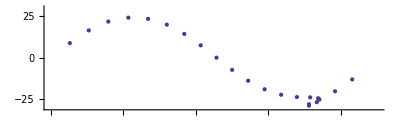

```mathematica
ListPlot[
  Table[{Ascension/Hour*15, Declination/Degree} /.
     EquatorCoordinates[Mars, {1986,1,day,0,0,0},
                        ViewPoint -> Earth],
        {day, -300, 350, 30}],
  PlotRange   -> {{0, 360}, {-30, 30}},
  AspectRatio -> 0.3]
```

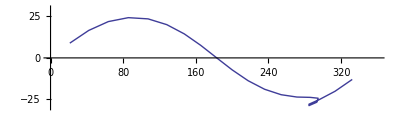

```mathematica
ListPlot[
  Table[{Ascension/Hour*15, Declination/Degree} /.
     EquatorCoordinates[Mars, {1986,1,day,0,0,0},
                        ViewPoint -> Earth],
        {day, -300, 350, 30}],
 Joined  -> True,
  PlotRange   -> {{0, 360}, {-30, 30}},
  AspectRatio -> 0.3]
```

Here's a plot of the x and y co-ordinates of Mercury as viewed from Earth.

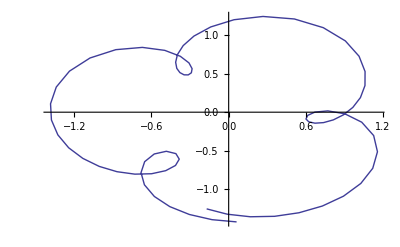

```mathematica
ListPlot[
  Table[Take[Coordinates[Mercury, {1986,1,d,0,0,0},
                         ViewPoint -> Earth], 2],
        {d, 1, 366, 5}],
  Joined -> True]
```

Here's a plot of the x and y co-ordinates of Mercury as viewed from Earth.

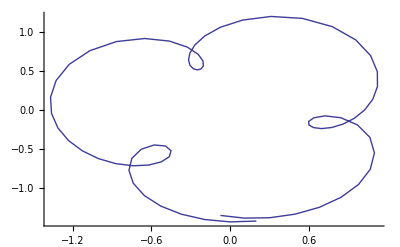

```mathematica
ListPlot[Table[Take[Coordinates[Mercury,{1993,1,d},ViewPoint->Earth],2],{d,1,366,5}],Joined->True]
```

7.1.3. Equator Coordinates command
These coordinates are useful in conjunction with Star charts.

```mathematica
Information["EquatorCoordinates",LongForm->False]
```

EquatorCoordinates[object, date] returns the Ascension, Declination and Distance of the object (a planet or a star) on the given date. An example planet would be Mars, and an example star would be Alpha.Centaurus. EquatorCoordinates[horizoncoords, date] will convert the horizoncoords for the current location into equatorcoords. An example horizoncoords would be {Azimuth->270*Degree, Altitude->30*Degree}. If date is omitted the current Date[] is used.

The EquatorCoordinates command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

Here are some basic examples:

```mathematica
EquatorCoordinates[Mars,{1993,11,17,3,20,0}]
```

{Ascension→16.2238 Hour,Declination→-0.377566,Distance→2.45251 AU}

```mathematica
-0.3775658684539316/Degree
```

-21.6329

```mathematica
(* d.h. Declination = -21.63425809263331 ° *)
```

```mathematica
EquatorCoordinates[Sun,{1993,11,17,3,20,0}]
```

{Ascension→15.464 Hour,Declination→-0.329059,Distance→0.988773 AU}

```mathematica
EquatorCoordinates[Moon,{1993,11,17,3,20,0}]
```

{Ascension→18.1124 Hour,Declination→-0.364836,Distance→0.00253195 AU}

Because the Moon is so close to Earth, you may sometimes want to set your viewpoint to the surface of Earth (i.e TopoCentric) rather than the default centre of the Earth.

```mathematica
EquatorCoordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{Ascension→18.1069 Hour,Declination→-0.350614,Distance→0.00255416 AU}

You can also find the equator coordinates of a star. The syntax for specifying a star name is to use: star.constellation. For example:

```mathematica
EquatorCoordinates[Alpha.Centaurus,{1993,11,17,3,20,0}]
```

{Ascension→14.6522 Hour,Declination→-1.06123,Distance→∞}

Note stars have fixed equator coordinates – that is they don't change with time. (Actually they do change a little with time due to the precession of the Earth's axis, but the effect is very small. Use the Epoch option to see the effect.)

The brightest 25 stars have also been given aliases, so for examples you can use Sirius, Canopus and Polaris etc as star names.

You can also find the equator coordinates of a point relative to the horizon at some local time. For example:

```mathematica
EquatorCoordinates[{Azimuth->60 °,Altitude->30 °},{1993,11,17,3,20,0}]
```

{Ascension→8.95884 Hour,Declination→0.0357012}

7.1.4. Horizon Coordinates command
These are useful when you are out in the field. A negative Altitude would mean the object is currently below the horizon.

```mathematica
Information["HorizonCoordinates",LongForm->False]
```

HorizonCoordinates[object, date] returns the Azimuth, Altitude and Distance of the object (a planet or a star) on the given date. An example planet would be Mars, and an example star would be Alpha.Centaurus. HorizonCoordinates[equatorcoords, date] will convert the equatorcoords into horizoncoords for the current location. An example equatorcoords would be {Ascension->18*Hour, Declination->30*Degree}. If date is omitted the current Date[] is used.

The HorizonCoordinates command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

Here are some basic examples:

```mathematica
HorizonCoordinates[Mars,{1993,11,17,3,20,0}]
```

{Azimuth→2.73305,Altitude→-0.470302,Distance→2.45251 AU}

```mathematica
HorizonCoordinates[Sun,{1993,11,17,3,20,0}]
```

{Azimuth→2.52169,Altitude→-0.43718,Distance→0.988773 AU}

```mathematica
HorizonCoordinates[Moon,{1993,11,17,3,20,0}]
```

{Azimuth→3.25458,Altitude→-0.541601,Distance→0.00253195 AU}

Because the Moon is so close to Earth, you may sometimes want to set your viewpoint to the surface of Earth (i.e TopoCentric) rather than the default centre of the Earth.

```mathematica
HorizonCoordinates[Moon,{1993,11,17,3,20,0},ViewPoint->TopoCentric]
```

{Azimuth→3.25458,Altitude→-0.555888,Distance→0.00255416 AU}

You can also find the horizon coordinates of a star. The syntax for specifying a star name is to use: star.constellation. For example:

```mathematica
HorizonCoordinates[Alpha.Centaurus,{1993,11,17,3,20,0}]
```

{Azimuth→2.76911,Altitude→0.270423,Distance→∞}

You can also find the horizon coordinates of a fixed point on the celestial sphere. For example:

```mathematica
HorizonCoordinates[{Ascension->6 Hour,Declination->30 °},{1993,11,17,3,20,0}]
```

{Azimuth→0.0693045,Altitude→0.385432}

A command related to HorizonCoordinates is Refract.

```mathematica
Information["Refract",LongForm->False]
```

Refract[horizoncoords] converts true horizoncoords (i.e the horizon coordinates returned by the HorizonCoordinates command) into apparent horizon coordinates by adding an atmospheric refraction correction. The correction can amount to about 0.5 Degree for objects close to the horizon, but is otherwise quite small.

For example, the SunRise and SunSet commands correctly take into account atmospheric refraction. This means however that the true horizoncoords of the Sun is approximately half a degree below the horizon at sunrise or sunset. I.e

```mathematica
HorizonCoordinates[Sun,SunSet[],ViewPoint->TopoCentric]
```

{Azimuth→4.43166,Altitude→-0.00968923,Distance→0.987939 AU}

```mathematica
(* {Azimuth->244.8640453667117 °,Altitude->-0.5217329165497615 °,Distance->0.984371304509849 AU} *)
```

To correct this to see that the Sun is apparently at 0 degrees above the horizon, just apply Refract

```mathematica
Refract[HorizonCoordinates[Sun,SunSet[],ViewPoint->TopoCentric]]
```

Refract::noavail: This is just the demo version, and Refract is not available.

```mathematica
(* Refract[HorizonCoordinates[Sun,SunSet[],ViewPoint->TopoCentric]] *)
```

```mathematica
{Azimuth->244.8640453667117 °,Altitude->0.01944841877478964 °,Distance->0.984371304509849 AU}
```

The above shows that the atmospherically refracted position of the Sun is almost exactly on the horizon at sunset, which is where it should be at that time.

7.1.5. The Elongation command 
This is useful for indirectly determining the Rising and Setting times of a planet relative to local Sunrise and Sunset.

```mathematica
Information["Elongation",LongForm->False]
```

Elongation[object, date] returns the Elongation of the object (a planet or a star etc). This measures the angle that the object is East of the Sun. A negative angle would mean the object is West of the Sun. Objects with positive Elongation are mostly evening visible, whereas objects with negative Elongation are mostly morning visible. If date is omitted the current Date[] is used.

```mathematica
Elongation[Mars,{1993,11,17,3,20,0}]
```

0.198901

```mathematica
(* 7.713312735306147 ° *)
```

7.1.6. The Separation command 
This is useful for determining Conjunctions, Eclipses and Transits etc.

```mathematica
Information["Separation",LongForm->False]
```

Separation[object1, object2, date] returns the angular separation of the two objects (which may be planets, Sun, Moon, asteroids or stars etc) on the given date. If date is omitted the current Date[] is used. And if only one object is given, then the other object is assumed to be the Sun.

The Separation command can be applied to objects like Mars, Moon, Io (solar system objects), Sirius, Alpha.Centaurus (stars), Leo, UrsaMajor (constellations), SouthCelestialPole, Zenith (special objects) etc.

```mathematica
Separation[Mars,Jupiter,{1993,11,17,12,0,0}]
```

0.599309

```mathematica
Separation[Venus,Neptune,{2991,3,22,13,40,0}]
```

0.021624

```mathematica
Separation[Venus,Antares,{4296,11,22,12,0,0}]
```

0.0675464

```mathematica
Ephemeris[Jupiter,{1993,11,17,12,0,0}]
```

Jupiter
------------------------------------------
Date Time:   17-Nov-1993 12:00:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        4:57 am (Sunrise:  6:09 am)
Setting:       6:10 pm (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:       345^57' (North     compass)
Altitude:       62^30' (Above the horizon)
------- For Date Time: -------------------
Elongation:    -23^22' (Morning sky. 100%)
Distance:      6.34 AU (Magnitude:   -1.7)
------- For Date Time: -------------------
Ascension:    13h58.2m (Virgo        210^)
Declination:   -10^56' (Ecliptic +  1^04')
------------------------------------------

-EphemerisData-

```mathematica
Ephemeris[Mars,{1993,11,17,12,0,0}]
```

Mars
------------------------------------------
Date Time:   17-Nov-1993 12:00:00. (GMT+11)
Geo-place:     145^00'E,  37^48'S (Earth.)
------- For Date, Geo-place: -------------
Rising:        6:36 am (Sunrise:  6:09 am)
Setting:       9:04 pm (Sunset:   8:20 pm)
------- For Date Time, Geo-place: --------
Azimuth:        63^36' (NorthEast compass)
Altitude:       61^21' (Above the horizon)
------- For Date Time: -------------------
Elongation:     10^56' (Evening sky. 100%)
Distance:      2.45 AU (Magnitude:   +1.9)
------- For Date Time: -------------------
Ascension:    16h14.5m (Scorpius     244^)
Declination:   -21^41' (Ecliptic -  0^27')
------------------------------------------

-EphemerisData-

```mathematica
separation[body1_, body2_, date_]:=Module[{eph1,eph2,dec1,dec2,RA1,RA2},
eph1=Ephemeris[body1, date];RA1=eph1[[5,1]] Degree;
 dec1=eph1[[4,2]]Degree;
eph2=Ephemeris[body2,date]; RA2=eph2[[5,1]] Degree; dec2=eph2[[4,2]]Degree;
N[ArcCos[Sin[dec1]*Sin[dec2]+Cos[dec1]*Cos[dec2]*Cos[RA1-RA2]]]]
```

```mathematica
separation[Mars,Jupiter,{1993,11,17,12,0,0}]
```

0.602849

```mathematica
Separation[Mars,Jupiter,{1993,11,17,12,0,0}]
```

0.599309

```mathematica
(* 34.23618286227749 ° *)
```

```mathematica
Separation[Moon,Sun,{1993,11,17,3,20,0}]
```

0.651394

```mathematica
(* 37.32212951829216 ° *)
```

```mathematica
Separation[Venus,Sun,{1993,11,17,3,20,0}]
```

0.259445

```mathematica
Separation[Mars,Earth,{1993,11,17,3,20,0},ViewPoint->Sun]
```

2.82172

Here's a plot of the separation of the Moon and the Sun during the month of November in 1994. If the separation is less than about half a degree, then that will be a partial Solar Eclipse.

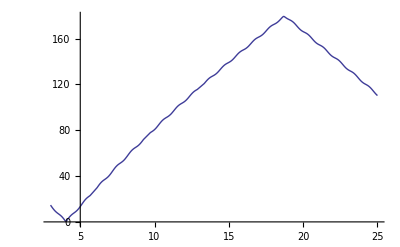

```mathematica
Plot[1/°Separation[Moon,Sun,{1994,11,d},ViewPoint->TopoCentric],{d,3,25}]
```

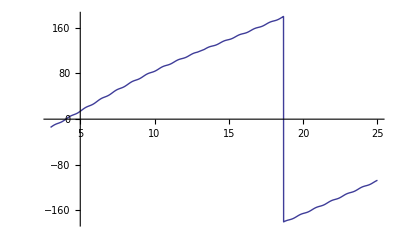

```mathematica
Plot[Elongation[Moon, {1994,11,d},ViewPoint->TopoCentric]/Degree, {d,3,25}]
```

In 1769 Captain Cook sailed to the Pacific to witness a transit of Venus across the solar disk. This happens only four times every 243 years. Here is the event (which happened at about 9AM on 4 June local time in Melbourne, but would have been about midday on 3 June in Tahiti) that he waited for:

WolframAlphaQueryParseResults

Sat 3 Jun 1769 22:49:43GMT+0.891111

```mathematica
Separation[Venus,Sun,{1769,6,4,9,0,0}]
```

0.00299225

```mathematica
Tahiti[]=Location["Tahiti, Polynesia", Deg[-17.67],Deg[-149.5],Mt[2241],-12]
```

Tahiti, Polynesia: lat. "17.670" S, long. "149.500" W, elev. 2241, zone "-12.00"

```mathematica
Trennung[Venus,Sun,{1769,6,4,9,0,0}, Tahiti[]]
```

0.00299225

```mathematica
(* 0.1714435384928253 ° *)
```

```mathematica
Trennung[Venus,Sun,{1769,6,4,9,0,0}, Tahiti[]]/Degree
```

0.171444

```mathematica
Elongation[Venus, {1769,6,4,9,0,0}]/Degree
```

-0.0211889

Ermittlung von Opposition:

```mathematica
Separation[Vesta,Sun,{1993,8,28, 0, 0, 0}]/°
```

170.16

```mathematica
separation[Vesta,Sun,{1993,8,28, 0, 0, 0}]/°
```

171.183

```mathematica
BestView[Sirius, {1993,11,17}]
```

BestView::noavail: This is just the demo version, and BestView is not available.

```mathematica
Separation[Moon,Mars,{1997,1,1, 7, 0, 0}]/°
```

3.96714

Ptolamaios meldete., im 17. Jahr Hadrians (Julianisch 133) hätte am 1./2. Epiphi eine Opposition Sonne-Jupiter und am 18. Epiphi eine Opposition Sonne-Saturn stattgefunden

```mathematica
Module[{datum=ConvertDateTo[Julian[132,12,31],Gregorian]},Do[datum=DaysPlusC[datum, 1];If[oppositionQ[Sun, Jupiter, datum], 
Print[ConvertDateTo[datum,Julian]]], {365}]]
```

9 May 133 C.E.

10 May 133 C.E.

11 May 133 C.E.

12 May 133 C.E.

13 May 133 C.E.

14 May 133 C.E.

15 May 133 C.E.

16 May 133 C.E.

17 May 133 C.E.

18 May 133 C.E.

19 May 133 C.E.

20 May 133 C.E.

21 May 133 C.E.

22 May 133 C.E.

23 May 133 C.E.

24 May 133 C.E.

25 May 133 C.E.

26 May 133 C.E.

Das Kerndatum dieser Opposition ist der 17./18. Mai 133 C.E.

```mathematica
ConvertDateTo[Julian[133,5,18],Egyptian]
```

2 Epiphi 880

```mathematica
Module[{datum=ConvertDateTo[Julian[132,12,31],Gregorian]},Do[datum=DaysPlusC[datum, 1];If[oppositionQ[Sun, Saturn, datum], 
Print[ConvertDateTo[datum,Julian]]], {365}]]
```

27 May 133 C.E.

28 May 133 C.E.

29 May 133 C.E.

30 May 133 C.E.

31 May 133 C.E.

1 June 133 C.E.

2 June 133 C.E.

3 June 133 C.E.

4 June 133 C.E.

5 June 133 C.E.

6 June 133 C.E.

7 June 133 C.E.

8 June 133 C.E.

9 June 133 C.E.

10 June 133 C.E.

11 June 133 C.E.

12 June 133 C.E.

13 June 133 C.E.

14 June 133 C.E.

Kerndatum dieser Opposition ist der 3./4. Juni

```mathematica
ConvertDateTo[Julian[133,6,3],Egyptian]
```

18 Epiphi 880

```mathematica
oppositionQ[Vesta, Sun, Gregorian[1993, 8, 28]]
```

True

(* Ein spezielleres Verfahren für den Merkurtransit *)

```mathematica
durchgangQ[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 
Module[{erg = False,h, sp1, sp2, eph},h=0;sp1= Separation[obj1, obj2, {y,m,d}]/Degree; 
sp2= Separation[obj1, obj2, {y,m,d, 8,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=8];
sp2= Separation[obj1, obj2, {y,m,d, 16,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=16];
If[sp1 < 2.0, eph = Ephemeris[Mercury, {y,m,d,h,0,0}]; If[(Last[eph][[2]] < 0.002) && (Abs[eph[[3,1]]] < 2), erg = True]]; erg]
```

```mathematica
durchgang2Q[obj1_, obj2_, Gregorian[y_, m_, d_]]:= 
Module[{erg = False,h, sp1, sp2, eph},h=0;sp1= separation[obj1, obj2, {y,m,d}]/Degree; 
sp2= separation[obj1, obj2, {y,m,d, 8,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=8];
sp2= separation[obj1, obj2, {y,m,d, 16,0,0}]/Degree; If[sp2 < sp1, sp1 = sp2; h=16];
If[sp1 < 2.0, eph = Ephemeris[Mercury, {y,m,d,h,0,0}]; If[(Last[eph][[2]] < 0.002) && (Abs[eph[[3,1]]] < 2), erg = True]]; erg]
```

```mathematica
(* Hier der von Kepler vorausgesagte Transit zum 7.11.1631 *)
```

```mathematica
Module[{aktday},aktday= Gregorian[1631,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgangQ[Mercury, Sun, aktday],Print[aktday]; aktday = DaysPlusC[aktday, 7]], {365}]]
```

Friday, 7 November 1631

```mathematica
Module[{aktday},aktday= Gregorian[1631,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgang2Q[Mercury, Sun, aktday],Print[aktday]; aktday = DaysPlusC[aktday, 7]], {365}]]
```

Friday, 7 November 1631

(* Gem. Leipziger Repetitorium der deutschen und ausländischen Literatur, Bd. 26, S. 2 “ist Mercur (Phoenix), der sich alle 652 Jahre in der Sonnenstadt (Sonne) verbrannte... durch die Sonne gegangen; es war den astronomischen Tafeln gemäss am 8. April 1904 BCE geschehen” Gemeint ist julianisch, da die Tafeln vor Claudius 50 n.Chr. angefertigt waren. Wir berechnen den Beginn des bis zu 3-tägigen Merkurtransits: *)

```mathematica
Module[{aktday},aktday= Gregorian[-1903,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgangQ[Mercury, Sun, aktday],Print[ConvertDateTo[aktday,Julian]]], {365}]]
```

7 April 1904 B.C.E.

8 April 1904 B.C.E.

9 April 1904 B.C.E.

```mathematica
Module[{aktday},aktday= Gregorian[-1903,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgang2Q[Mercury, Sun, aktday],Print[ConvertDateTo[aktday,Julian]]], {365}]]
```

7 April 1904 B.C.E.

8 April 1904 B.C.E.

9 April 1904 B.C.E.

(* ebda: “Derselbe Phoenix... hatte sich zum ersten Male unter Sesostris in der Sonnentadt verbrannt; es war am 6. April 2555 geschehen” *)

```mathematica
Module[{aktday},aktday= Gregorian[-2554,1,1]; Do[aktday=DaysPlusC[aktday, 1]; If[durchgangQ[Mercury, Sun, aktday],Print[ConvertDateTo[aktday,Julian]]], {365}]]
```

5 April 2555 B.C.E.

6 April 2555 B.C.E.

7 April 2555 B.C.E.

```mathematica
(* Diese "Verbrennung des Phoenix" wiederholt sich von Heliopolis aus gesehen alle 237780.5 Tage (d.h.grob alle 652 Jahre).Weitere Durchgänge nach eigenen Berechnungen: *)
```

```mathematica
Module[{aktday=Julian[-2555,4,6],greg},Do[greg= ConvertDateTo[aktday,Gregorian]; If[durchgangQ[Mercury, Sun, greg], Print["Merkurdurchgang bestätigt: "]];
Print[aktday, " = gregorianisch ",greg ];aktday= DaysPlusC[aktday, 237780]; If[Mod[i,2]==0,aktday= DaysPlusC[aktday, 1]],{i,1,9}]]
```

Merkurdurchgang bestätigt:

6 April 2555 B.C.E. = gregorianisch Monday, 16 March -2554

Merkurdurchgang bestätigt:

8 April 1904 B.C.E. = gregorianisch Friday, 22 March -1903

Merkurdurchgang bestätigt:

11 April 1253 B.C.E. = gregorianisch Wednesday, 31 March -1252

Merkurdurchgang bestätigt:

14 April 602 B.C.E. = gregorianisch Sunday, 7 April -601

Merkurdurchgang bestätigt:

17 April 50 C.E. = gregorianisch Friday, 15 April 50

Merkurdurchgang bestätigt:

19 April 701 C.E. = gregorianisch Tuesday, 23 April 701

Merkurdurchgang bestätigt:

22 April 1352 C.E. = gregorianisch Sunday, 30 April 1352

Merkurdurchgang bestätigt:

25 April 2003 C.E. = gregorianisch Thursday, 8 May 2003

Merkurdurchgang bestätigt:

28 April 2654 C.E. = gregorianisch Tuesday, 16 May 2654

Kepler hat nach Jupiter-Saturn Konjunktionen gesucht, die in etwa alle 20 Jahre stattfinden, und kam auf die Jahre 1583, 1603 etc. Hier ein Nachvollziehen der Berechnungen mit Startwerten jeweils ca 3 Jahre früher:

```mathematica
Module[{},aktday= Gregorian[1579,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[totaleConjQ[Jupiter, Saturn, aktday], Print[aktday]],{1500}]]
```

Wednesday, 4 May 1583

Thursday, 5 May 1583

Friday, 6 May 1583

Saturday, 7 May 1583

Sunday, 8 May 1583

Monday, 9 May 1583

Tuesday, 10 May 1583

Wednesday, 11 May 1583

Thursday, 12 May 1583

Friday, 13 May 1583

```mathematica
Module[{},aktday= Gregorian[1599,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[totaleConjQ[Jupiter, Saturn, aktday], Print[aktday]],{1500}]]
```

Thursday, 18 December 1603

Friday, 19 December 1603

Im Jahre 1682 wäre sogar eine (partielle) Konjunktion Mars-Jupiter-Saturn möglich:

```mathematica
Module[{},aktday= Gregorian[1679,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[partielleConjQ[Jupiter, Saturn, aktday] && totaleConjQ[Jupiter, Mars, aktday], Print[aktday]],{1500}]]
```

Wednesday, 16 September 1682

Thursday, 17 September 1682

Friday, 18 September 1682

```mathematica
(* Symposium : Konjunktion aller Planeten,Abweichung maximal 30 Grad bzw.alle Planeten stehen in einem oder 2 gegenüberliegenden Tierkreiszeichen,aufgereiht wie auf einer Schnur. Folgende Symposien kenne ich:5.5.2000,Mai 531 und 3102 vor Christus.Gab es weitere? 
Da das o.g. definierte Symposium recht häufig vorkommt und über einen vollen Monat dauern kann, definieren wir es strenger, d.h. Abweichungen < 10 Grad oder > 170 Grad *)
```

```mathematica
symposiumQ[Gregorian[y_,m_,d_]]:= Module[{merkurS,venusS,  erdeS, marsS, jupiterS, saturnS },
merkurS = Separation[Sun, Mercury, {y,m,d}]/Degree;
venusS =  Separation[Sun, Venus, {y,m,d}]/Degree;
erdeS = Separation[Sun, Earth, {y,m,d}]/Degree;
marsS =  Separation[Sun, Mars, {y,m,d}]/Degree;
jupiterS = Separation[Sun, Jupiter, {y,m,d}]/Degree;
saturnS = Separation[Sun, Saturn, {y,m,d}]/Degree;
((merkurS < 10) || (merkurS > 170)) &&  ((venusS < 10) || (venusS > 170)) && ((erdeS < 10) || (erdeS > 170)) && ((marsS < 10) || (marsS > 170)) && ((jupiterS < 10) || (jupiterS > 170)) && ((saturnS < 10) || (saturnS > 170)) ];
symposiumQ[jahr_Integer]:=Module[{aktday, erg=False},
aktday=Gregorian[jahr,1,1]; 
Do[aktday=DaysPlusC[aktday, 1]; If[symposiumQ[aktday],erg=True; Break[]],{365}];
erg]
```

```mathematica
symposiumQ[Gregorian[2025,1,22]]
```

False

```mathematica
symposiumQ[Gregorian[2000,5,5]]
```

False

```mathematica
symposiumQ[531]
```

False

```mathematica
Do[If[Mod[j,100]==0,Print["Jahr: ",j]];
If[symposiumQ[j], Print["Symposium im Jahr ",j]],{j,2000,3000}]
```

Jahr: 2000

Symposium im Jahr 2070

Jahr: 2100

Symposium im Jahr 2149

Jahr: 2200

$Aborted

```mathematica
symposium[2070]
```

Saturday, 11 October 2070

Sunday, 12 October 2070

Monday, 13 October 2070

Tuesday, 14 October 2070

Wednesday, 15 October 2070

Thursday, 16 October 2070

Friday, 17 October 2070

```mathematica
AstronomicalData["Mercury", {"Constellation",{1962,2,5}}]
```

Aquarius

```mathematica
horoskop[{1962,2,5}]
```

{{Moon,Aquarius},{Sun,Aquarius},{Mercury,Aquarius},{Venus,Aquarius},{Mars,Aquarius},{Jupiter,Aquarius},{Saturn,Aquarius}}

```mathematica
(* Astronom.Daten zur Überprüfung:Jupiter sei im Schützen,Saturn im Skorpion,Mars im Widder und Merkur in der Waage.Lt.Morosow ist dies, verbunden mit einer Sonnenfinsternis,am 30.09.395 C.E. vorgekommen, d.h proleptisch gregorianisch am 01.10.395 AD: *)
```

```mathematica
ConvertDateTo[Julian[395,9,30],Gregorian]
```

Sunday, 1 October 395

```mathematica
rückwärtshoroskop[{395,1,1},365,{Jupiter,Sagittarius},{Saturn, Scorpius},{Mars, Aries},{Mercury,Libra}]
```

{395,9,6}

{395,9,7}

{395,9,8}

{395,9,9}

{395,9,10}

{395,9,11}

{395,9,12}

{395,9,13}

{395,9,14}

{395,9,15}

{395,9,16}

{395,9,17}

{395,9,18}

{395,9,19}

{395,9,20}

{395,9,21}

{395,9,22}

{395,9,23}

{395,9,24}

{395,9,25}

{395,9,26}

{395,9,27}

{395,9,28}

{395,9,29}

{395,9,30}

{395,10,1}

{395,10,2}

{{395,9,6},{395,9,7},{395,9,8},{395,9,9},{395,9,10},{395,9,11},{395,9,12},{395,9,13},{395,9,14},{395,9,15},{395,9,16},{395,9,17},{395,9,18},{395,9,19},{395,9,20},{395,9,21},{395,9,22},{395,9,23},{395,9,24},{395,9,25},{395,9,26},{395,9,27},{395,9,28},{395,9,29},{395,9,30},{395,10,1},{395,10,2}}

Steine der Macht, Bd. 4: „Das hier bedeutet Sonne Opposition Mond und sagt aus, daß es eine Zeit des Vollmondes sein muss. Den gibt es aber jeden Monat einmal. Dann steht direkt an der Sonne der Jupiter, was jedes Jahr einmal vorkommt und daher noch nicht als genaue Datumsangabe dienen kann. Der Saturn steht im Trigon zur Sonne, und das ist in Verbindung mit dem Jupiter schon eine sehr präzise Angabe. Die beiden Planeten Jupiter und Saturn hat im ürigen der italienische Gelehrte Galileo im Jahr 1610 entdeckt. Seitdem hat man früher gerne versteckte Zeitangaben mit diesen beiden Planeten gemacht.”
Wir beginnen mit dem 1.1.2005 und suchen etwa 15 Folgejahre ab, sagen wir: 5500 Tage. Da die Konjunktionen leichter zu errechnen sind als Vollmonde, werden sie in der If-Abfrage vorangestellt:

```mathematica
Module[{},aktday= Gregorian[2004,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[partielleConjQ[Jupiter, Sun, aktday] && trineQ[Saturn, Sun, aktday] && FullmoonQ[aktday], Print[aktday]], {5500}]]
```

Sunday, 23 June 2013

Saturday, 12 July 2014

Auf die Funktion FullMoonQ können wir nicht verzichten. Approximieren wir dies durch oppositionQ, wird die Ausgabe unpräzise:

```mathematica
Module[{},aktday= Gregorian[2004,12,31]; Do[aktday=DaysPlusC[aktday, 1]; If[partielleConjQ[Jupiter, Sun, aktday] && trineQ[Saturn, Sun, aktday] && oppositionQ[Moon, Sun, aktday], Print[aktday]], {5500}]]
```

Monday, 12 January 2009

Monday, 24 June 2013

Sunday, 13 July 2014

```mathematica
(* Wenn nur der Geburtstag, aber nicht die Geburtsstunde bekannt ist, dann spielt der Mond keine Rolle *)
```

```mathematica
horoskop[{2013,6,23}]
```

{{Moon,Sagittarius},{Sun,Cancer},{Mercury,Cancer},{Venus,Cancer},{Mars,Gemini},{Jupiter,Gemini},{Saturn,Libra}}

```mathematica
(* Will man Exaktheit, dann muss man die Uhrzeit kennen *)
```

```mathematica
horoskop[{2013,6,23, 20, 0,0}]
```

{{Moon,Capricornus},{Sun,Cancer},{Mercury,Cancer},{Venus,Cancer},{Mars,Gemini},{Jupiter,Gemini},{Saturn,Libra}}

```mathematica
horoskop[{1960,10,9, 10, 0,0}]
```

{{Moon,Gemini},{Sun,Libra},{Mercury,Scorpius},{Venus,Scorpius},{Mars,Cancer},{Jupiter,Sagittarius},{Saturn,Capricornus}}

```mathematica
Map[Separation[Moon, #, {1960,10,9, 10, 0,0}]/Degree&, {Sun, Mercury, Venus, Mars, Jupiter, Saturn}]
```

{131.442,154.377,159.685,34.7672,156.182,139.913}

```mathematica
Map[Separation[Sun, #, {1960,10,9, 10, 0,0}]/Degree&, { Mercury, Venus, Mars, Jupiter, Saturn}]
```

{23.912,28.7454,97.2655,71.6626,88.197}

```mathematica
Map[Separation[Mercury, #, {1960,10,9, 10, 0,0}]/Degree&, {Venus, Mars, Jupiter, Saturn}]
```

{5.33804,121.06,47.9015,64.4217}

```mathematica
Map[Separation[Venus, #, {1960,10,9, 10, 0,0}]/Degree&, { Mars, Jupiter, Saturn}]
```

{126.011,42.9196,59.4546}

```mathematica
Map[Separation[Mars, #, {1960,10,9, 10, 0,0}]/Degree&, { Jupiter, Saturn}]
```

{168.921,174.51}

```mathematica
Separation[Jupiter, Saturn, {1960,10,9, 10, 0,0}]/Degree
```

16.5341

```mathematica
Separation2[Jupiter, Saturn, {1960,10,9, 10, 0,0}]/Degree
```

16.5341

```mathematica
(* Rückwärtshoroskop ohne Berücksichtigung von Mond, damit es an einem bestimmten Datum stabil bleibt 
Eingegeben werden ein mögliches Anfangsdatum, die Anzahl zu untersuchender Tage und vorgegebene Planetenkonstellationen auf Lateinisch, z.B. {Jupiter, Gemini} *)
```

```mathematica
rückwärtshoroskop[{2000,1,1},5500,{Venus, Cancer},{Jupiter, Gemini}, {Mercury, Cancer},{Mars, Gemini}, {Saturn, Libra}, {Sun, Cancer}]
```

{2013,6,23}

{{2013,6,23}}

```mathematica
rückwärtshoroskop[{2013,1,1},5500,{Venus, Cancer},{Jupiter, Gemini}, {Mercury, Cancer},{Mars, Gemini}, {Saturn, Libra}, {Sun, Cancer}]
```

{2013,6,22}

{2013,6,23}

{{2013,6,22},{2013,6,23}}

```mathematica
partielleConjQ[Sun, Jupiter, Gregorian[2013, 6, 23]]
```

True

```mathematica
trineQ[Sun, Saturn, Gregorian[2013, 6, 23]]
```

True

Messung der Präzession: Im Jahre 1950 wäre der Polarstern praktisch genau am nördlichen Sternhimmel, d.h. seine Deklination wäre nahezu 90°

```mathematica
EquatorCoordinates[Polaris, Epoch -> 1950.0]
```

{Ascension→1.60852 Hour,Declination→1.55387,Distance→∞}

```mathematica
1.55387/Degree
```

89.0302

Dagegen wird er in 2000 Jahren weit davon entfernt sein:

```mathematica
EquatorCoordinates[Polaris, Epoch -> 3950.0]
```

{Ascension→1.93408 Hour,Declination→1.43482,Distance→∞}

```mathematica
1.143482/Degree
```

65.5167

### 7.2. Grundsätzliches zu AstronomicalData

Im folgenden wollen wir einfache elementare Funktionen für Astronomen einsetzen, wie sie bereits unter Newton üblich waren. Leider wird die Einfachheit mit Ungenauigkeit erkauft, so erreichen errechnete Planetenpositionen nur für das 20ste und 21ste Jh eine Genauigkeit von < 2 Gradminuten.

Ein Himmelkörper umkreist die Sonne idR auf einer Ellipsenbahn, mit leichten Abweichungen durch Störungen (Perturbationen) durch andere Planeten.
Perihelion und Aphelion sind die Punkte der Planetenbahn mit der geringsten bzw. größten Distanz zur Sonne. Analog sind Perigäum und Apogäum die Punkte der Mondbahn mit der gerinsten bzw. größten Distanz zur Erde.
Der Himmelskugel ist eine unendlich groß gedachte Kugel um die Sonne, der Himmelsäquator die Projektion des Erdäquators auf die Himmelskugel, und die Ekliptik die Projektion der Erdbahn auf die Himmelskugel, mit einer Neigung von 23°27' (=Schiefe der Ekliptik).
Die Ekliptik schneidet den Himmelsäuator an 2 Punkten, welche Frühlings- und Herbstpunkt heißen. Man unterteilt die Ekliptik in die 12 Tierkreiszeichen a 30°, beginnend mit dem Widder am Frühlingsequinox, den im Gegenuhrzeigersinn Stier,  Zwillinge, Krebs, Löwe, Jungfrau, Waage, Skorpion, Schütze, Steinbock, Wassermann und Fische folgen.
Die Deklination ist der Winkelabstand eines Punktes zum Himmelsäquator (von +90° Nord bis -90° Süd), die "Right Ascension" ist die Unterteilung des Himmelsäquators in 24 Stunden a 15°, 0 Uhr beginnt beim Frühlingsequinox, gezählt wird im Gegenuhrzeigersinn.
Longitude und Latitude sind Längen- und Breitengrad des irdischen Globus, am Himmelsglobus projiziert.
Die heliozentrische Position betrachtet alle Daten aus dem Mittelpunkt der Sonne, die geozentrische aus dem Mittelpunkt der Erde und die topozentrische aus einem Punkt auf dem Erdglobus. Für Himmelskörper außer dem Mond beträgt die Differenz zwischen geozentrischer und topozentrischer Position vernachlässigbare 1 bis 2 Gradminuten.
Planetenbahnelemente bestehen aus 6 Parametern, wobei 3 die Form und Größe der elliptischen Bahn sowie die Planetenposition darin bezeichnen, und 3 die Lage der Bahn im Raum:
a = Distanz (idR in Astronom. Einheiten)
e = Exzentrität
tg = Zeit beim Perihel
i = Inklination relativ zur Ekliptik, 0 bis 180°. Bei einer
 Inklination über 90° bewegt sich der Planet rückwärts.
ng= Winkel zwischen Frühlingsequinox und Ascending Node.
w = Winkel zwischen Ascending Node und Perihelion.

Hieraus lassen sich weitere Werte ableiten:
Perihelion-Distanz q = a*(1-e)
Apohelion-Distanz qg = a*(1+e)
Orbitalperiode Pg = 365.256898326*a^1.5/Sqrt[1+m] dygn, mit  Planetenmasse m.
Tagesbewegung n = 360 Degree/pg Degree/Day.
Tageszählung t, meist als JD. tg ist in der gleichen Einheit  anzugeben.
Zeit seit Perihelion = t - tg.
Anomalie mg = n*(t-tg), beim Perihel 0° u beim Apohel 180°.
Longitude lg = mg+w+ng
Exzentritätsanomalie eg, wobei eg == mg+e*Sin[eg]
Echte Anomalie v = Winkel zwischen Perihel und Planet, von Sonne  aus  betrachtet.
Heliozentr. Distanz r des Planeten von der Sonne.
Die beiden letzen Variablen erfüllen die Gleichungen 
 {r*Cos[v]==a*(Cos[eg]-e), r*Sin[v]==a*Sqrt[1-e*e]*Sin[eg]}

### 7.3 Extraterrestische Kalender

### 7.3.1 Auf dem Mars

```mathematica
JulianDay[date_]:= JDFromFixed[ToFixed[date]]
```

```mathematica
JulianDay[Gregorian[2013,1,1]]
```

2.45629×10^6

```mathematica
ConvertDateTo[date_,MarsSolDate]:= MarsSolDate[(JulianDay[date]-2451549.5+0.00014)/1.02749125 + 44795.9998]
```

```mathematica
ConvertDateTo[MarsSolDate[msd_], Gregorian]:= Module[{jd, fd},jd=(msd-44795.9998)*1.02749125-0.00014+2451549.5; fd=FixedFromJD[jd]; ConvertDateTo[fd,Gregorian]]
```

```mathematica
ConvertDateTo[Gregorian[2013,1,1],MarsSolDate]
```

MarsSolDate[49413.1]

```mathematica
ConvertDateTo[MarsSolDate[49413.3],Gregorian]
```

Tuesday, 1 January 2013

```mathematica
ConvertDateTo[date_,MarsTimeCoordinated]:= MarsTimeCoordinated[Mod[First[ConvertDateTo[date,MarsSolDate]],86400]*24]
```

```mathematica
ConvertDateTo[Gregorian[2013,1,1],MarsTimeCoordinated]
```

MarsTimeCoordinated[1.18591×10^6]

```mathematica
EquiSol[1955]
```

{{Monday, 21 March 1955,{9,39,57.1282}},{Wednesday, 22 June 1955,{4,39,34.0773}},{Friday, 23 September 1955,{19,49,5.67654}},{Thursday, 22 December 1955,{15,15,25.5754}}}

```mathematica
EquiSolMars[y_]:=
Module[{eq0=ToFixed[Gregorian[1955,4,11]]+(y-1955)*365.244},
If[y>1582,
Map[Gregorian[Round[#]]&,{eq0,eq0+92.764,eq0+186.411,eq0+276.247}],
Map[Julian[Round[#]]&,{eq0,eq0+92.764,eq0+186.411,eq0+276.247}]]]
```

```mathematica
EquiSolMars[1955]
```

{Monday, 11 April 1955,Wednesday, 13 July 1955,Friday, 14 October 1955,Thursday, 12 January 1956}

```mathematica
EquiSolMars[1776]
```

{Tuesday, 9 April 1776,Thursday, 11 July 1776,Sunday, 13 October 1776,Saturday, 11 January 1777}

```mathematica
EquiSolMars[33]
```

{9 April 33 C.E.,11 July 33 C.E.,12 October 33 C.E.,10 January 34 C.E.}

```mathematica
EquiSolMars[-1515]
```

{18 April 1516 B.C.E.,20 July 1516 B.C.E.,22 October 1516 B.C.E.,20 January 1515 B.C.E.}

### 7.3.2. Auf dem Jupiter

```mathematica
ConvertDateTo[date_,DavidianJovian]:=Module[{ed}, ed = DayNumber[date]; ed = (ed-1)/(ed+DaysRemaining[date])+date[[1]];
DavidianJovinian[((ed+10000)*365.26)/4331.572]]
```

```mathematica
ConvertDateTo[DavidianJovian[jd_],Gregorian]:=Module[{ed, j}, ed = N[((jd*4331.572)/365.26)-10000, 20]; j = Floor[ed];  ed = ed - j; 
ed = Floor[ed* (DaysRemaining[Gregorian[j,1,1]]+1)]; 
DaysPlusC[Gregorian[j,1,1], ed]]
```

```mathematica
ConvertDateTo[Gregorian[1969,7,20],DavidianJovian]
```

DavidianJovinian[1009.33]

```mathematica
ConvertDateTo[DavidianJovian[1009.33], Gregorian]
```

Tuesday, 8 July 1969

Etwas unpräzise, der Monat wird noch getroffen

### 7.3.3. Im Sonnensystem

Folgende Planeten untersuchen wir:

```mathematica
AstronomicalData["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

Ihre Umlaufszeiten um die Sonne:

```mathematica
AstronomicalData[#,"OrbitPeriodYears"]&/@AstronomicalData["Planet"]
```

{0.2408467,0.61519726,1.0000174,1.8808476,11.862615,29.447498,84.016846,164.79132}

Satelliten des Pluto:

```mathematica
AstronomicalData["Pluto","Satellites"]
```

{Charon,S2012P1,Nix,S2011P1,Hydra}

```mathematica
?AstronomicalData
```

WolframAlphaQueryParseResults

Cydonia

```mathematica
PlanetData["Venus",EntityProperty["Planet","RiseTime",{"Location"-> WolframAlphaQueryParseResults}]]
```

Missing[RetrievalFailure]

Wieviel bekannte Satelliten hat welcher Planet:

```mathematica
Length[AstronomicalData[#,"Satellites"]]&/@AstronomicalData["Planet"]
```

{0,0,1,2,63,61,27,13}

Die kürzeste Distanz zwischen Erde und den Planeten des Sonnensystems wöhrend eines Jahres ermitteln:

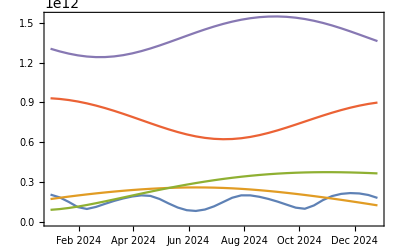

```mathematica
DateListPlot[Tooltip[Table[{DateList[{2024,1,i}],AstronomicalData[#,{"Distance",DateList[{2008,1,i}]}]},{i,1,365.25,10}],#]&/@{"Mercury","Venus","Mars","Jupiter","Saturn"},Joined->True]
```

```mathematica
AstronomicalData["Moon","Density"]
```

3344. kg/m^3

### 7.4. Relativistische Zeiteffekte

Durch Einsteins Spezielle Relativitätstheorie konnte gezeigt werden, daß die Zeit keine absolute Größe ist: je höher die Geschwindigkeit des beobachteten Inertialsystems, desto langsamer altert es relativ zum Beobachter. Diese Zeitdilatation kann durch die Formel von Lorentz exakt berechnet werden:

```mathematica
c0= 299792.4562*1000 Meter/Second; (* die Lichtgeschwindigkeit *)
t0= 1 Hour; (* dies sei die Meßdauer des Beobachters *)
trel[v_] := t0*Sqrt[1-(v/c)^2] /. c :> c0  
(* die Zeit, die während der Meßdauer für das beobachtete Objekt vergeht *)
v1 = 0.25*1000 Meter/Second; (* Reise im Jet *)
trel[v1]
```

1. Hour

```mathematica
(* Dies ist gerundet, doch wir wollen exakter rechnen: *)
N[%, 20]
```

```mathematica
0.999999999999652 Hour
```

Das Objekt bleibt um Sekundenbruchteile jünger.

```mathematica
v2 = 260000*1000 Meter/Second; (* Beschleunigung eines Elektrons *)
trel[v2]
```

```mathematica
0.497844 Hour
```

Das Elektron altert nur um ca. die Hälfte seines Beobachters. Analog zur Zeitdilatation erfolgt auch eine Längenkontraktion sowie eine Massenzunahme, d.h. das Elektron hat bei dieser Geschwindigkeit ca. doppelte Masse als im (imaginären) Ruhzustand. Bei allen Teilchen, die eine Masse > 0 besitzen, führt dies zur Unmöglichkeit, die Lichtgeschwindigkeit zu erreichen.

```mathematica
v3=c; (* Photon *)
trel[v3]
```

```mathematica
0
```

Teilchen, die sich mit c bewegen (Photonen, Neutrinos), gehören zur Klasse der Luxonen; Teilchen, die stets langsamer als c sind (alle massebehafteten Körper) gehören zur Klasse der Tardyonen.
Luxonen altern überhaupt nicht. Für sie ist seit Anbeginn der Welt noch keine Nanosekunde vergangen. Im Inertialsystem der Tardyonen läßt sich ein "Vorher" und ein "Nachher" unterscheiden, z.B. der aus der Taschenlampe kommende Lichtstrahl, der später von einem Spiegel reflektiert wird, noch später durch unsere Brille eintritt und zuletzt auf der Netzhaut unseres Auges den Wahrnehmungseffekt auslöst : das Ursache-Wirkungs-Prinzip. Für Luxonen verläuft alles gleichzeitig, in ihrem Inertialsystem gibt es kein "Vorher" und "Nachher", keine Ursache und Wirkung.
1967 gesellte man hierzu eine Klasse von Teilchen namens Tachyonen, die schneller sind als c und für welche die Zeit in komplexzahligen Sekunden verlaufen muss.
1965 war der Nobelpreis an Richard Feynmann, Prof. für Theoretische Physik am California Institute of Technology (CalTech) gegangen. Er hatte mathematisch exakt nachgewiesen, daß für Positronen (positiv geladene Elektronen) unter bestimmten Bedingungen die Zeit rückwärts abläuft. Dr. K. Scharnhorst, Physiker an der Berliner Humboldt-Universität, konnte nachweisen, daß die Geschwindigkeit von Photonen, die sich senkrecht zwischen 2 im Abstand von 10^-3 mm aufgestellten Platten bewegen, wegen eines quantenphysikalischen Phänomens namens Casimir-Effekt um 10^-36 km/Sekunde höher als c liegt. Lt. Paul Davies von der University of Newcastle/England hat diese infinitesimale Überschreitung von c "unübersehbare Folgen", da sie Phänomene ermöglicht, welche das Axiom der Kausalität verletzen.
Geschwindigkeiten weit über c setzt auch die Informationsübertragung zwischen Photonen voraus, die als Einstein-Rosen-Paradoxon bekannt geworden ist. Auf Grundlage der durch Photonen möglichen Speichereffekte und einer sich in unendlich viele Parallelprozesse aufteilenden Informationsübertragung durch Photonen soll ein Quantencomputer möglich sein, der jedes endliche mathematische Suchproblem in 0 Sekunden lösen kann.